# Definitions

## Some codes

```mathematica
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{"Select the experiments for which the number of events will be computed. The meaning is ",phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
```

## ALP models and typical scales used in this notebook

```mathematica
(*Subscript[c, u],Subscript[c, d],Subscript[c, s],Subscript[c, c],Subscript[c, b],Subscript[c, t], Subscript[c, G], Subscript[c, e],Subscript[c, μ],Subscript[c, τ], Subscript[c, W], Subscript[c, B] assuming the definition*)
Print["Definition of the couplings: L = α_s/(4  π)a/fc_G G_μν^a(G̃)^(a, μν)+δ^μ/f∑_q c_q q̄γ_μγ_5q+δ^μ/f∑_l c_l l̄γ_μγ_5l+α_1/(4  π)a/fc_BB_μν(B̃)^μν+α_2/(4  π)a/fc_WW_μν^a(W̃)^(a, μν)"]
Print["List of the ALP couplings considered in this notebook:"]
(*Names of the couplings*)
ALPcouplingslist={"cu","cd","cs","cc","cb","ct","cG","ce","cμ","cτ","cW","cB"}
ALPcouplingsSymbols=Symbol[#]&/@ALPcouplingslist;
(*Values of the couplings at a scale Λ*)
couplingPatternOverall["Fermion universal"]={1,1,1,1,1,1,0,1,1,1,0,0};
couplingPatternOverall["Quark universal"]={1,1,1,1,1,1,0,0,0,0,0,0};
couplingPatternOverall["Gluon"]={0,0,0,0,0,0,1,0,0,0,0,0};
(*ALPs coupled to gluons, with the coefficient Subscript[c, G] fixed to match 1811.03474 (Eq. S1 expressed in terms of Subscript[f, a])*)
couplingPatternOverall["Gluon Aloni"]={0,0,0,0,0,0,1/2,0,0,0,0,0};
couplingPatternOverall["W"]={0,0,0,0,0,0,0,0,0,0,1,0};
couplingPatternOverall["B"]={0,0,0,0,0,0,0,0,0,0,0,1};
Print["List of models implemented in this notebook:"]
ModelListAll=Keys[DownValues@couplingPatternOverall][[All,1,1]]
Print["Coupling pattern (defined at some scale Λ):"]
Join[{Join[{"Model"},ALPcouplingslist]},Join[Partition[ModelListAll,1],Table[couplingPatternOverall[model],{model,ModelListAll}],2]]//TableForm
Do[couplingPattern[model,ALPcouplingslist[[i]]]=couplingPatternOverall[model][[i]],{model,ModelListAll},{i,1,Length[couplingPatternOverall[model]],1}]
MASS["t"]=173.;
{scaleVal["EW"],scaleVal["1 TeV"],scaleVal["Neubert"]}={MASS["t"],10^3,4*Pi*10^3};
Print["List of reference scales Λ (in TeV):"]
scaleKeys=Keys[DownValues@scaleVal][[All,1,1]];
Join[{scaleKeys},{Table[scaleVal[scale],{scale,scaleKeys}]}]
```

Definition of the couplings: L = α_s/(4  π)a/fc_G G_μν^a(G̃)^(a, μν)+δ^μ/f∑_q c_q q̄γ_μγ_5q+δ^μ/f∑_l c_l l̄γ_μγ_5l+α_1/(4  π)a/fc_BB_μν(B̃)^μν+α_2/(4  π)a/fc_WW_μν^a(W̃)^(a, μν)

List of the ALP couplings considered in this notebook:

{cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,cW,cB}

List of models implemented in this notebook:

{B,Fermion universal,Gluon,Gluon Aloni,Quark universal,W}

Coupling pattern (defined at some scale Λ):

Model | cu | cd | cs | cc | cb | ct | cG | ce | cμ | cτ | cW | cB
B | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
Fermion universal | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0
Gluon | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
Gluon Aloni | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
Quark universal | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
W | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0

List of reference scales Λ (in TeV):

{{1 TeV,EW,Neubert},{1000,173.,4000 π}}

## Parameters and functions

## Masses, couplings, etc.

```mathematica
<<FeynCalc`
Fπ=0.093;
(*Parameters - pseudoscalar mesons*)
hbar=6.58*10^-25;
MASS["π^0"]=0.135;
MASS["π^+"]=MASS["π^-"]=0.13957;
MASS["η"]=0.547;
MASS["η'"]=0.958;
MASS["K^+"]=MASS["K^-"]=0.4937;
MASS["K^0"]=MASS["(K̄)^0"] =0.4976;
MASS["a"]=ma;
DECAYWIDTH["π^0"]=hbar/(8.43*10^-17);
DECAYWIDTH["η"]=1.31*10^-6;
DECAYWIDTH["η'"]=0.188*10^-3;
{msymbolic["π^0"],msymbolic["η"],msymbolic["η'"],msymbolic["K^+"],msymbolic["K^-"],msymbolic["K^0"],msymbolic["(K̄)^0"],msymbolic["π^+"],msymbolic["π^-"],msymbolic["a"]}={mπ0,mη,mηpr,mKplus,mKplus,mK0,mK0,mπplus,mπplus,ma};
{Γsymbolic["π^0"],Γsymbolic["η"],Γsymbolic["η'"]}={Γπ0,Γη,Γηpr};
(*Masses - quarks*)
MASS["d"] = 0.00467;
MASS["u"]=0.00216;
MASS["s"]=0.0934;
MASS["c"]=1.29;
MASS["b"]=4.7;
MASS["t"]=173;
δval=(MASS["d"]-MASS["u"])/(MASS["d"]+MASS["u"]);
{msymbolic["u"],msymbolic["d"],msymbolic["s"],msymbolic["c"],msymbolic["b"],msymbolic["t"]}={mu,md,ms,mc,mb,mt};
listQuarks={"u","d","s","c","b","t"};
(*Parameters - heavy mesons*)
MASS["B^+"]=MASS["B^-"]=MASS["B^0"]=MASS["(B̄)^0"]=5.279;
DECAYWIDTH["B^+"]=DECAYWIDTH["B^-"]=(6.58*10^-25)/(1.638*10^-12);
DECAYWIDTH["(B̄)^0"]=DECAYWIDTH["(B̄)^0"]=(6.58*10^-25)/(1.519*10^-12);
msymbolic["B^+"]=msymbolic["B^-"]=mBplus;
msymbolic["B^0"]=msymbolic["(B̄)^0"]=mB0;
Γsymbolic["B^+"]=Γsymbolic["B^-"]=ΓBplus;
Γsymbolic["B^0"]=Γsymbolic["(B̄)^0"]=ΓB0;
MASS["D^+"]=MASS["D^-"]=1.87;
MASS["D^0"]=MASS["(D̄)^0"]=1.864;
DECAYWIDTH["D^+"]=DECAYWIDTH["D^-"]=(6.58*10^-25)/(1.033*10^-12);
DECAYWIDTH["(D̄)^0"]=DECAYWIDTH["(D̄)^0"]=(6.58*10^-25)/(4.1*10^-13);
msymbolic["D^+"]=msymbolic["D^-"]=mDplus;
msymbolic["D^0"]=msymbolic["(D̄)^0"]=mD0;
Γsymbolic["D^+"]=Γsymbolic["D^-"]=ΓDplus;
Γsymbolic["D^0"]=Γsymbolic["(D̄)^0"]=ΓD0;
(*Parameters - scalar mesons*)
MASS["σ"]=0.6;
MASS["f_0"]=0.99;
MASS["(a^0)_0"]=MASS["(a^+)_0"]=MASS["(a^-)_0"]=0.98;
MASS["κ^0"]=MASS["(κ̄)^0"]=MASS["κ^+"]=MASS["κ^-"]=0.875;
DECAYWIDTH["σ"]=0.37;
DECAYWIDTH["f_0"] = 0.064;
DECAYWIDTH["(a^0)_0"]=DECAYWIDTH["(a^+)_0"]=DECAYWIDTH["(a^-)_0"] = 0.065;
DECAYWIDTH["κ^0"]=DECAYWIDTH["(κ̄)^0"]=DECAYWIDTH["κ^+"]=DECAYWIDTH["κ^-"]=0.468;
{msymbolic["σ"],msymbolic["f_0"],msymbolic["(a^0)_0"],msymbolic["(a^+)_0"],msymbolic["(a^-)_0"],msymbolic["κ^0"],msymbolic["(κ̄)^0"],msymbolic["κ^+"],msymbolic["κ^-"]}={mσ,mf0,ma00,ma0plus,ma0plus,mκ0,mκ0,mκplus,mκplus};
{Γsymbolic["σ"],Γsymbolic["f_0"],Γsymbolic["(a^0)_0"],Γsymbolic["(a^+)_0"],Γsymbolic["(a^-)_0"],Γsymbolic["κ^0"],Γsymbolic["(κ̄)^0"],Γsymbolic["κ^+"],Γsymbolic["κ^-"]}={Γσ,Γf0,Γa00,Γa0plus,Γa0plus,Γκ0,Γκ0,Γκplus,Γκplus};
(*Parameters - vector mesons*)
MASS["ρ^0"]=MASS["ρ^+"]=MASS["ρ^-"]=0.775;
MASS["ω"] = 0.782;
MASS["ϕ"]=1.02;
MASS["K^(*0)"]=MASS["(K̄)^(*0)"]=MASS["K^(*-)"]=MASS["K^(*+)"]=0.892;
MASS["A"] = 0;
DECAYWIDTH["ϕ"]=4.26*10^-3;
DECAYWIDTH["ρ^0"]=DECAYWIDTH["ρ^+"]=DECAYWIDTH["ρ^-"]=0.149;
DECAYWIDTH["ω"]=8.68*10^-3;
DECAYWIDTH["K^(*0)"]=DECAYWIDTH["(K̄)^(*0)"]=47.3*10^-3;
DECAYWIDTH["K^(*+)"]=DECAYWIDTH["K^(*-)"]=51.4*10^-3;
{msymbolic["ρ^0"],msymbolic["ρ^-"],msymbolic["ρ^+"],msymbolic["K^(*+)"],msymbolic["K^(*-)"],msymbolic["K^(*0)"],msymbolic["(K̄)^(*0)"],msymbolic["ω"],msymbolic["ϕ"],msymbolic["A"]}={mρ0,mρplus,mρplus,mKstarplus,mKstarplus,mKstar0,mKstar0,mω,mϕ,0};
{Γsymbolic["ρ^0"],Γsymbolic["ρ^+"],Γsymbolic["ρ^-"],Γsymbolic["ϕ"],Γsymbolic["ω"],Γsymbolic["K^(*0)"],Γsymbolic["(K̄)^(*0)"],Γsymbolic["K^(*+)"],Γsymbolic["K^(*-)"],Γsymbolic["A"]}={Γρ0,Γρplus,Γρplus,Γϕ,Γω,ΓKstar0,ΓKstar0,ΓKstarplus,ΓKstarplus,0};
(*Parameters - tensor mesons*)
MASS["(K^(*+))_2"]=MASS["(K^(*-))_2"]=MASS["(K^(*0))_2"]=MASS["((K̄)^(*0))_2"]=1.43;
MASS["f_2"]=1.275;
MASS["(a^0)_2"]=MASS["(a^+)_2"]=MASS["(a^-)_2"]=1.318;
MASS["f'_2"]=1.517;
DECAYWIDTH["f_2"] = 0.187;
DECAYWIDTH["(a^0)_2"]=DECAYWIDTH["(a^+)_2"]=DECAYWIDTH["(a^-)_2"]=0.107;
DECAYWIDTH["(K^(*+))_2"]=DECAYWIDTH["(K^(*-))_2"]=0.10;
DECAYWIDTH["(K^(*0))_2"]=DECAYWIDTH["((K̄)^(*0))_2"]=0.109;
DECAYWIDTH["f'_2"]=0.086;
{msymbolic["(K^(*+))_2"],msymbolic["(K^(*-))_2"],msymbolic["(K^(*0))_2"],msymbolic["((K̄)^(*0))_2"],msymbolic["f_2"],msymbolic["f'_2"],msymbolic["(a^+)_2"],msymbolic["(a^-)_2"],msymbolic["(a^0)_2"]}={mK2starplus,mK2starplus,mK2star0,mK2star0,mf2,mf2pr,ma2plus,ma2plus,ma20};
{Γsymbolic["(K^(*+))_2"],Γsymbolic["(K^(*-))_2"],Γsymbolic["(K^(*0))_2"],Γsymbolic["((K̄)^(*0))_2"],Γsymbolic["f_2"],Γsymbolic["f'_2"],Γsymbolic["(a^+)_2"],Γsymbolic["(a^-)_2"],Γsymbolic["(a^0)_2"]}={ΓK2starplus,ΓK2starplus,ΓK2star0,ΓK2star0,Γf2,Γf2pr,Γa2plus,Γa2plus,Γa20};
(*Leptons*)
{msymbolic["e"],msymbolic["μ"],msymbolic["τ"],MASS["e"],MASS["μ"],MASS["τ"]}={me,mμ,mτ,0.5*10^-3,0.105,1.77};
{Γsymbolic["e"],Γsymbolic["μ"],Γsymbolic["τ"],DECAYWIDTH["e"],DECAYWIDTH["μ"],DECAYWIDTH["τ"]}={Γe,Γμ,Γτ,0,(6.58*10^-25)/(2.19*10^-6),(6.58*10^-25)/(290*10^-15)};
(*Gluons*)
{msymbolic["G"],MASS["G"]} ={mG,0};
{Γsymbolic["G"],DECAYWIDTH["G"]}={ΓG,0};
(*Others*)
{msymbolic["K^(*0)(1430)"],Γsymbolic["K^(*0)(1430)"]}={mKstar01430,ΓKstar01430};
{MASS["K^(*0)(1430)"],DECAYWIDTH["K^(*0)(1430)"]}={1.438,0.21};
(*Keys for the parameters*)
keysMASS=Keys[DownValues[MASS]][[All,1,1]];
keysDecayWidth=Keys[DownValues[DECAYWIDTH]][[All,1,1]];

{CHARGE["u"],CHARGE["d"],CHARGE["s"],CHARGE["c"],CHARGE["b"],CHARGE["t"],CHARGE["e"],CHARGE["μ"],CHARGE["τ"]}={2/3,-1/3,-1/3,2/3,-1/3,-1/3,-1,-1,-1};
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Some functions

```mathematica
(*QCD sum rule drop of all the processes with light mesons*)
FfunctionData=Join[Table[{m,1},{m,0.01,1.15,0.02}],Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Fma.txt"}],"Table"]];
Ffunction[ma_]=If[ma<3,Evaluate[Interpolation[FfunctionData,InterpolationOrder->1][ma]],Evaluate[FfunctionData[[-1]][[2]]*((FfunctionData[[-1]][[1]])/ma)^4]];
(*LogLogPlot[Ffunction[ma],{ma,0.5,3},Frame->True,ImageSize->Large]*)
MASS["D^+"] = 1.87;
particleFinal["c"] = "D^+";
particleFinal["u"]=particleFinal["d"]="π^0";
particleFinal["s"] = "K^+";
particleFinal["b"]="B^+";
particleFinal["t"]="t";
particleFinal["e"]="e";
particleFinal["μ"]="μ";
particleFinal["τ"]="τ";
(*QCD coupling*)
αsData[q_] = Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/AlphaS.txt"}],"Table"]][q];
```

```mathematica
αsData[2]
```

0.29822

## ALP low-energy couplings (following 2110.10698 and 1708.00443)

## Running of SM couplings: α_s, α_t and gauge couplings

```mathematica
αSsolTemp[αS0_,μ0_,μ_,β0_]=αS[μ]/.DSolve[{μ*D[αS[μ],μ]==-β0 αS[μ]^2/(2Pi),αS[μ0]==αS0},αS[μ],μ][[1]]
μ0Val=91;
MASS["t"]=173;
αS0val=0.113;
yt=√2 MASS["t"]/246.;
αT0val=(*yt^2/(4Pi)*)yt^2/(4Pi);
β0["EW","Λ"]=7;
αSsol[μ_]=αSsol[μ_,"EW","Λ"]=αSsolTemp[αS0val,μ0Val,μ,β0["EW","Λ"]];
β0["m_t","EW"]=11-2/3*5;
αSsol[μ_,"m_b","EW"]=αSsolTemp[αS0val,μ0Val,μ,β0["m_b","EW"]];
β0["μ","m_b"]=11-2/3*4;
αSsol[μ_,"μ","m_b"]=αSsolTemp[αS0val,μ0Val,μ,β0["μ","m_b"]];
αTsolTemp=αT/.NDSolve[{μ*D[αT[μ],μ]==αT[μ]/(2Pi)(9/2 αT[μ]-8αSsol[μ]),αT[μ0Val]==αT0val},αT,{μ,MASS["t"],10^12}][[1]];
αTsol[μ_]=αTsolTemp[μ];
Uval[μ_,Λ_]=-1/18*Log[1-9/2 αTsol[μ]/αSsol[μ](1-(αSsol[Λ]/αSsol[μ])^(1/7))];
(*Running from 2105.03419*)
αUYsol[μ_]=10^Interpolation[Log10[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/AlphaUY.txt"}],"Table"]],InterpolationOrder->1][Log10[μ]];
αSU2Lsol[μ_]=10^Interpolation[Log10[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/AlphaSU2L.txt"}],"Table"]],InterpolationOrder->1][Log10[μ]];
```

(2 π αS0)/(αS0 β0 log(μ)-αS0 β0 log(μ0)+2 π)

## Effective couplings to photons and gluons

1-τ (Piecewise[{{(sin^-1(1/(√τ)))^2, τ≥1}, {(1/2 ⅈ log((√(τ+1)+1)/(1-√(1-τ)))+π/2)^2, τ<1}}])

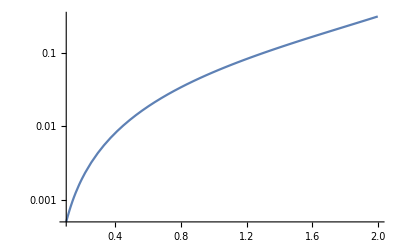

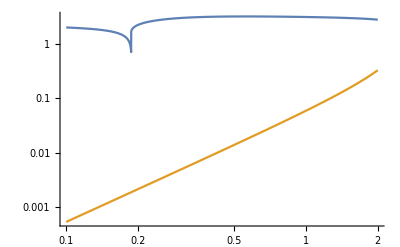

```mathematica
(*Loop factor for the aGG and aγγ couplings*)
LoopFactor[τ_]=1 - τ*Piecewise[{{ArcSin[1/(√τ)]^2,τ>=1},{(Pi/2+I/2 Log[(1+√(1+τ))/(1-√(1-τ))])^2,τ<1}}]
LogPlot[Abs[LoopFactor[(4*1.29^2)/ma^2]],{ma,0.1,2}]
(*Effective coupling of the ALP to photons and gluons - loop part*)
cGGeff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,quarklist_]:=Sum[Symbol["c"<>q]*LoopFactor[(4*MASS[q]^2)/ma^2],{q,quarklist}]
cGGtest1[ma_,cu_,cd_,cs_,cc_,cb_,ct_]=cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}];
cGGtest2[ma_,cu_,cd_,cs_,cc_,cb_,ct_]=cGGeff[ma,cu,cd,cs,cc,cb,ct,{"c","b","t"}];
LogLogPlot[{Abs[cGGtest1[ma,1,1,1,1,1,1]],Abs[cGGtest2[ma,1,1,1,1,1,1]]},{ma,0.1,2}]
(*Photon coupling*)
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,Λ_,"Loop c_G"]=-3cG αsData[ma]^2/Pi^2*Sum[CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2]Log[(Λ/If[MemberQ[{"u","d"},q]==True,MASS["π^0"],If[MemberQ[{"s"},q]==True,MASS["K^+"],MASS[q]]])^2],{q,{"u","d","s","c","b","t"}}];
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"Loop c_(q, all)"]=2*Sum[Symbol["c"<>q]*CHARGE[q]^2 3*LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"u","d","s","c","b"}}];
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"Loop c_(q, heavy)"]=2*Sum[Symbol["c"<>q]*CHARGE[q]^2 3*LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"c","b"}}];
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"Loop c_l"]=2*Sum[Symbol["c"<>l]*CHARGE[l]^2 LoopFactor[(4*MASS[l]^2)/ma^2],{l,{"e","μ","τ"}}];
```

## Running of flavor-diagonal couplings

### Definitions

```mathematica
couplingslist={(4*Pi*αTsol[μ]),αSsol[μ]^2,αSU2Lsol[μ]^2,αUYsol[μ]^2};
coefs["cG"]={2/(8 Pi^2),6/Pi^2,27/(16 Pi^2),11/(16 Pi^2)}couplingslist;
coefs["cW"]={(3*2)/(32 Pi^2),9/(2 Pi^2),27/(8 Pi^2),3/(8 Pi^2)}couplingslist;
coefs["cB"]={(17*2)/(96 Pi^2),11/(2 Pi^2),9/(8 Pi^2),95/(24 Pi^2)}couplingslist;
coefs["ct"]={9/(16 Pi^2),1/2 2/Pi^2,1/2 9/(16 Pi^2),1/2 17/(48 Pi^2)}couplingslist;
coefskeys=Keys[DownValues@coefs][[All,1,1]]
couplingsList[μ_]={RunningCoupling["ct",μ_],RunningCoupling["cG",μ_],RunningCoupling["cW",μ_],RunningCoupling["cB",μ_]}={CT[μ],CGG[μ],CWW[μ],CBB[μ]};
Do[cXXrunning[coef,μ_]=Evaluate[coefs[coef]]*couplingsList[μ]//Total,{coef,coefskeys}];
Nc=3;
cΛ["cG",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=cG+cu+cd+cs+cc+cb+ct;
cΛ["cW",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=cW+Nc/4*(cu+cd+cs+cc+cb+ct)+1/2(ce+cμ+cτ);
cΛ["cB",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=cB+2*Nc((2/3)^2(cu+cc+ct)+(1/3)^2(cb+cs+cd))-3/2*(cu+cc+ct)+3/2(ce+cμ+cτ);
cΛ["ct",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=ct;
cGcWcBctFlowTemp[Λ_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,cW_,cB_]:=Block[{},
NDSolve[Flatten[Table[{μ*D[RunningCoupling[coef,μ],μ]==cXXrunning[coef,μ],RunningCoupling[coef,Λ]==cΛ[coef,cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,cτ]},{coef,coefskeys}]],Evaluate[#[[0]]&/@couplingsList[μ]],{μ,MASS["t"],Λ}]
]
(*Running of Subscript[c, q!=t], Subscript[c, l]*)
β03=7;
(*the 2nd and 3rd terms: running from Λ to the top mass*)
(*the last term: running from top mass to μ = 2 GeV*)
cuRunning[Λ_,cu_,ct_,cG_,cd_,cs_,cc_,cb_]=cu-3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
cdRunning[Λ_,cd_,ct_,cG_,cu_,cs_,cc_,cb_]=cd+3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
csRunning[Λ_,cs_,ct_,cG_,cu_,cd_,cc_,cb_]=cs+3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
ccRunning[Λ_,cc_,ct_,cG_,cu_,cd_,cs_,cb_]=cc-3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
cbRunning[Λ_,cb_,ct_,cG_]=cb+3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*5/6*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi;
ceRunning[Λ_,ce_,ct_]=ce+3*αTsol[MASS["t"]]/αSsol[MASS["t"]](1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct;
cμRunning[Λ_,cμ_,ct_]=cμ+3*αTsol[MASS["t"]]/αSsol[MASS["t"]](1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct;
cτRunning[Λ_,cτ_,ct_]=cτ+3*αTsol[MASS["t"]]/αSsol[MASS["t"]](1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct;
ALPcouplingsRGflow[model_,Λ_]:=Module[{value},
Do[value[ALPcouplingslist[[i]]]=couplingPattern[model,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
sols=NDSolve[Flatten[Table[{μ*D[RunningCoupling[coef,μ],μ]==cXXrunning[coef,μ],RunningCoupling[coef,Λ]==cΛ[coef,value["cG"],value["cW"],value["cB"],value["cu"],value["cd"],value["cs"],value["cc"],value["cb"],value["ct"],value["ce"],value["cμ"],value["cτ"]]},{coef,coefskeys}]],Evaluate[#[[0]]&/@couplingsList[μ]],{μ,MASS["t"],Λ}][[1]];
RGflowTemp["ct"]=CT/.sols;
RGflow["ct"]=RGflowTemp["ct"][MASS["t"]];
RGflow["cW"]=value["cW"];
RGflow["cB"]=value["cB"];
RGflow["cG"]=value["cG"];
RGflow["cu"]=cuRunning[Λ,value["cu"],value["ct"],value["cG"],value["cd"],value["cs"],value["cc"],value["cb"]];
RGflow["cd"]=cdRunning[Λ,value["cd"],value["ct"],value["cG"],value["cu"],value["cs"],value["cc"],value["cb"]];
RGflow["cs"]=csRunning[Λ,value["cs"],value["ct"],value["cG"],value["cu"],value["cd"],value["cc"],value["cb"]];
RGflow["cc"]=ccRunning[Λ,value["cc"],value["ct"],value["cG"],value["cu"],value["cd"],value["cs"],value["cb"]];
RGflow["cb"]=cbRunning[Λ,value["cb"],value["ct"],value["cG"]];
RGflow["ce"]=ceRunning[Λ,value["ce"],value["ct"]];
RGflow["cμ"]=cμRunning[Λ,value["cμ"],value["ct"]];
RGflow["cτ"]=cτRunning[Λ,value["cτ"],value["ct"]];
Table[RGflow[coupling],{coupling,ALPcouplingslist}]
]
```

{cB,cG,ct,cW}

### RG flow computation/importing

```mathematica
ΛlistInt=Table[10^x,{x,Log10[MASS["t"]],Log10[10^9.],0.03}];
rgflowcomputoption=dropdownDialog[{"Generate","Import"},"Generate the RG flow of the ALP couplings, or just import it (if it has been generated once)?"];
If[rgflowcomputoption=="Generate",
Do[
rgflowlist[model]=Table[Join[{Λ},ALPcouplingsRGflow[model,Λ]],{Λ,ΛlistInt}];
Do[
cRGval[model,Λ_,ALPcouplingslist[[i]]]=Interpolation[rgflowlist[model][[All,{1,i+1}]],InterpolationOrder->1][Λ];
,{i,1,Length[ALPcouplingslist],1}];
tableValuesReplacement[model,Λ_]=Table[ALPcouplingsSymbols[[i]]->cRGval[model,Λ,ALPcouplingslist[[i]]]
,{i,1,Length[ALPcouplingsSymbols],1}];
,{model,ModelListAll}];
TabRGexport=Flatten[Table[{model,ALPcouplingslist[[i]],cRGval[model,Λ,ALPcouplingslist[[i]]]},{model,ModelListAll},{i,1,Length[ALPcouplingslist],1}],1];
Export[FileNameJoin[{NotebookDirectory[],"Temporary data/RGflowModels.m"}],TabRGexport,"MX"];
,
TabRGimport[Λ_]=Import[FileNameJoin[{NotebookDirectory[],"Temporary data/RGflowModels.m"}],"MX"];
Do[cRGval[TabRGimport[Λ][[i]][[1]],Λ_,TabRGimport[Λ][[i]][[2]]]=TabRGimport[Λ][[i]][[3]],{i,1,Length[TabRGimport[Λ]],1}]
]
Do[tableValuesReplacement[model,Λ_]=Table[ALPcouplingsSymbols[[i]]->cRGval[model,Λ,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingsSymbols],1}]
,{model,ModelListAll}]
```

### Plots and cross-checks

Benchmark | c_t = 1, other = 0 | c_G = 1, other = 0 | c_W  = 1, other = 0
c_t(μ_ω), this notebook | 0.801586 | -0.00286758 | -0.000112086
c_t(μ_ω), Neubert | 0.806918 | -0.003085 | -0.000115

Effect of the RG flow:

InterpolatingFunction::dmval: Input value {2.23805} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

(Coupling | cu | cd | cs | cc | cb | ct | cG | ce | cμ | cτ | cW | cB
Model Fermion universal, values at Λ = 100000 GeV | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0
Value below the EW scale | 0.767021 | 1.09298 | 1.09298 | 0.767021 | 1.13582 | 0.733275 | 0 | 1.16298 | 1.16298 | 1.16298 | 0 | 0)

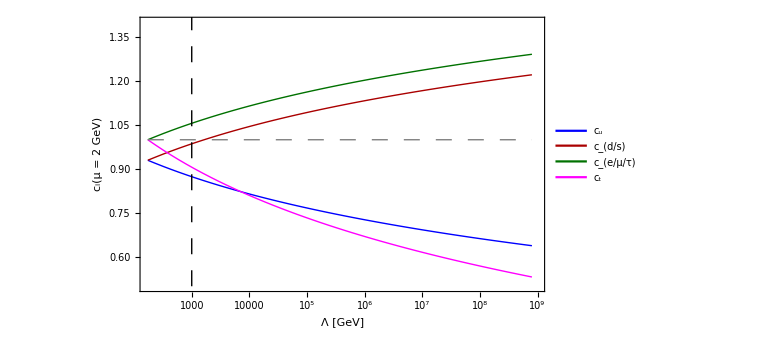

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\RG-flow.pdf

```mathematica
(*Cross-check: comparison with numeric expression from https://arxiv.org/pdf/2110.10698.pdf*)
ScaleNeubert=4*Pi*10^3;
posct=Position[ALPcouplingslist,"ct"][[1]][[1]];
ct1=Quiet[ALPcouplingsRGflow["Fermion universal",ScaleNeubert][[posct]]];
ct2=Quiet[ALPcouplingsRGflow["Gluon",ScaleNeubert][[posct]]];
ct3=Quiet[ALPcouplingsRGflow["W",ScaleNeubert][[posct]]];
(*Expression for Subscript[c, t] from Neubert's 2021 paper for Λ = 4π Tev*)
cttSolNeubert[cG_,cW_,cB_,cq_,cl_]=0.826*cq-1/2*10^-3(6.17*cΛ["cG",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]+0.23*cΛ["cW",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]+0.02cΛ["cB",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]);
{{"Benchmark","c_t = 1, other = 0", "c_G = 1, other = 0","c_W  = 1, other = 0"},{"c_t(μ_ω), this notebook",ct1,ct2,ct3},{"c_t(μ_ω), Neubert",cttSolNeubert[0,0,0,1,0],cttSolNeubert[1,0,0,0,0],cttSolNeubert[0,1,0,0,0]}}//TableForm
Print["Effect of the RG flow:"]
ModelTest="Fermion universal";
Λtest=10^5;
{Join[{"Coupling"},ALPcouplingslist],Join[{Row[{"Model ", ModelTest,", values at Λ = ",Λtest, " GeV"}]//ToString},couplingPatternOverall[ModelTest]],Join[{"Value below the EW scale"},ALPcouplingsRGflow["Fermion universal",Λtest]]}
(*Precomputed values of the ALP couplings at the RG scale μ = 2 GeV for the reference models and scales Λ*)
(*Plot*)
plotrg=Show[LogLinearPlot[{cRGval["Fermion universal",Λ,"cu"],cRGval["Fermion universal",Λ,"cd"],cRGval["Fermion universal",Λ,"ce"],cRGval["Fermion universal",Λ,"ct"],1},{Λ,MASS["t"],8*10^8},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Magenta},{Thick,Gray,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Darker@Green,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"Λ [GeV]" , "c_i(μ = 2 GeV)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{0.5,1.4}}(*,PlotLabel->Style[Row[{"Universal fermion coupling"}],22,Black]*),Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}},AspectRatio->0.6],LogLinearPlot[{100,100},{Λ,MASS["t"],8*10^8},PlotStyle->{{Thick,Blue},{Thick, Darker@Red}},PlotLegends->Placed[Style[#,22]&/@Join[{"c_u","c_(d/s)"}],{0.2,0.1}],Frame-> True,FrameLabel->{"Λ [GeV]" , "c_i(μ = 2 GeV)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{0.5,1.4}}],LogLinearPlot[{100,100},{Λ,MASS["t"],8*10^8},PlotStyle->{{Thick,Darker@Darker@Green},{Thick,Magenta}},PlotLegends->Placed[Style[#,22]&/@Join[{"c_(e/μ/τ)","c_t"}],{0.35,0.1}],Frame-> True,FrameLabel->{"Λ [GeV]" , "c_i(μ = 2 GeV)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{0.5,1.4}}],ListLogLinearPlot[Table[{10^3,a},{a,0.5,1.5,0.1}],Joined->True,PlotStyle->{{Thick,Black,Dashing[0.02]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/RG-flow.pdf"}],plotrg]
```

## Running of FCNC couplings

### Definitions

```mathematica
{ItIntegrandCoef["cG",μ_],ItIntegrandCoef["cW",μ_],ItIntegrandCoef["cB",μ_]}={(4 αSsol[μ]^2)/(3 Pi^2),(3 αSU2Lsol[μ]^2)/(8 Pi^2),(17 αUYsol[μ]^2)/(72 Pi^2)};
keysIT=Keys[DownValues@ItIntegrandCoef][[All,1,1]]//DeleteDuplicates;
Vtb=1;
Vts=41.5*10^-3.;
Vtd=8*10^-3;
{CKMsuppression["b->s"],CKMsuppression["b->d"],CKMsuppression["s->d"]}={Vtb*Vts,Vtb*Vtd,Vts*Vtd};
FCNCtransitions=Keys[DownValues@CKMsuppression][[All,1,1]];
xtv=MASS["t"]^2/80^2.;
cosθW=80/91.;
FCNCcouplingTemp[model_,Λ_]:=Block[{},
Do[value[ALPcouplingslist[[i]]]=couplingPattern[model,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
soltemp=NDSolve[Flatten[Table[{μ*D[RunningCoupling[coef,μ],μ]==cXXrunning[coef,μ],RunningCoupling[coef,Λ]==cΛ[coef,value["cG"],value["cW"],value["cB"],value["cu"],value["cd"],value["cs"],value["cc"],value["cb"],value["ct"],value["ce"],value["cμ"],value["cτ"]]},{coef,{"ct","cB","cW","cG"}}]],Evaluate[#[[0]]&/@couplingsList[μ]],{μ,MASS["t"],Λ}][[1]];
Do[runningSol[coef]=(RunningCoupling[coef,μ][[0]]/.soltemp),{coef,coefskeys}];
integrandIt[μ_]=1/μ(1-Exp[-18*Uval[MASS["t"],μ]])Sum[runningSol[coef][μ]*ItIntegrandCoef[coef,μ],{coef,keysIT}];
integralIt=-2/3(1-Exp[-18*Uval[MASS["t"],Λ]])2*runningSol["ct"][Λ]-NIntegrate[integrandIt[μ],{μ,Λ,MASS["t"]}];
-(1/6 integralIt+(4*Pi*αTsol[MASS["t"]])/(16 Pi^2)*(2*runningSol["ct"][MASS["t"]]*(1/4+3/2(1-xtv+Log[xtv])/(1-xtv)^2)+(3(1/137))/(2*Pi(1-cosθW^2))*cΛ["cW",value["cG"],value["cW"],value["cB"],value["cu"],value["cd"],value["cs"],value["cc"],value["cb"],value["ct"],value["ce"],value["cμ"],value["cτ"]]*(1-xtv+xtv*Log[xtv])/(1-xtv)^2))]
```

### RG flow computation/importing

```mathematica
If[rgflowcomputoption=="Generate",
Do[
FCNCcouplingList[model]=ParallelTable[{Λ,Quiet[FCNCcouplingTemp[model,Λ]]},{Λ,ΛlistInt}];
Do[FCNCcoupling[transition,model,Λ_]=CKMsuppression[transition]*Interpolation[FCNCcouplingList[model],InterpolationOrder->1][Λ];
cij[transition,model,Λ_,fa_]=1/fa FCNCcoupling[transition,model,Λ]*If[transition!="s->d",MASS["b"],MASS["s"]] 1/2;
,{transition,FCNCtransitions}];
,{model,ModelListAll}];
TableExportFCNCcouplings=Flatten[Table[{transition,model,FCNCcoupling[transition,model,Λ],cij[transition,model,Λ,fa]},{transition,FCNCtransitions},{model,ModelListAll}],1];
Export[FileNameJoin[{NotebookDirectory[],"Temporary data/FCNCcouplings.m"}],TableExportFCNCcouplings,"MX"],
TableImportFCNCcouplings=Import[FileNameJoin[{NotebookDirectory[],"Temporary data/FCNCcouplings.m"}],"MX"];
Do[
tran=TableImportFCNCcouplings[[i]][[1]];
mod=TableImportFCNCcouplings[[i]][[2]];
{FCNCcoupling[tran,mod,Λ_],cij[tran,mod,Λ_,fa_]}=Drop[TableImportFCNCcouplings[[i]],2],{i,1,Length[TableImportFCNCcouplings],1}];
]
```

### Plots and cross-checks

Coupling pattern | c_q = 1, c_l = 0, c_GG = 0, c_W = 0 | c_q = 0, c_l = 0, c_GG = 1, c_W = 0 | c_q = 0, c_l = 0, c_GG = 0, c_W = 1
c_bs, this notebook | 0.00163929 | -2.44798×10^-6 | -1.09814×10^-6
c_bs, Neubert | 0.00155662 | -2.5315×10^-6 | -1.162×10^-6

(Transition i->j | ALP model | scale Λ | |C_ij| (f_a = 1 GeV)
b->d | B | 1 TeV | 1.64104×10^-9
b->d | Fermion universal | 1 TeV | 0.000344463
b->d | Gluon | 1 TeV | 2.70586×10^-7
b->d | Gluon Aloni | 1 TeV | 1.35293×10^-7
b->d | Quark universal | 1 TeV | 0.000345156
b->d | W | 1 TeV | 4.57528×10^-7
b->d | B | EW | 3.1588×10^-26
b->d | Fermion universal | EW | 5.63141×10^-6
b->d | Gluon | EW | 6.84244×10^-24
b->d | Gluon Aloni | EW | 3.39012×10^-24
b->d | Quark universal | EW | 4.9592×10^-6
b->d | W | EW | 4.48137×10^-7
b->d | B | Neubert | 9.37085×10^-9
b->d | Fermion universal | Neubert | 0.000741831
b->d | Gluon | Neubert | 1.10896×10^-6
b->d | Gluon Aloni | Neubert | 5.54482×10^-7
b->d | Quark universal | Neubert | 0.000742619
b->d | W | Neubert | 4.97472×10^-7
b->s | B | 1 TeV | 8.51291×10^-9
b->s | Fermion universal | 1 TeV | 0.0017869
b->s | Gluon | 1 TeV | 1.40366×10^-6
b->s | Gluon Aloni | 1 TeV | 7.01831×10^-7
b->s | Quark universal | 1 TeV | 0.0017905
b->s | W | 1 TeV | 2.37343×10^-6
b->s | B | EW | 1.63863×10^-25
b->s | Fermion universal | EW | 0.0000292129
b->s | Gluon | EW | 3.54951×10^-23
b->s | Gluon Aloni | EW | 1.75862×10^-23
b->s | Quark universal | EW | 0.0000257259
b->s | W | EW | 2.32471×10^-6
b->s | B | Neubert | 4.86113×10^-8
b->s | Fermion universal | Neubert | 0.00384825
b->s | Gluon | Neubert | 5.75275×10^-6
b->s | Gluon Aloni | Neubert | 2.87638×10^-6
b->s | Quark universal | Neubert | 0.00385234
b->s | W | Neubert | 2.58064×10^-6
s->d | B | 1 TeV | 1.35337×10^-12
s->d | Fermion universal | 1 TeV | 2.84079×10^-7
s->d | Gluon | 1 TeV | 2.23152×10^-10
s->d | Gluon Aloni | 1 TeV | 1.11576×10^-10
s->d | Quark universal | 1 TeV | 2.84651×10^-7
s->d | W | 1 TeV | 3.77324×10^-10
s->d | B | EW | 2.60507×10^-29
s->d | Fermion universal | EW | 4.64423×10^-9
s->d | Gluon | EW | 5.64297×10^-27
s->d | Gluon Aloni | EW | 2.79584×10^-27
s->d | Quark universal | EW | 4.08986×10^-9
s->d | W | EW | 3.69579×10^-10
s->d | B | Neubert | 7.72816×10^-12
s->d | Fermion universal | Neubert | 6.11789×10^-7
s->d | Gluon | Neubert | 9.14565×10^-10
s->d | Gluon Aloni | Neubert | 4.57283×10^-10
s->d | Quark universal | Neubert | 6.1244×10^-7
s->d | W | Neubert | 4.10266×10^-10)

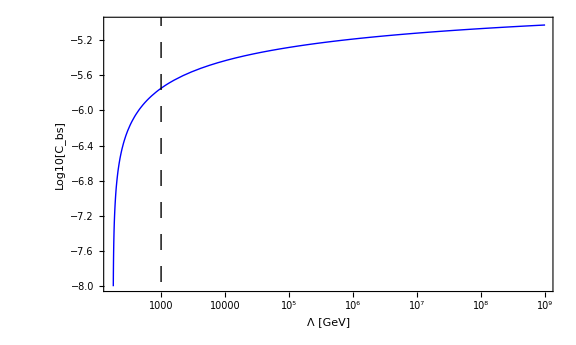

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\cbs-flow.pdf

```mathematica
(*Cross-check: comparison with numeric expression from https://arxiv.org/pdf/2110.10698.pdf*)
FCNCcouplingNeubert4PiTeV[transition_,cq_,cG_,cl_,cW_,cB_]:=CKMsuppression[transition]*(0.019*2*cq-6.1*10^-5 cΛ["cG",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]-2.8*10^-5 cΛ["cW",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]+1.8*10^-7 cΛ["cB",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl])
{{"Coupling pattern","c_q = 1, c_l = 0, c_GG = 0, c_W = 0","c_q = 0, c_l = 0, c_GG = 1, c_W = 0","c_q = 0, c_l = 0, c_GG = 0, c_W = 1"},{"c_bs, this notebook",FCNCcoupling["b->s","Quark universal",ScaleNeubert],FCNCcoupling["b->s","Gluon",ScaleNeubert],FCNCcoupling["b->s","W",ScaleNeubert]},{"c_bs, Neubert",FCNCcouplingNeubert4PiTeV["b->s",1,0,0,0,0],FCNCcouplingNeubert4PiTeV["b->s",0,1,0,0,0],FCNCcouplingNeubert4PiTeV["b->s",0,0,0,1,0]}}//TableForm
Join[{{"Transition i->j","ALP model","scale Λ","|C_ij| (f_a = 1 GeV)"}},Flatten[Table[{transition,model,scale,Abs[cij[transition,model,scaleVal[scale],1]]},{transition,FCNCtransitions},{scale,scaleKeys},{model,ModelListAll}],{1,2,3}]]
PlotcbsFlow=Show[LogLinearPlot[{Log10[cij["b->s","Fermion universal",Λ,10^3]]},{Λ,MASS["t"],10^9},PlotStyle->{{Thick,Blue},{Thick,Gray,Dashing[0.02]},{Thickness[0.002],Lighter@Blue},{Thick,Darker@Red},{Thickness[0.002],Lighter@Red},{Thickness[0.002],Lighter@Red},{Thick,Darker@Darker@Green},{Thickness[0.002],Lighter@Green},{Thickness[0.002],Lighter@Green},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"Λ [GeV]" , "Log10[C_bs]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{-8,-5}},Filling->{2->{{3},Directive[Blue,Opacity[0.1]]},5->{{6},Directive[Red,Opacity[0.1]]},8->{{9},Directive[Green,Opacity[0.1]]}}(*,PlotLabel->Style[Row[{"c_q = c_l = 1, f = 1 TeV"}],22,Black]*),AspectRatio->0.6],ListLogLogPlot[Table[{10^3,10^x},{x,-99,99,0.1}],Joined->True,PlotStyle->{{Thick,Black,Dashing[0.02]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/cbs-flow.pdf"}],PlotcbsFlow]
```

## ChPT (Standard model)

## List of meson fields, their conjugation and derivatives

### List of symbols for mesons

```mathematica
{PfieldSymbol["π^0",x_],PfieldSymbol["π^+",x_],PfieldSymbol["π^-",x_],PfieldSymbol["K^0",x_],PfieldSymbol["(K̄)^0",x_],PfieldSymbol["K^+",x_],PfieldSymbol["K^-",x_],PfieldSymbol["η",x_],PfieldSymbol["η'",x_], PfieldSymbol["a",x_]}={π0[x],πplus[x],πminus[x],K0[x],K0bar[x],Kplus[x],Kminus[x],η[x],ηpr[x],alp[x]};
{dPfieldSymbol["π^0",x_,μ_],dPfieldSymbol["π^+",x_,μ_],dPfieldSymbol["π^-",x_,μ_],dPfieldSymbol["K^0",x_,μ_],dPfieldSymbol["(K̄)^0",x_,μ_],dPfieldSymbol["K^+",x_,μ_],dPfieldSymbol["K^-",x_,μ_],dPfieldSymbol["η",x_,μ_],dPfieldSymbol["η'",x_,μ_],dPfieldSymbol["a",x_,μ_]}={dπ0[x,μ],dπplus[x,μ],dπminus[x,μ],dK0[x,μ],dK0bar[x,μ],dKplus[x,μ],dKminus[x,μ],dη[x,μ],dηpr[x,μ],dalp[x,μ]};
{VfieldSymbol["ρ^0",x_,μ_],VfieldSymbol["ρ^+",x_,μ_],VfieldSymbol["ρ^-",x_,μ_],VfieldSymbol["K^(*+)",x_,μ_],VfieldSymbol["K^(*-)",x_,μ_],VfieldSymbol["K^(*0)",x_,μ_],VfieldSymbol["(K̄)^(*0)",x_,μ_],VfieldSymbol["ϕ",x_,μ_],VfieldSymbol["ω",x_,μ_],VfieldSymbol["A",x_,μ_]}={ρ0[x,μ],ρplus[x,μ],ρminus[x,μ],Kstarplus[x,μ],Kstarminus[x,μ],Kstar0[x,μ],Kstar0bar[x,μ],ϕ[x,μ],ω[x,μ],A[x,μ]};
{dVfieldSymbol["ρ^0",x_,μ_,ν_],dVfieldSymbol["ρ^+",x_,μ_,ν_],dVfieldSymbol["ρ^-",x_,μ_,ν_],dVfieldSymbol["K^(*+)",x_,μ_,ν_],dVfieldSymbol["K^(*-)",x_,μ_,ν_],dVfieldSymbol["K^(*0)",x_,μ_,ν_],dVfieldSymbol["(K̄)^(*0)",x_,μ_,ν_],dVfieldSymbol["ϕ",x_,μ_,ν_],dVfieldSymbol["ω",x_,μ_,ν_],dVfieldSymbol["A",x_,μ_,ν_]}={dρ0[x,μ,ν],dρplus[x,μ,ν],dρminus[x,μ,ν],dKstarplus[x,μ,ν],dKstarminus[x,μ,ν],dKstar0[x,μ,ν],dKstar0bar[x,μ,ν],dϕ[x,μ,ν],dω[x,μ,ν],dA[x,μ,ν]};
(*Symbols for scalar mesons fields and their derivatives*)
{SfieldSymbol["σ",x_],SfieldSymbol["f_0",x_],SfieldSymbol["(a^0)_0",x_],SfieldSymbol["(a^+)_0",x_],SfieldSymbol["(a^-)_0",x_],SfieldSymbol["κ^0",x_],SfieldSymbol["(κ̄)^0",x_],SfieldSymbol["κ^+",x_],SfieldSymbol["κ^-",x_]}={σ[x],f0[x],a00[x],a0plus[x],a0minus[x],κ0[x],κ0bar[x],κplus[x],κminus[x]}
{dSfieldSymbol["σ",x_,μ_],dSfieldSymbol["f_0",x_,μ_],dSfieldSymbol["(a^0)_0",x_,μ_],dSfieldSymbol["(a^+)_0",x_,μ_],dSfieldSymbol["(a^-)_0",x_,μ_],dSfieldSymbol["κ^0",x_,μ_],dSfieldSymbol["(κ̄)^0",x_,μ_],dSfieldSymbol["κ^+",x_,μ_],dSfieldSymbol["κ^-",x_,μ_]}={dσ[x,μ],df0[x,μ],da00[x,μ],da0plus[x,μ],da0minus[x,μ],dκ0[x,μ],dκ0bar[x,μ],dκplus[x,μ],dκminus[x,μ]}
(*Symbols for tensor mesons fields and their derivatives*)
{TfieldSymbol["(a^0)_2",x_,μ_,ν_],TfieldSymbol["(a^+)_2",x_,μ_,ν_],TfieldSymbol["(a^-)_2",x_,μ_,ν_],TfieldSymbol["f_2",x_,μ_,ν_],TfieldSymbol["f'_2",x_,μ_,ν_],TfieldSymbol["(K^(*+))_2",x_,μ_,ν_],TfieldSymbol["(K^(*-))_2",x_,μ_,ν_],TfieldSymbol["(K^(*0))_2",x_,μ_,ν_],TfieldSymbol["((K̄)^(*0))_2",x_,μ_,ν_]}={a20[x,μ,ν],a2plus[x,μ,ν],a2minus[x,μ,ν],f2[x,μ,ν],f2pr[x,μ,ν],K2starplus[x,μ,ν],K2starminus[x,μ,ν],K2star0[x,μ,ν],K2star0bar[x,μ,ν]};
{dTfieldSymbol["(a^0)_2",x_,μ_,ν_,α_],dTfieldSymbol["(a^+)_2",x_,μ_,ν_,α_],dTfieldSymbol["(a^-)_2",x_,μ_,ν_,α_],dTfieldSymbol["f_2",x_,μ_,ν_,α_],dTfieldSymbol["f'_2",x_,μ_,ν_,α_],dTfieldSymbol["(K^(*+))_2",x_,μ_,ν_,α_],dTfieldSymbol["(K^(*-))_2",x_,μ_,ν_,α_],dTfieldSymbol["(K^(*0))_2",x_,μ_,ν_,α_],dTfieldSymbol["((K̄)^(*0))_2",x_,μ_,ν_,α_]}={da20[x,μ,ν,α],da2plus[x,μ,ν,α],da2minus[x,μ,ν,α],df2[x,μ,ν,α],df2pr[x,μ,ν,α],dK2starplus[x,μ,ν,α],dK2starminus[x,μ,ν,α],dK2star0[x,μ,ν,α],dK2star0bar[x,μ,ν,α]};
Print["List of P and V mesons:"]
listMesonV=DeleteDuplicates[Keys[DownValues[VfieldSymbol]][[All,1,1]]]
listMesonP=Select[DeleteDuplicates[Keys[DownValues[PfieldSymbol]][[All,1,1]]],#!="x"&]
listMesonS=Select[DeleteDuplicates[Keys[DownValues[SfieldSymbol]][[All,1,1]]],#!="x"&]
listMesonT=Select[DeleteDuplicates[Keys[DownValues[TfieldSymbol]][[All,1,1]]],#!="x"&]
listMesonVP=Join[listMesonV,listMesonP];
listMesonVPS=Join[listMesonV,listMesonP,listMesonS];
listMesonVPST=Join[listMesonV,listMesonP,listMesonS,listMesonT];
fieldslist=Join[listMesonP,listMesonT,listMesonS,listMesonV]
listMesonP0={"π^0","η","η'"};
listMesonP0a={"a","π^0","η","η'"};
Do[SpinParity[meson]=If[MemberQ[listMesonP,meson]==True,"P",If[MemberQ[listMesonS,meson]==True,"S",If[MemberQ[listMesonV,meson]==True,"V",If[MemberQ[listMesonT,meson]==True,"T"]]]],{meson,listMesonVPST}]
fieldSymbolTemp[meson_,"P"]:=PfieldSymbol[meson,x][[0]];
fieldSymbolTemp[meson_,"S"]:=SfieldSymbol[meson,x][[0]];
fieldSymbolTemp[meson_,"V"]:=VfieldSymbol[meson,x,μ][[0]]
fieldSymbolTemp[meson_,"T"]:=TfieldSymbol[meson,x,μ,ν][[0]]
fieldSymbol[meson_]:=fieldSymbolTemp[meson,SpinParity[meson]]
dfieldSymbolTemp[meson_,"P"]:=dPfieldSymbol[meson,x,α][[0]]
dfieldSymbolTemp[meson_,"S"]:=dSfieldSymbol[meson,x,α][[0]]
dfieldSymbolTemp[meson_,"V"]:=dVfieldSymbol[meson,x,μ,α][[0]]
dfieldSymbolTemp[meson_,"T"]:=dTfieldSymbol[meson,x,μ,ν,α][[0]]
dfieldSymbol[meson_]:=dfieldSymbolTemp[meson,SpinParity[meson]]
BreitWigner[m_,Γ_,s_]=m^2/(m^2-s-I*m*Γ);
```

{σ(x),f0(x),a00(x),a0plus(x),a0minus(x),κ0(x),κ0bar(x),κplus(x),κminus(x)}

{dσ(x,μ),df0(x,μ),da00(x,μ),da0plus(x,μ),da0minus(x,μ),dκ0(x,μ),dκ0bar(x,μ),dκplus(x,μ),dκminus(x,μ)}

List of P and V mesons:

{ρ^0,ρ^+,ρ^-,K^(*+),K^(*-),K^(*0),(K̄)^(*0),ϕ,ω,A}

{π^0,π^+,π^-,K^0,(K̄)^0,K^+,K^-,η,η',a}

{σ,f_0,(a^0)_0,(a^+)_0,(a^-)_0,κ^0,(κ̄)^0,κ^+,κ^-}

{(a^0)_2,(a^+)_2,(a^-)_2,f_2,f'_2,(K^(*+))_2,(K^(*-))_2,(K^(*0))_2,((K̄)^(*0))_2}

{π^0,π^+,π^-,K^0,(K̄)^0,K^+,K^-,η,η',a,(a^0)_2,(a^+)_2,(a^-)_2,f_2,f'_2,(K^(*+))_2,(K^(*-))_2,(K^(*0))_2,((K̄)^(*0))_2,σ,f_0,(a^0)_0,(a^+)_0,(a^-)_0,κ^0,(κ̄)^0,κ^+,κ^-,ρ^0,ρ^+,ρ^-,K^(*+),K^(*-),K^(*0),(K̄)^(*0),ϕ,ω,A}

### Replacement rules

#### Conjugation

```mathematica
(*Rules to replace conjugate meson fields*)
(*rule:={Conjugate[πplus]:>πminus,Conjugate[πminus]->πplus,Conjugate[Kminus]->Kplus,Conjugate[Kplus]->Kminus,Conjugate[π0]-> π0,Conjugate[eta]->eta,Conjugate[etapr]->etapr,Conjugate[K0]->K0bar, Conjugate[K0bar]->K0,Conjugate[fπ]->fπ}*)
Conjugate[πminus[x_]]^:=πplus[x]
Conjugate[πplus[x_]]^:=πminus[x]
Conjugate[Kminus[x_]]^:=Kplus[x]
Conjugate[Kplus[x_]]^:=Kminus[x]
Conjugate[η[x_]]^:=η[x]
Conjugate[ηpr[x_]]^:=ηpr[x]
Conjugate[π0[x_]]^:=π0[x]
Conjugate[alp[x_]]^:=alp[x]
Conjugate[K0[x_]]^:=K0bar[x]
Conjugate[K0bar[x_]]^:=K0[x]
Conjugate[dπminus[x_,μ_]]^:=dπplus[x,μ]
Conjugate[dπplus[x_,μ_]]^:=dπminus[x,μ]
Conjugate[dKminus[x_,μ_]]^:=dKplus[x,μ]
Conjugate[dKplus[x_,μ_]]^:=dKminus[x,μ]
Conjugate[dη[x_,μ_]]^:=dη[x,μ]
Conjugate[dηpr[x_,μ_]]^:=dηpr[x,μ]
Conjugate[dπ0[x_,μ_]]^:=dπ0[x,μ]
Conjugate[dK0[x_,μ_]]^:=dK0bar[x,μ]
Conjugate[dK0bar[x_,μ_]]^:=dK0[x,μ]
Conjugate[dalp[x_,μ_]]^:=dalp[x,μ]
(*For vector mesons*)
Conjugate[ρ0[x_,μ_]]^:=ρ0[x,μ]
Conjugate[ρminus[x_,μ_]]^:=ρplus[x,μ]
Conjugate[ρplus[x_,μ_]]^:=ρminus[x,μ]
Conjugate[Kstarplus[x_,μ_]]^:=Kstarminus[x,μ]
Conjugate[Kstarminus[x_,μ_]]^:=Kstarplus[x,μ]
Conjugate[Kstar0[x_,μ_]]^:=Kstar0bar[x,μ]
Conjugate[Kstar0bar[x_,μ_]]^:=Kstar0[x,μ]
Conjugate[ω[x_,μ_]]^:=ω[x,μ]
Conjugate[ϕ[x_,μ_]]^:=ϕ[x,μ]
Conjugate[A[x_,μ_]]^:=A[x,μ]
Conjugate[dρ0[x_,μ_,ν_]]^:=dρ0[x,μ,ν]
Conjugate[dρminus[x_,μ_,ν_]]^:=dρplus[x,μ,ν]
Conjugate[dρplus[x_,μ_,ν_]]^:=dρminus[x,μ,ν]
Conjugate[dKstarplus[x_,μ_,ν_]]^:=dKstarminus[x,μ,ν]
Conjugate[dKstarminus[x_,μ_,ν_]]^:=dKstarplus[x,μ,ν]
Conjugate[dKstar0[x_,μ_,ν_]]^:=dKstar0bar[x,μ,ν]
Conjugate[dKstar0bar[x_,μ_,ν_]]^:=dKstar0[x,μ,ν]
Conjugate[dω[x_,μ_,ν_]]^:=dω[x,μ,ν]
Conjugate[dϕ[x_,μ_,ν_]]^:=dϕ[x,μ,ν]
Conjugate[dA[x_,μ_,ν_]]^:=dA[x,μ,ν]
(*For scalar mesons*)
Conjugate[κplus[x_]]^:=κminus[x]
Conjugate[κminus[x_]]^:=κplus[x]
Conjugate[κ0[x_]]^:=κ0bar[x]
Conjugate[κ0bar[x_]]^:=κ0[x]
Conjugate[a00[x_]]^:=a00[x]
Conjugate[a0minus[x_]]^:=a0plus[x]
Conjugate[a0plus[x_]]^:=a0minus[x]
Conjugate[σ[x_]]^:=σ[x]
Conjugate[f0[x_]]^:=f0[x]
Conjugate[dκplus[x_,μ_]]^:=dκminus[x,μ]
Conjugate[dκminus[x_,μ_]]^:=dκplus[x,μ]
Conjugate[dκ0[x_,μ_]]^:=dκ0bar[x,μ]
Conjugate[dκ0bar[x_,μ_]]^:=dκ0[x,μ]
Conjugate[da00[x_,μ_]]^:=da00[x,μ]
Conjugate[da0minus[x_,μ_]]^:=da0plus[x,μ]
Conjugate[da0plus[x_,μ_]]^:=da0minus[x,μ]
Conjugate[dσ[x_,μ_]]^:=dσ[x,μ]
Conjugate[df0[x_,μ_]]^:=df0[x,μ]
(*For tensor mesons*)
Conjugate[K2starplus[x_,μ_,ν_]]^:=K2starminus[x,μ,ν]
Conjugate[K2starminus[x_,μ_,ν_]]^:=K2starplus[x,μ,ν]
Conjugate[K2star0[x_,μ_,ν_]]^:=K2star0bar[x,μ,ν]
Conjugate[K2star0bar[x_,μ_,ν_]]^:=K2star0[x,μ,ν]
Conjugate[a20[x_,μ_,ν_]]^:=a20[x,μ,ν]
Conjugate[a2minus[x_,μ_,ν_]]^:=a2plus[x,μ,ν]
Conjugate[a2plus[x_,μ_,ν_]]^:=a2minus[x,μ,ν]
Conjugate[f2[x_,μ_,ν_]]^:=f2[x,μ,ν]
Conjugate[f2pr[x_,μ_,ν_]]^:=f2pr[x,μ,ν]
Conjugate[dK2starplus[x_,μ_,ν_,α_]]^:=dK2starminus[x,μ,ν,α]
Conjugate[dK2starminus[x_,μ_,ν_,α_]]^:=dK2starplus[x,μ,ν,α]
Conjugate[dK2star0[x_,μ_,ν_,α_]]^:=dK2star0bar[x,μ,ν,α]
Conjugate[dK2star0bar[x_,μ_,ν_,α_]]^:=dK2star0[x,μ,ν,α]
Conjugate[da20[x_,μ_,ν_,α_]]^:=da20[x,μ,ν,α]
Conjugate[da2minus[x_,μ_,ν_,α_]]^:=da2plus[x,μ,ν,α]
Conjugate[da2plus[x_,μ_,ν_,α_]]^:=da2minus[x,μ,ν,α]
Conjugate[df2[x_,μ_,ν_,α_]]^:=df2[x,μ,ν,α]
Conjugate[df2pr[x_,μ_,ν_,α_]]^:=df2pr[x,μ,ν,α]
(*For parameters*)
Conjugate[stheta]^:=stheta
Conjugate[ctheta]^:=ctheta
fπ/:Conjugate[fπ]:=fπ
stheta/:stheta^2:=1-ctheta^2
```

#### Symbols for conjugated fields

```mathematica
findingConjugatedTemp[S_,"S"]:=Module[{Sconj},
Do[If[SfieldSymbol[S1,x]==Conjugate[SfieldSymbol[S,x]],Sconj=S1; Break[]],{S1,listMesonS}];
Sconj
]
findingConjugatedTemp[V_,"V"]:=Module[{Vconj},
Do[If[VfieldSymbol[V1,x,μ]==Conjugate[VfieldSymbol[V,x,μ]],Vconj=V1; Break[]],{V1,listMesonV}];
Vconj
]
findingConjugatedTemp[P_,"P"]:=Module[{Pconj},
Do[If[PfieldSymbol[P1,x]==Conjugate[PfieldSymbol[P,x]],Pconj=P1; Break[]],{P1,listMesonP}];
Pconj
]
findingConjugatedTemp[T_,"T"]:=Module[{Tconj},
Do[If[TfieldSymbol[T1,x,μ,ν]==Conjugate[TfieldSymbol[T,x,μ,ν]],Tconj=T1; Break[]],{T1,listMesonT}];
Tconj
]
findingConjugated[meson_]:=findingConjugatedTemp[meson,SpinParity[meson]]
```

#### Derivatives

```mathematica
(*Rules for derivatives*)
(*D[ϕ[x[ν_],μ_],x[ν_]]^:=dϕ[x,μ,ν]
D[ω[x_,μ_],x[ν_]]^:=dω[x,μ,ν]
D[ρ0[x_,μ_],x[ν_]]^:=dρ0[x,μ,ν]
D[ρplus[x_,μ_],x[ν_]]^:=dρplus[x,μ,ν]
D[ρminus[x_,μ_],x[ν_]]^:=dρminus[x,μ,ν]
D[Kstarplus[x_,μ_],x[ν_]]^:=dKstarplus[x,μ,ν]
D[Kstarminus[x_,μ_],x[ν_]]^:=dKstarminus[x,μ,ν]
D[Kstar0[x_,μ_],x[ν_]]^:=dKstar0[x,μ,ν]
D[Kstar0bar[x_,μ_],x[ν_]]^:=dKstar0bar[x,μ,ν]*)
DerivativesReplacementRuleV[μ_,ν_]:=Table[D[VfieldSymbol[meson,x,ν],x]->dVfieldSymbol[meson,x,μ,ν],{meson,listMesonV}]
DerivativesReplacementRulePS[μ_]:=Join[Table[D[PfieldSymbol[meson,x],x]->dPfieldSymbol[meson,x,μ],{meson,listMesonP}],Table[D[SfieldSymbol[meson,x],x]->dSfieldSymbol[meson,x,μ],{meson,listMesonP}]]
DerivativesReplacementRuleT[μ_,ν_,α_]:=Table[D[TfieldSymbol[meson,x,ν,α],x]->dTfieldSymbol[meson,x,μ,ν,α],{meson,listMesonT}]
```

### Simplifications of the Lagrangian

```mathematica
(*A function that takes the expression and leaves only terms up to the linear order in the ALP and Subscript[f^-1, a]*)
indiceslist={μ,ν,α,β};
(*onlyLinearalp[expression_]:=Block[{},
(*First, only terms ~a^0 or a^1 are left*)
val1=(expression/.{alp[x]->0,dalp[x,a_]:>0})+alp[x]*(D[(expression),alp[x]]/.{alp[x]->0,dalp[x,a_]:>0})+Sum[dalp[x,indiceslist[[i]]](D[expression,dalp[x,indiceslist[[i]]]]/.{alp[x]->0,dalp[x,a_]:>0}),{i,1,Length[indiceslist],1}]//Expand(*//Simplify*);
(*Terms that does not contain ALP and hence are proportional to Subscript[f^0, a]*)
(*val11=val1-(expression/.{alp[x]->0,dalp[x,a_]:>0})//Expand;*)
(*Total expression - terms up to a^1 and only up to Subscript[f^-1, a]*)
Limit[val1,fa->Infinity]+1/fa Limit[fa*(val1-Limit[val1,fa->Infinity]//Expand),fa->Infinity]
]*)
ruleFieldsToZero:=Join[Table[PfieldSymbol[meson,x_]:>0,{meson,listMesonP}],Table[dPfieldSymbol[meson,x_,μ_]:>0,{meson,listMesonP}],Table[VfieldSymbol[meson,x_,μ_]:>0,{meson,listMesonV}],Table[dVfieldSymbol[meson,x_,μ_,ν_]:>0,{meson,listMesonV}],Table[SfieldSymbol[meson,x_]:>0,{meson,listMesonS}],Table[dSfieldSymbol[meson,x_,μ_]:>0,{meson,listMesonS}],Table[TfieldSymbol[meson,x_,μ_,ν_]:>0,{meson,listMesonT}],Table[dTfieldSymbol[meson,x_,μ_,α_,β_]:>0,{meson,listMesonT}]]
(*A function leaving terms with fields only up to nth power*)
ruleLeavingPower[expr_,n_]:=(Normal@Series[expr/. {factor:_[x]|_[x,a_]|_[x,a_,b_]|_[x,a_,b_,c_]:>factor*$T},{$T,0,n}]/. {$T->1})-(Normal@Series[expr/. {factor:_[x]|_[x,a_]|_[x,a_,b_]|_[x,a_,b_,c_]:>factor*$T},{$T,0,0}]/. {$T->1})
ruleExpansionPfield[expr_,field_,n_]:=(Normal@Series[expr/. {factor:PfieldSymbol[field,x]|dPfieldSymbol[field,x,a_]:>factor*$T},{$T,0,n}]/. {$T->1})
ruleOnlyLinearALP[expr_]:=Block[{},
temp1=ruleExpansionPfield[expr,"a",1];
temp2=Normal@Series[temp1,{ϵ,0,1}]
]
ruleLinearALPtermsOnly[expr_]:=Block[{},
temp1=ruleExpansionPfield[expr,"a",1]-ruleExpansionPfield[expr,"a",0]//Expand;
temp2=Normal@Series[temp1,{ϵ,0,1}]
]
(*This is the expansion in terms of ϵ = Subscript[f, π]/Subscript[f, a] and δ = (Subscript[m, d] - Subscript[m, u])/(Subscript[m, d]+Subscript[m, u])*)
ruleLeadingOrderIsospin[expr_]:=(Normal@Series[expr/. {factor:δ:>factor*$T},{$T,0,1}]/. {$T->1})
ruleIsospinBreakingExpansion[expr_,n_]:=(Normal@Series[expr/. {factor:δ:>factor*$T},{$T,0,n}]/. {$T->1})
ruleLeavingPowerConstants[expr_]:=(Normal@Series[expr/. {factor:ϵ|δ:>factor*$T},{$T,0,1}]/. {$T->1})
ruleOnlyFields[fieldlist_]:=Join[Flatten[Table[{PfieldSymbol[meson,x]->0,dPfieldSymbol[meson,x,a_]:>0},{meson,Select[listMesonP,MemberQ[fieldlist,#]==False&]}],1],Flatten[Table[{VfieldSymbol[meson,x,a_]:>0,dVfieldSymbol[meson,x,a_,b_]:>0},{meson,Select[listMesonV,MemberQ[fieldlist,#]==False&]}],1],Flatten[Table[{SfieldSymbol[meson,x]->0,dSfieldSymbol[meson,x,a_]:>0},{meson,Select[listMesonS,MemberQ[fieldlist,#]==False&]}],1],Flatten[Table[{TfieldSymbol[meson,x,a_,b_]:>0,dTfieldSymbol[meson,x,a_,b_,c_]:>0},{meson,Select[listMesonT,MemberQ[fieldlist,#]==False&]}],1]]
```

## Relevant matrices, etc.

### Charge matrix, parameters

```mathematica
(*Pseudoscalar mesons mass Lagrangian coefficient - parametric expression*)
B0=mπ0^2/(mu+md);
(*Quark electric charge matrix*)
Qmatrix=1/3 DiagonalMatrix[{2,-1,-1}];
(*Quark mass matrix in SM*)
mQuark["SM"]=DiagonalMatrix[{mu,md,ms}];
(*Matrix used in the chiral rotation to eliminate the ALP GG coupling*)
κmatrix=DiagonalMatrix[{mu^-1,md^-1,ms^-1}]/(mu^-1+md^-1+ms^-1);
(*θη=ArcSin[-1/3];*)
(*Relation between eta^0,eta^8 and the mass eigenstates eta,eta'*)
etasols=(Solve[{η[x]==Cos[θη]eta8-Sin[θη]eta0,ηpr[x]==Sin[θη]eta8+Cos[θη]eta0},{eta0,eta8}][[1]]//Simplify)/.{Sin[θη]->stheta,Cos[θη]->ctheta}
(*___________________________________________*)
(*Mixing angle defining mass eigenstates η,η'*)
(*___________________________________________*)
θηStandard=ArcSin[-1/3];
θηTrue=-13*Pi/180.;
```

{eta0→ctheta ηpr(x)-stheta η(x),eta8→ctheta η(x)+stheta ηpr(x)}

### Meson matrices

```mathematica
(*Pseudoscalar meson matrix - no ALP. The normalizaton fixes Subscript[f, π] = 93 MeV*)
Pmatrix[x_,"SM"]=1/Sqrt[2]{{π0[x]/(√2)+1/(√6)(eta8/.etasols)+1/(√3)(eta0/.etasols),πplus[x],Kplus[x]},{πminus[x],-π0[x]/(√2)+1/(√6)(eta8/.etasols)+1/(√3)(eta0/.etasols),K0[x]},{Kminus[x],K0bar[x],-√(2/3)(eta8/.etasols)+1/(√3)(eta0/.etasols)}}//Expand
dPmatrix[x_,μ_,"SM"]=D[Pmatrix[x,"SM"],x]/.Evaluate[DerivativesReplacementRulePS[μ]];
(*Σ matrix expanded up to second order*)
Σ4[x_,"SM"]=IdentityMatrix[3]+(2*I)/fπ*Pmatrix[x,"SM"]+1/2((2*I)/fπ)^2*Pmatrix[x,"SM"].Pmatrix[x,"SM"]+1/(3!)((2*I)/fπ)^3 Pmatrix[x,"SM"].Pmatrix[x,"SM"].Pmatrix[x,"SM"]+1/(4!)((2*I)/fπ)^4 Pmatrix[x,"SM"].Pmatrix[x,"SM"].Pmatrix[x,"SM"].Pmatrix[x,"SM"]//Expand;
Σ4HC[x_,"SM"]=(ConjugateTranspose[Σ4[x,"SM"]]//ComplexExpand);
Σ1[x_,"SM"]=IdentityMatrix[3]+(2*I)/fπ*Pmatrix[x,"SM"]//Expand;
Σ1HC[x_,"SM"]=(ConjugateTranspose[Σ1[x,"SM"]]//ComplexExpand);
Σ2[x_,"SM"]=IdentityMatrix[3]+(2*I)/fπ*Pmatrix[x,"SM"]+1/2((2*I)/fπ)^2*Pmatrix[x,"SM"].Pmatrix[x,"SM"]//Expand;
Σ2HC[x_,"SM"]=(ConjugateTranspose[Σ2[x,"SM"]]//ComplexExpand);
(*Its derivatives*)
dΣ1[x_,μ_,"SM"]=(D[Σ1[x,"SM"],x]/.Evaluate[DerivativesReplacementRulePS[μ]])//Expand;
dΣ1HC[x_,μ_,"SM"]=(ConjugateTranspose[dΣ1[x,μ,"SM"]]//ComplexExpand);
dΣ2[x_,μ_,"SM"]=(D[Σ2[x,"SM"],x]/.Evaluate[DerivativesReplacementRulePS[μ]])//Expand;
dΣ2HC[x_,μ_,"SM"]=(ConjugateTranspose[dΣ2[x,μ,"SM"]]//ComplexExpand);
dΣ4[x_,μ_,"SM"]=(D[Σ4[x,"SM"],x]/.Evaluate[DerivativesReplacementRulePS[μ]])//Expand;
dΣ4HC[x_,μ_,"SM"]=(ConjugateTranspose[dΣ4[x,μ,"SM"]]//ComplexExpand);
(*Its covariant derivatives*)
DΣ2[x_,μ_,"SM"]=dΣ2[x,μ,"SM"]+I*e*A[x,μ](Qmatrix.Σ2[x,"SM"]-Σ2[x,"SM"].Qmatrix);
DΣ2HC[x_,μ_,"SM"]=dΣ2HC[x,μ,"SM"]+I*e*A[x,μ](Qmatrix.Σ2HC[x,"SM"]-Σ2HC[x,"SM"].Qmatrix);
DΣ4[x_,μ_,"SM"]=dΣ4[x,μ,"SM"]+I*e*A[x,μ](Qmatrix.Σ4[x,"SM"]-Σ4[x,"SM"].Qmatrix);
DΣ4HC[x_,μ_,"SM"]=dΣ4HC[x,μ,"SM"]+I*e*A[x,μ](Qmatrix.Σ4HC[x,"SM"]-Σ4HC[x,"SM"].Qmatrix);
(*Vector mesons matrices*)
Vmatrix[x_,μ_]=1/(√2){{(ρ0[x,μ]+ω[x,μ])/(√2),ρplus[x,μ],Kstarplus[x,μ]},{ρminus[x,μ],(-ρ0[x,μ]+ω[x,μ])/(√2),Kstar0[x,μ]},{Kstarminus[x,μ],Kstar0bar[x,μ],ϕ[x,μ]}};
dVmatrix[x_,μ_,ν_]=D[Vmatrix[x,ν],x]/.Evaluate[DerivativesReplacementRuleV[μ,ν]]
VstrengthMatrix[x_,μ_,ν_]=dVmatrix[x,μ,ν]-dVmatrix[x,ν,μ];
(*Tensor mesons matrices*)
Tmatrix[x_,μ_,ν_]={{a20[x,μ,ν]/(√2)+f2[x,μ,ν]/(√2),a2plus[x,μ,ν],K2starplus[x,μ,ν]},{a2minus[x,μ,ν],-a20[x,μ,ν]/(√2)+f2[x,μ,ν]/(√2),K2star0[x,μ,ν]},{K2starminus[x,μ,ν],K2star0bar[x,μ,ν],f2pr[x,μ,ν]}}
```

((ctheta η(x))/(2 √3)+(ctheta ηpr(x))/(√6)-(stheta η(x))/(√6)+(stheta ηpr(x))/(2 √3)+(π0(x))/2 | (πplus(x))/(√2) | (Kplus(x))/(√2)
(πminus(x))/(√2) | (ctheta η(x))/(2 √3)+(ctheta ηpr(x))/(√6)-(stheta η(x))/(√6)+(stheta ηpr(x))/(2 √3)-(π0(x))/2 | (K0(x))/(√2)
(Kminus(x))/(√2) | (K0bar(x))/(√2) | -(ctheta η(x))/(√3)+(ctheta ηpr(x))/(√6)-(stheta η(x))/(√6)-(stheta ηpr(x))/(√3))

(1/2 (dρ0(x,μ,ν)+dω(x,μ,ν)) | (dρplus(x,μ,ν))/(√2) | (dKstarplus(x,μ,ν))/(√2)
(dρminus(x,μ,ν))/(√2) | 1/2 (dω(x,μ,ν)-dρ0(x,μ,ν)) | (dKstar0(x,μ,ν))/(√2)
(dKstarminus(x,μ,ν))/(√2) | (dKstar0bar(x,μ,ν))/(√2) | (dϕ(x,μ,ν))/(√2))

((a20(x,μ,ν))/(√2)+(f2(x,μ,ν))/(√2) | a2plus(x,μ,ν) | K2starplus(x,μ,ν)
a2minus(x,μ,ν) | (f2(x,μ,ν))/(√2)-(a20(x,μ,ν))/(√2) | K2star0(x,μ,ν)
K2starminus(x,μ,ν) | K2star0bar(x,μ,ν) | f2pr(x,μ,ν))

#### Meson generators

```mathematica
(*Generators for pseudoscalar mesons*)
Do[MesonGenerator[meson]=D[Pmatrix[x,"SM"],PfieldSymbol[meson,x]],{meson,listMesonP}]
(*{MesonGenerator["π^0"],MesonGenerator["η"],MesonGenerator["η'"],MesonGenerator["K^+"],MesonGenerator["K^-"]}=D[Pmatrix[x],#]&/@{π0[x],η[x],ηpr[x],Kplus[x],Kminus[x]};*)
(*Generators for vector mesons*)
Do[MesonGenerator[meson]=D[Vmatrix[x,μ],VfieldSymbol[meson,x,μ]],{meson,listMesonV}]
(*Generators for scalar mesons*)
{MesonGenerator["σ"],MesonGenerator["f_0"],MesonGenerator["a_0"]}={1/(√22)DiagonalMatrix[{√5,√5,1}],1/(2 √5)DiagonalMatrix[{1,1,-2 √2}],1/2 DiagonalMatrix[{1,-1,0}]};
(*Generators for tensor mesons*)
MesonGenerator["f2"]=1/2 DiagonalMatrix[{1,1,0}];
Print["List of all considered mesons:"]
keysMesonGenerator=Keys[DownValues[MesonGenerator]][[All,1,1]]
MesonGenerator["η"]/.{stheta->Sin[θηStandard],ctheta->Cos[θηStandard]}//Simplify
```

List of all considered mesons:

{a,A,f2,a_0,f_0,K^-,K^+,K^(*-),K^(*+),K^(*0),K^0,(K̄)^(*0),(K̄)^0,π^-,π^+,π^0,ρ^-,ρ^+,ρ^0,η,η',σ,ϕ,ω}

(1/(√6) | 0 | 0
0 | 1/(√6) | 0
0 | 0 | -1/(√6))

## Fixing the hard QCD η_0 mass term

```mathematica
MassTermη0=-m02/2(eta0/.etasols)^2
Print["ChPT mass term with the parameter m_0:"]
MassTermChPTtemp=ruleLeavingPower[fπ^2/2 B0*Tr[(Σ2[x,"SM"].mQuark["SM"]+mQuark["SM"].Σ2HC[x,"SM"])]+MassTermη0,2]//Expand
Print["The mixing between eta and eta' (d^2L/dηdη'):"]
Mixingetaetapr=D[D[MassTermChPTtemp,η[x]],ηpr[x]](*/.{stheta->Sin[θη],ctheta->Cos[θη]}*)//Simplify
Print["The value of m_0 for which the mixing vanishes:"]
m02val=(m02/.Solve[Mixingetaetapr==0,m02][[1]]//Simplify)/.{stheta^2->1-ctheta^2}
MassTermChPTtemp1=MassTermChPTtemp/.{m02->m02val}(*/.{stheta->-√(1-ctheta^2)}*)//Simplify;
Print["Mass matrix for the mesons - parametric form:"]
Do[Mm0m0[meson1,meson2]=-D[D[MassTermChPTtemp1,PfieldSymbol[meson1,x]],PfieldSymbol[meson2,x]]//Simplify,{meson1,listMesonP0},{meson2,listMesonP0}]
Table[Mm0m0[meson1,meson2],{meson1,listMesonP0},{meson2,listMesonP0}]
Print["Numeric values (GeV^2):"]
ParametersToNumbers:={fπ->Fπ,mπ0->MASS["π^0"],mu->MASS["u"],md->MASS["d"],ms->MASS["s"],ctheta->Cos[θηTrue],stheta->Sin[θηTrue]}
Table[Mm0m0[meson1,meson2],{meson1,listMesonP0},{meson2,listMesonP0}]/.Evaluate[ParametersToNumbers]
Print["Masses of eta and eta' obtained from these calculations:"]
{{"Meson","η","η'"},{"Mass in GeV",√Mm0m0["η","η"],√Mm0m0["η'","η'"]}}/.Evaluate[ParametersToNumbers]
(*Expressions for Subscript[M, mm] similar to Eq. S4 from https://arxiv.org/pdf/1811.03474.pdf*)
Do[Mm0m0Red[meson1,meson2]=If[meson1==meson2,1,(md+mu)/(md-mu)]*Mm0m0[meson1,meson2],{meson1,listMesonP0},{meson2,listMesonP0}]
{Mm0m0Red["π^0","η"]/(√2),Mm0m0Red["π^0","η'"],-Mm0m0Red["π^0","π^0"]/(√3)};
Print["ChPT mass term in symbolic form following the notation of Eq. S4 from https://arxiv.org/pdf/1811.03474.pdf, with δ_I = (m_d-m_u)/(m_d+m_u):"]
MassTermChPTsymbolic=-1/2{π0[x],η[x],ηpr[x]}.{{mπ0^2,δI*Mπ0η,δI*Mπ0ηpr},{δI*Mπ0η,mη^2,0},{δI*Mπ0ηpr,0,mηpr^2}}.{π0[x],η[x],ηpr[x]}//Expand//Simplify
```

-1/2 m02 (ctheta ηpr(x)-stheta η(x))^2

ChPT mass term with the parameter m_0:

(√2 ctheta md stheta (η(x))^2 mπ0^2)/(3 (md+mu))-(2 √2 ctheta ms stheta (η(x))^2 mπ0^2)/(3 (md+mu))+(√2 ctheta mu stheta (η(x))^2 mπ0^2)/(3 (md+mu))+(ctheta^2 md (η(x))^2 mπ0^2)/(6 (md+mu))-(md (η(x))^2 mπ0^2)/(3 (md+mu))-(ctheta^2 ms (η(x))^2 mπ0^2)/(3 (md+mu))-(ms (η(x))^2 mπ0^2)/(3 (md+mu))+(ctheta^2 mu (η(x))^2 mπ0^2)/(6 (md+mu))-(mu (η(x))^2 mπ0^2)/(3 (md+mu))-(√2 ctheta md stheta (ηpr(x))^2 mπ0^2)/(3 (md+mu))+(2 √2 ctheta ms stheta (ηpr(x))^2 mπ0^2)/(3 (md+mu))-(√2 ctheta mu stheta (ηpr(x))^2 mπ0^2)/(3 (md+mu))-(ctheta^2 md (ηpr(x))^2 mπ0^2)/(6 (md+mu))-(md (ηpr(x))^2 mπ0^2)/(6 (md+mu))+(ctheta^2 ms (ηpr(x))^2 mπ0^2)/(3 (md+mu))-(2 ms (ηpr(x))^2 mπ0^2)/(3 (md+mu))-(ctheta^2 mu (ηpr(x))^2 mπ0^2)/(6 (md+mu))-(mu (ηpr(x))^2 mπ0^2)/(6 (md+mu))-(md (π0(x))^2 mπ0^2)/(2 (md+mu))-(mu (π0(x))^2 mπ0^2)/(2 (md+mu))-(md K0(x) K0bar(x) mπ0^2)/(md+mu)-(ms K0(x) K0bar(x) mπ0^2)/(md+mu)-(ms Kminus(x) Kplus(x) mπ0^2)/(md+mu)-(mu Kminus(x) Kplus(x) mπ0^2)/(md+mu)+(ctheta md stheta η(x) ηpr(x) mπ0^2)/(3 (md+mu))-(2 ctheta ms stheta η(x) ηpr(x) mπ0^2)/(3 (md+mu))+(ctheta mu stheta η(x) ηpr(x) mπ0^2)/(3 (md+mu))-(2 √2 ctheta^2 md η(x) ηpr(x) mπ0^2)/(3 (md+mu))+(√2 md η(x) ηpr(x) mπ0^2)/(3 (md+mu))+(4 √2 ctheta^2 ms η(x) ηpr(x) mπ0^2)/(3 (md+mu))-(2 √2 ms η(x) ηpr(x) mπ0^2)/(3 (md+mu))-(2 √2 ctheta^2 mu η(x) ηpr(x) mπ0^2)/(3 (md+mu))+(√2 mu η(x) ηpr(x) mπ0^2)/(3 (md+mu))-(√(2/3) md stheta η(x) π0(x) mπ0^2)/(md+mu)+(√(2/3) mu stheta η(x) π0(x) mπ0^2)/(md+mu)+(ctheta md η(x) π0(x) mπ0^2)/(√3 (md+mu))-(ctheta mu η(x) π0(x) mπ0^2)/(√3 (md+mu))+(md stheta ηpr(x) π0(x) mπ0^2)/(√3 (md+mu))-(mu stheta ηpr(x) π0(x) mπ0^2)/(√3 (md+mu))+(√(2/3) ctheta md ηpr(x) π0(x) mπ0^2)/(md+mu)-(√(2/3) ctheta mu ηpr(x) π0(x) mπ0^2)/(md+mu)-(md πminus(x) πplus(x) mπ0^2)/(md+mu)-(mu πminus(x) πplus(x) mπ0^2)/(md+mu)+1/2 ctheta^2 m02 (η(x))^2-1/2 m02 (η(x))^2-1/2 ctheta^2 m02 (ηpr(x))^2+ctheta m02 stheta η(x) ηpr(x)

The mixing between eta and eta' (d^2L/dηdη'):

(md mπ0^2 (-2 √2 ctheta^2+ctheta stheta+√2)+2 mπ0^2 ms (2 √2 ctheta^2-ctheta stheta-√2)+mπ0^2 mu (-2 √2 ctheta^2+ctheta stheta+√2)+3 ctheta m02 md stheta+3 ctheta m02 mu stheta)/(3 (md+mu))

The value of m_0 for which the mixing vanishes:

(mπ0^2 (2 √2 ctheta^2-ctheta stheta-√2) (md-2 ms+mu))/(3 ctheta stheta (md+mu))

Mass matrix for the mesons - parametric form:

(mπ0^2 | -(mπ0^2 (√2 ctheta^2+ctheta stheta-√2) (md-mu))/(√3 stheta (md+mu)) | (mπ0^2 (ctheta^2-√2 ctheta stheta-1) (md-mu))/(√3 stheta (md+mu))
-(mπ0^2 (√2 ctheta^2+ctheta stheta-√2) (md-mu))/(√3 stheta (md+mu)) | (mπ0^2 (md (√2 ctheta^2+ctheta stheta-√2)+ms (-2 √2 ctheta^2+4 ctheta stheta+2 √2)+mu (√2 ctheta^2+ctheta stheta-√2)))/(3 ctheta stheta (md+mu)) | 0
(mπ0^2 (ctheta^2-√2 ctheta stheta-1) (md-mu))/(√3 stheta (md+mu)) | 0 | (mπ0^2 (√2 ctheta (md-2 ms+mu)+stheta (md+4 ms+mu)))/(3 stheta (md+mu)))

Numeric values (GeV^2):

(0.018225 | -0.00499793 | -0.00445857
-0.00499793 | 0.286112 | 0
-0.00445857 | 0 | 1.31894)

Masses of eta and eta' obtained from these calculations:

(Meson | η | η'
Mass in GeV | 0.534895 | 1.14845)

ChPT mass term in symbolic form following the notation of Eq. S4 from https://arxiv.org/pdf/1811.03474.pdf, with δ_I = (m_d-m_u)/(m_d+m_u):

1/2 (-mη^2 (η(x))^2-mηpr^2 (ηpr(x))^2-mπ0^2 (π0(x))^2-2 δI Mπ0η η(x) π0(x)-2 δI Mπ0ηpr ηpr(x) π0(x))

## ChPT (with ALPs)

## Definitions

```mathematica
Pmatrix[x_,"Generic"]=Pmatrix[x,"SM"](*/.{π0[x]->π0[x]+fπ/fa Aπ0m*π0[x]+δ*Aπ0η*η[x]+δ*Aπ0ηpr*ηpr[x],η[x]->η[x]+fπ/fa Aηm*η[x]+δ*Aηπ0*π0[x],ηpr[x]->ηpr[x]+fπ/fa Aηprm*ηpr[x]+δ*Aηprπ0*π0[x]}/.{fa->fπ/ϵ}*);
dPmatrix[x_,μ_,"Generic"]=D[Pmatrix[x,"Generic"],x]/.Evaluate[DerivativesReplacementRulePS[μ]];
aunphysical[x_]=alp[x](*+fπ/fa(Aπ0a*π0[x]+Aηa*η[x]+Aηpra*ηpr[x])/.{fa->fπ/ϵ}*);
daunphysical[x_,μ_]=D[aunphysical[x],x]/.Evaluate[DerivativesReplacementRulePS[μ]];
(*The modification of the quark mass matrix by the ALP, Exp[Subscript[ic, G] Subscript[κ̂, q] a/Subscript[f, a] ] Subscript[m̂, q] Exp[Subscript[ic, G] Subscript[κ̂, q] a/Subscript[f, a] ], up to the linear order in a*)
(*Chiral rotation coefficient q -> Exp[Subscript[coef, q]*a*Subscript[γ, 5]]q which eliminates the gluon coupling Subscript[L, aGG] = +Subscript[α, s]/(4π)a/f Subscript[c, G] Subscript[G^a, μν](G̃)^(a,μν). From Eq. 81 of 2012.12272*)
{ChiralRotationCoefficient["Generic"],ChiralRotationCoefficientHC["Generic"] } = {-I/fa cG*κmatrix,I/fa*cG*κmatrix}/.{fa->fπ/ϵ};
(*Quark mass matrix modified by the ALP*)
mQuark["Generic"]=ruleOnlyLinearALP[mQuark["SM"]+aunphysical[x]*(ChiralRotationCoefficient["Generic"].mQuark["SM"]+mQuark["SM"].ChiralRotationCoefficient["Generic"])]//Simplify;//AbsoluteTiming
mQuarkHC["Generic"]=ConjugateTranspose[mQuark["Generic"]]//ComplexExpand;//AbsoluteTiming
(*Σ matrix expanded up to second order*)
Σ2[x_,"Generic"]=ruleOnlyLinearALP[ruleLeadingOrderIsospin[IdentityMatrix[3]+(2*I)/fπ*Pmatrix[x,"Generic"]+1/2((2*I)/fπ)^2*Pmatrix[x,"Generic"].Pmatrix[x,"Generic"]]]//Expand;//AbsoluteTiming
Σ2HC[x_,"Generic"]=(ConjugateTranspose[Σ2[x,"Generic"]]//ComplexExpand);//AbsoluteTiming
Σ4[x_,"Generic"]=ruleOnlyLinearALP[ruleLeadingOrderIsospin[IdentityMatrix[3]+(2*I)/fπ*Pmatrix[x,"Generic"]+1/2((2*I)/fπ)^2*Pmatrix[x,"Generic"].Pmatrix[x,"Generic"]+1/(3!)((2*I)/fπ)^3 Pmatrix[x,"Generic"].Pmatrix[x,"Generic"].Pmatrix[x,"Generic"]+1/(4!)((2*I)/fπ)^4 Pmatrix[x,"Generic"].Pmatrix[x,"Generic"].Pmatrix[x,"Generic"].Pmatrix[x,"Generic"]]]//Expand;//AbsoluteTiming
Σ4HC[x_,"Generic"]=(ConjugateTranspose[Σ4[x,"Generic"]]//ComplexExpand);//AbsoluteTiming
Σ1[x_,"Generic"]=ruleOnlyLinearALP[IdentityMatrix[3]+(2*I)/fπ*Pmatrix[x,"Generic"]]//Expand;//AbsoluteTiming
Σ1HC[x_,"Generic"]=(ConjugateTranspose[Σ1[x,"Generic"]]//ComplexExpand);//AbsoluteTiming
(*Its derivatives*)
dΣ1[x_,μ_,"Generic"]=(D[Σ1[x,"Generic"],x]/.Evaluate[DerivativesReplacementRulePS[μ]])//Expand;//AbsoluteTiming
dΣ1HC[x_,μ_,"Generic"]=(ConjugateTranspose[dΣ1[x,μ,"Generic"]]//ComplexExpand);//AbsoluteTiming
dΣ2[x_,μ_,"Generic"]=(D[Σ2[x,"Generic"],x]/.Evaluate[DerivativesReplacementRulePS[μ]])//Expand;//AbsoluteTiming
dΣ2HC[x_,μ_,"Generic"]=(ConjugateTranspose[dΣ2[x,μ,"Generic"]]//ComplexExpand);//AbsoluteTiming
dΣ4[x_,μ_,"Generic"]=(D[Σ4[x,"Generic"],x]/.Evaluate[DerivativesReplacementRulePS[μ]])//Expand;//AbsoluteTiming
dΣ4HC[x_,μ_,"Generic"]=(ConjugateTranspose[dΣ4[x,μ,"Generic"]]//ComplexExpand);//AbsoluteTiming
(*Its covariant derivatives*)
DΣ2[x_,μ_,"Generic"]=dΣ2[x,μ,"Generic"]+I*e*A[x,μ](Qmatrix.Σ2[x,"Generic"]-Σ2[x,"Generic"].Qmatrix);//AbsoluteTiming
DΣ2HC[x_,μ_,"Generic"]=dΣ2HC[x,μ,"Generic"]+I*e*A[x,μ](Qmatrix.Σ2HC[x,"Generic"]-Σ2HC[x,"Generic"].Qmatrix);//AbsoluteTiming
DΣ4[x_,μ_,"Generic"]=dΣ4[x,μ,"Generic"]+I*e*A[x,μ](Qmatrix.Σ4[x,"Generic"]-Σ4[x,"Generic"].Qmatrix);//AbsoluteTiming
DΣ4HC[x_,μ_,"Generic"]=dΣ4HC[x,μ,"Generic"]+I*e*A[x,μ](Qmatrix.Σ4HC[x,"Generic"]-Σ4HC[x,"Generic"].Qmatrix);//AbsoluteTiming
```

{0.0430125,Null}

{0.004809,Null}

{0.0139266,Null}

{0.0869876,Null}

{0.181743,Null}

{0.910884,Null}

{0.0026211,Null}

{0.0177092,Null}

{0.0031148,Null}

{0.0170978,Null}

{0.0202684,Null}

{0.132849,Null}

{0.340347,Null}

{2.53325,Null}

{0.002361,Null}

{0.002524,Null}

{0.0327267,Null}

{0.0337816,Null}

## “Standard” ChPT+ALP - only pseudoscalar mesons and photons

### Lagrangian

```mathematica
muδsol=mu/.Solve[(md-mu)/(md+mu)==δ,mu][[1]]//Simplify;
(*ChPT mass term*)
ChPTbreakingTermTemp["Generic"]=ruleLeadingOrderIsospin[(fπ^2/2 B0*Tr[(Σ4[x,"Generic"].mQuarkHC["Generic"]+mQuark["Generic"].Σ4HC[x,"Generic"])]+(MassTermη0/.{m02->m02val})-ma^2/2 aunphysical[x]^2)];
ChPTbreakingTermTemp2["Generic"]=(ruleOnlyLinearALP[ChPTbreakingTermTemp["Generic"]]-ma^2/2 alp[x]^2-(ChPTbreakingTermTemp["Generic"]/.Evaluate[ruleFieldsToZero]))/.{mu->muδsol};//AbsoluteTiming
ChPTbreakingTerm["Generic"]=Expand[(ChPTbreakingTermTemp2["Generic"]-1/2(D[D[ChPTbreakingTermTemp2["Generic"],η[x]],η[x]]/.Evaluate[ruleFieldsToZero]//Simplify)η[x]^2-1/2(D[D[ChPTbreakingTermTemp2["Generic"],ηpr[x]],ηpr[x]]/.Evaluate[ruleFieldsToZero]//Simplify)ηpr[x]^2-mη^2/2 η[x]^2-mηpr^2/2 ηpr[x]^2)](*/.{stheta->-√(1-ctheta^2)}*);
(*_________________________*)
(*ChPT kinetic terms*)
(*_________________________*)
(*Term 1: standard kinetic term where the ALP dependence comes from going to mass basis*)
ChPTkineticTerm1["Generic"]=Expand[ruleOnlyLinearALP[ruleLeavingPower[ruleLeadingOrderIsospin[fπ^2/4 Tr[DΣ4[x,μ,"Generic"].DΣ4HC[x,μ,"Generic"]]],4]]];//AbsoluteTiming
(*Term 2: comes from the term (d^μ a)/Subscript[f, a](Subscript[c, q]+ Subscript[c, G] Subscript[κ, q])Subscript[Σ, q] Subscript[J, μ,5,q] (eqs. 83-84 from 2012.12272)*)
ChPTkineticTerm2["Generic"]=Expand[ruleOnlyLinearALP[ruleLeavingPower[ruleLeadingOrderIsospin[fπ^2/2 daunphysical[x,μ]*Tr[(I/fa DiagonalMatrix[{cu,cd,cs}]+ChiralRotationCoefficientHC["Generic"]).(Σ4[x,"Generic"].DΣ4HC[x,μ,"Generic"]-Σ4HC[x,"Generic"].DΣ4[x,μ,"Generic"])]],4]]]/.{mu->muδsol,fa->fπ/ϵ};//AbsoluteTiming
(*Term 3: just the ALP kinetic term*)
ChPTkineticTerm3["Generic"]=1/2 dalp[x,μ]^2;//AbsoluteTiming
ChPTkineticTerm["Generic"]=(ChPTkineticTerm1["Generic"]+ChPTkineticTerm2["Generic"]+ChPTkineticTerm3["Generic"])(*/.{stheta->-√(1-ctheta^2)}*);
ChPTstandard["Generic"]=ChPTbreakingTerm["Generic"]+ChPTkineticTerm["Generic"];
(*Contribution from VMD*)
indiceslist={μ,ν,α,β};
(*Calculating the matrices of P mesons with the ALP*)
(*Calculating mass term and extracting the ALP-meson quadratic part from it (as it is already included in the ALP expansion)*)
gVVP=(3*12*Pi)/(8*Pi^2 fπ);
gval=√(12Pi);
```

{2.59719,Null}

{6.09808,Null}

{4.4224,Null}

{8.6×10^-6,Null}

## Diagonalization of the mass and kinetic matrices, mixing angles

### Mass and kinetic matrices

```mathematica
Print["Kinetic Lagrangian - before diagonalization:"]
LkineticALPplusMesons["Generic"]=ruleLeavingPower[ChPTkineticTerm["Generic"],2]/.{dK0bar[x,μ]->0,dK0[x,μ]->0,dKplus[x,μ]->0,dKminus[x,μ]->0,dπplus[x,μ]->0,dπminus[x,μ]->0}//Expand
Print["Mass Lagrangian - before diagonalization:"]
LmassALPplusMesons["Generic"]=ruleLeavingPower[ChPTbreakingTerm["Generic"],2]/.{K0bar[x]->0,K0[x]->0,Kplus[x]->0,Kminus[x]->0,πplus[x]->0,πminus[x]->0}//Expand
Print["Mass matrix:"]
Do[Mm0X[particle1,particle2,"Generic"]=-D[D[LmassALPplusMesons["Generic"],PfieldSymbol[particle1,x]],PfieldSymbol[particle2,x]]//Simplify,{particle1,listMesonP0a},{particle2,listMesonP0a}];
(*Converting the mass coefficients into S4 from https://arxiv.org/pdf/1811.03474.pdf*)
Do[Mm0Xred[particle1,particle2,"Generic"]=If[MemberQ[listMesonP0,particle1]==True&&MemberQ[listMesonP0,particle2]==True&&MemberQ[{particle1,particle2},"a"]==False&&particle1!=particle2,1/δ,1]*If[(particle1=="a"||particle2=="a")&&particle1!=particle2,1/ϵ,1]*Mm0X[particle1,particle2,"Generic"],{particle1,listMesonP0a},{particle2,listMesonP0a}]
Join[{{""},{"a"},{"π^0"},{"η"},{"η'"}},Join[{{"a","π^0","η","η'"}},Table[Mm0X[particle1,particle2,"Generic"],{particle1,listMesonP0a},{particle2,listMesonP0a}]],2]
Print["K matrix:"]
Do[Km0X[particle1,particle2,"Generic"]=D[D[LkineticALPplusMesons["Generic"],dPfieldSymbol[particle1,x,μ]],dPfieldSymbol[particle2,x,μ]]//Simplify,{particle1,listMesonP0a},{particle2,listMesonP0a}]
(*Converting the kinetic coefficients into S4 from https://arxiv.org/pdf/1811.03474.pdf*)
Do[Km0Xred[particle1,particle2,"Generic"]=If[(particle1=="a"||particle2=="a")&&particle1!=particle2,-1/ϵ,1]*Km0X[particle1,particle2,"Generic"],{particle1,listMesonP0a},{particle2,listMesonP0a}]
Join[{{""},{"a"},{"π^0"},{"η"},{"η'"}},Join[{{"a","π^0","η","η'"}},Table[Km0X[particle1,particle2,"Generic"],{particle1,listMesonP0a},{particle2,listMesonP0a}]],2]
```

Kinetic Lagrangian - before diagonalization:

1/2 (dalp(x,μ))^2+(cd ctheta ϵ dη(x,μ) dalp(x,μ))/(√3)-(2 cs ctheta ϵ dη(x,μ) dalp(x,μ))/(√3)+(ctheta cu ϵ dη(x,μ) dalp(x,μ))/(√3)-√(2/3) cd stheta ϵ dη(x,μ) dalp(x,μ)-√(2/3) cs stheta ϵ dη(x,μ) dalp(x,μ)-√(2/3) cu stheta ϵ dη(x,μ) dalp(x,μ)+(cG ctheta ms ϵ dη(x,μ) dalp(x,μ))/(√3 (-δ md+md+2 ms))-(√(2/3) cG ms stheta ϵ dη(x,μ) dalp(x,μ))/(-δ md+md+2 ms)-(cG ctheta ms δ ϵ dη(x,μ) dalp(x,μ))/(√3 (-δ md+md+2 ms))+(√(2/3) cG ms stheta δ ϵ dη(x,μ) dalp(x,μ))/(-δ md+md+2 ms)+(2 cG ctheta md ϵ dη(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))-(cG ctheta ms ϵ dη(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))+(√(2/3) cG md stheta ϵ dη(x,μ) dalp(x,μ))/(δ md-md-2 ms)+(√(2/3) cG ms stheta ϵ dη(x,μ) dalp(x,μ))/(δ md-md-2 ms)-(2 cG ctheta md δ ϵ dη(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))-(cG ctheta ms δ ϵ dη(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))-(√(2/3) cG md stheta δ ϵ dη(x,μ) dalp(x,μ))/(δ md-md-2 ms)+(√(2/3) cG ms stheta δ ϵ dη(x,μ) dalp(x,μ))/(δ md-md-2 ms)+√(2/3) cd ctheta ϵ dηpr(x,μ) dalp(x,μ)+√(2/3) cs ctheta ϵ dηpr(x,μ) dalp(x,μ)+√(2/3) ctheta cu ϵ dηpr(x,μ) dalp(x,μ)+(cd stheta ϵ dηpr(x,μ) dalp(x,μ))/(√3)-(2 cs stheta ϵ dηpr(x,μ) dalp(x,μ))/(√3)+(cu stheta ϵ dηpr(x,μ) dalp(x,μ))/(√3)+(√(2/3) cG ctheta ms ϵ dηpr(x,μ) dalp(x,μ))/(-δ md+md+2 ms)+(cG ms stheta ϵ dηpr(x,μ) dalp(x,μ))/(√3 (-δ md+md+2 ms))-(√(2/3) cG ctheta ms δ ϵ dηpr(x,μ) dalp(x,μ))/(-δ md+md+2 ms)-(cG ms stheta δ ϵ dηpr(x,μ) dalp(x,μ))/(√3 (-δ md+md+2 ms))-(√(2/3) cG ctheta md ϵ dηpr(x,μ) dalp(x,μ))/(δ md-md-2 ms)-(√(2/3) cG ctheta ms ϵ dηpr(x,μ) dalp(x,μ))/(δ md-md-2 ms)+(2 cG md stheta ϵ dηpr(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))-(cG ms stheta ϵ dηpr(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))+(√(2/3) cG ctheta md δ ϵ dηpr(x,μ) dalp(x,μ))/(δ md-md-2 ms)-(√(2/3) cG ctheta ms δ ϵ dηpr(x,μ) dalp(x,μ))/(δ md-md-2 ms)-(2 cG md stheta δ ϵ dηpr(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))-(cG ms stheta δ ϵ dηpr(x,μ) dalp(x,μ))/(√3 (δ md-md-2 ms))-cd ϵ dπ0(x,μ) dalp(x,μ)+cu ϵ dπ0(x,μ) dalp(x,μ)-(cG ms ϵ dπ0(x,μ) dalp(x,μ))/(-δ md+md+2 ms)+(cG ms δ ϵ dπ0(x,μ) dalp(x,μ))/(-δ md+md+2 ms)-(cG ms ϵ dπ0(x,μ) dalp(x,μ))/(δ md-md-2 ms)-(cG ms δ ϵ dπ0(x,μ) dalp(x,μ))/(δ md-md-2 ms)+1/2 (dη(x,μ))^2+1/2 (dηpr(x,μ))^2+1/2 (dπ0(x,μ))^2

Mass Lagrangian - before diagonalization:

-(√6 cG ctheta δ^2 mπ0^2 ms ϵ alp(x) ηpr(x))/(δ md-md-2 ms)+(√6 cG ctheta mπ0^2 ms ϵ alp(x) ηpr(x))/(δ md-md-2 ms)+(√6 cG δ^2 mπ0^2 ms stheta ϵ alp(x) η(x))/(δ md-md-2 ms)-(√6 cG mπ0^2 ms stheta ϵ alp(x) η(x))/(δ md-md-2 ms)-1/2 ma^2 (alp(x))^2+(√2 ctheta^3 δ mπ0^2 ms (ηpr(x))^2)/(3 md stheta)+(√2 ctheta^3 mπ0^2 ms (ηpr(x))^2)/(3 md stheta)-(√2 ctheta^3 mπ0^2 (ηpr(x))^2)/(3 stheta)+(√2 ctheta δ mπ0^2 ms stheta (ηpr(x))^2)/(3 md)-(√2 ctheta δ mπ0^2 ms (ηpr(x))^2)/(3 md stheta)+(√2 ctheta mπ0^2 ms stheta (ηpr(x))^2)/(3 md)-(√2 ctheta mπ0^2 ms (ηpr(x))^2)/(3 md stheta)-1/3 √2 ctheta mπ0^2 stheta (ηpr(x))^2+(√2 ctheta mπ0^2 (ηpr(x))^2)/(3 stheta)+(ctheta δ mπ0^2 η(x) π0(x))/(√3)+√(2/3) ctheta δ mπ0^2 ηpr(x) π0(x)-1/2 mη^2 (η(x))^2-1/2 mηpr^2 (ηpr(x))^2-√(2/3) δ mπ0^2 stheta η(x) π0(x)+(δ mπ0^2 stheta ηpr(x) π0(x))/(√3)-1/2 mπ0^2 (π0(x))^2

Mass matrix:

( | a | π^0 | η | η'
a | ma^2 | 0 | (√6 cG (δ^2-1) mπ0^2 ms stheta ϵ)/(-δ md+md+2 ms) | (√6 cG ctheta (δ^2-1) mπ0^2 ms ϵ)/((δ-1) md-2 ms)
π^0 | 0 | mπ0^2 | (δ mπ0^2 (√2 stheta-ctheta))/(√3) | -(δ mπ0^2 (√2 ctheta+stheta))/(√3)
η | (√6 cG (δ^2-1) mπ0^2 ms stheta ϵ)/(-δ md+md+2 ms) | (δ mπ0^2 (√2 stheta-ctheta))/(√3) | mη^2 | 0
η' | (√6 cG ctheta (δ^2-1) mπ0^2 ms ϵ)/((δ-1) md-2 ms) | -(δ mπ0^2 (√2 ctheta+stheta))/(√3) | 0 | mηpr^2)

K matrix:

( | a | π^0 | η | η'
a | 1 | (ϵ (cd (δ-1) md-2 cd ms+2 cG δ ms+cu (-δ md+md+2 ms)))/(-δ md+md+2 ms) | (√3 ϵ (cd (ctheta-√2 stheta) ((δ-1) md-2 ms)-2 cG ctheta ((δ-1) md+ms)+√2 cG stheta (-δ md+md+2 ms)+(-δ md+md+2 ms) (2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta)))/(3 (δ-1) md-6 ms) | (ϵ (cd (√2 ctheta+stheta)+√2 cG ctheta+(2 cG stheta ((δ-1) md+ms))/(-δ md+md+2 ms)+√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta))/(√3)
π^0 | (ϵ (cd (δ-1) md-2 cd ms+2 cG δ ms+cu (-δ md+md+2 ms)))/(-δ md+md+2 ms) | 1 | 0 | 0
η | (√3 ϵ (cd (ctheta-√2 stheta) ((δ-1) md-2 ms)-2 cG ctheta ((δ-1) md+ms)+√2 cG stheta (-δ md+md+2 ms)+(-δ md+md+2 ms) (2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta)))/(3 (δ-1) md-6 ms) | 0 | 1 | 0
η' | (ϵ (cd (√2 ctheta+stheta)+√2 cG ctheta+(2 cG stheta ((δ-1) md+ms))/(-δ md+md+2 ms)+√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta))/(√3) | 0 | 0 | 1)

### Diagonalizing the matrices

#### Diagonalization if no approximations

```mathematica
hfunc[meson_,mX_]:=1/(ma^2-Mm0Xred[meson,meson,"Generic"])(Mm0Xred["a",meson,"Generic"]+mX^2 Km0Xred["a",meson,"Generic"]+δ*Sum[If[SameQ[mX^2,Mm0Xred[listMesonP0[[j]],listMesonP0[[j]],"Generic"]]==False&&listMesonP0[[j]]!=meson,Mm0Xred[meson,listMesonP0[[j]],"Generic"]/(mX^2-Mm0Xred[listMesonP0[[j]],listMesonP0[[j]],"Generic"])(Mm0Xred["a",listMesonP0[[j]],"Generic"]+mX^2*Km0Xred["a",listMesonP0[[j]],"Generic"]),0],{j,1,Length[listMesonP0],1}])//Simplify;
m0aTransformation["a",x_,"Generic"]=(alp[x]-ϵ*Sum[PfieldSymbol[listMesonP0[[i]],x]*hfunc[listMesonP0[[i]],√Mm0Xred[listMesonP0[[i]],listMesonP0[[i]],"Generic"]],{i,1,Length[listMesonP0],1}])//Simplify;
Do[m0aTransformation[meson,x_,"Generic"]=(PfieldSymbol[meson,x]-δ*Sum[If[meson!=listMesonP0[[j]],Mm0Xred[meson,listMesonP0[[j]],"Generic"]/(Mm0Xred[meson,meson,"Generic"]-Mm0Xred[listMesonP0[[j]],listMesonP0[[j]],"Generic"])PfieldSymbol[listMesonP0[[j]],x],0],{j,1,Length[listMesonP0],1}]+ϵ*alp[x]*hfunc[meson,ma])//Simplify,{meson,listMesonP0}]
Do[dm0aTransformation[meson,x_,μ_,"Generic"]=D[m0aTransformation[meson,x,"Generic"],x]/.Evaluate[DerivativesReplacementRulePS[μ]],{meson,listMesonP0a}]
(*Print["Transformation matrix is (not) orthogonal in the leading (linear) order of ϵ = f_π/f_a or δ:"]
matrixtransformations=Table[D[m0aTransformation[meson,x,"Generic"],PfieldSymbol[meson1,x]],{meson,listMesonP0a},{meson1,listMesonP0a}];
ruleLeavingPowerConstants[Transpose[matrixtransformations].matrixtransformations]//Simplify*)
Print["The values of the mixing angles meson-ALP - generic:"]
θm0ALP[meson_,"Generic"]:=D[m0aTransformation[meson,x,"Generic"],alp[x]]
tabbb0={{"Meson","π_0","η","η'"},{"θ_(am^0)",θm0ALP["π^0","Generic"],θm0ALP["η","Generic"],θm0ALP["η'","Generic"]}}/.{md->0,δ^2->0}//Simplify
Print["The same but if c_G = 0:"]
tabbb1=tabbb0/.{cG->0}//Simplify
Print["The same values assuming θ_ηη' = ArcSin[-1/3], c_G = 0, and fermion universality"]
tabbb2=tabbb1/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}/.{cu->cq,cd->cq,cs->cq,md->0,δ^2->0,cG->0}//Simplify
Print["The same values assuming θ_ηη' = ArcSin[-1/3], c_G = 0, but no fermion universality"]
tabbb3=tabbb1/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}/.{md->0,δ^2->0,cG->0}
```

The values of the mixing angles meson-ALP - generic:

(Meson | π_0 | η | η'
θ_(am^0) | (ϵ (1/6 δ mπ0^2 (((ctheta-√2 stheta) (2 cd ma^2 (ctheta-√2 stheta)+2 cG ctheta ma^2+√2 cG stheta (3 mπ0^2-2 ma^2)-2 ma^2 (2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta)))/(ma^2-mη^2)+((√2 ctheta+stheta) (2 cd ma^2 (√2 ctheta+stheta)+√2 cG ctheta (2 ma^2-3 mπ0^2)+2 cG ma^2 stheta+2 ma^2 (√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta)))/(ma^2-mηpr^2))+ma^2 (cd-cG δ-cu)))/(ma^2-mπ0^2) | (ϵ (2 ma^2 (-cd ctheta+√2 cd stheta-cG ctheta+√2 cG stheta+2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta)+(2 δ ma^2 mπ0^2 (ctheta-√2 stheta) (-cd+cG δ+cu))/(ma^2-mπ0^2)-3 √2 cG mπ0^2 stheta))/(2 √3 (ma^2-mη^2)) | (ϵ (-(ma^2 (cd (√2 ctheta+stheta)+cG (√2 ctheta+stheta)+√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta))+(δ ma^2 mπ0^2 (√2 ctheta+stheta) (-cd+cG δ+cu))/(ma^2-mπ0^2)+(3 cG ctheta mπ0^2)/(√2)))/(√3 (ma^2-mηpr^2)))

The same but if c_G = 0:

(Meson | π_0 | η | η'
θ_(am^0) | (ma^2 ϵ (δ mπ0^2 (((ctheta-√2 stheta) (cd (ctheta-√2 stheta)-cs (2 ctheta+√2 stheta)+cu (ctheta-√2 stheta)))/(ma^2-mη^2)+((√2 ctheta+stheta) (cd (√2 ctheta+stheta)+√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta))/(ma^2-mηpr^2))+3 (cd-cu)))/(3 (ma^2-mπ0^2)) | (ma^2 ϵ ((δ mπ0^2 (cd-cu) (ctheta-√2 stheta))/(mπ0^2-ma^2)-cd ctheta+√2 cd stheta+2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta))/(√3 (ma^2-mη^2)) | (ϵ ((δ ma^2 mπ0^2 (cu-cd) (√2 ctheta+stheta))/(ma^2-mπ0^2)-ma^2 (cd (√2 ctheta+stheta)+√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta)))/(√3 (ma^2-mηpr^2)))

The same values assuming θ_ηη' = ArcSin[-1/3], c_G = 0, and fermion universality

(Meson | π_0 | η | η'
θ_(am^0) | (2 cq δ ma^2 mπ0^2 ϵ (1/(ma^2-mη^2)+2/(ma^2-mηpr^2)))/(3 (ma^2-mπ0^2)) | -(√(2/3) cq ma^2 ϵ)/(ma^2-mη^2) | -(4 cq ma^2 ϵ)/(√3 (ma^2-mηpr^2)))

The same values assuming θ_ηη' = ArcSin[-1/3], c_G = 0, but no fermion universality

(Meson | π_0 | η | η'
θ_(am^0) | (ma^2 ϵ (δ mπ0^2 ((√2 (√2 cd-√2 cs+√2 cu))/(ma^2-mη^2)+(cd+2 cs+cu)/(ma^2-mηpr^2))+3 (cd-cu)))/(3 (ma^2-mπ0^2)) | (ma^2 ϵ ((√2 δ mπ0^2 (cd-cu))/(mπ0^2-ma^2)-√2 cd+√2 cs-√2 cu))/(√3 (ma^2-mη^2)) | (ϵ ((δ ma^2 mπ0^2 (cu-cd))/(ma^2-mπ0^2)-ma^2 (cd+2 cs+cu)))/(√3 (ma^2-mηpr^2)))

#### Diagonalization assuming no ηπ^0 and η’π^0 mixings

```mathematica
(*Approximation "leading order in isospin breaking" a-la Aloni paper. Will be used for any process except for a->3π*)
hfuncNoSMmixing[meson_,mX_]:=1/(ma^2-Mm0Xred[meson,meson,"Generic"])(Mm0Xred["a",meson,"Generic"]+mX^2 Km0Xred["a",meson,"Generic"])//Simplify;
dm0aTransformation["a",x_,"No SM mixing"]=alp[x]-ϵ*Sum[PfieldSymbol[listMesonP0[[i]],x]*hfuncNoSMmixing[listMesonP0[[i]],√Mm0Xred[listMesonP0[[i]],listMesonP0[[i]],"Generic"]],{i,1,Length[listMesonP0],1}];
Do[m0aTransformation[meson,x_,"No SM mixing"]=PfieldSymbol[meson,x]+ϵ*alp[x]*hfuncNoSMmixing[meson,ma],{meson,listMesonP0}]
Do[dm0aTransformation[meson,x_,μ_,"No SM mixing"]=D[m0aTransformation[meson,x,"No SM mixing"],x]/.Evaluate[DerivativesReplacementRulePS[μ]],{meson,listMesonP0a}]
(*Print["Transformation matrix is (not) orthogonal in the leading (linear) order of ϵ = f_π/f_a or δ:"]
matrixtransformations=Table[D[m0aTransformation[meson,x,"Generic"],PfieldSymbol[meson1,x]],{meson,listMesonP0a},{meson1,listMesonP0a}];
ruleLeavingPowerConstants[Transpose[matrixtransformations].matrixtransformations]//Simplify*)
θm0ALP[meson_,"No SM mixing"]:=D[m0aTransformation[meson,x,"No SM mixing"],alp[x]]
Print["The values of the mixing angles meson-ALP assuming the absence of the mixing between π^0 and η/η':"]
tabbb0={{"Meson","π_0","η","η'"},{"θ_(am^0)",θm0ALP["π^0","No SM mixing"],θm0ALP["η","No SM mixing"],θm0ALP["η'","No SM mixing"]}}/.{md->0,δ^2->0}//Simplify
Print["The same values assuming θ_ηη' = ArcSin[-1/3] and c_G = 0"]
tabbb1=tabbb0/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}/.{cu->cq,cd->cq,cs->cq,md->0,δ^2->0,cG->0}//Simplify
Print["The same values assuming θ_ηη' = ArcSin[-1/3] and c_G = -1/2 (compare to Soreq's paper)"]
tabbb2=tabbb0/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}/.{cu->0,cd->0,cs->0,md->0,δ^2->0,cG->-1/2}//Simplify
```

The values of the mixing angles meson-ALP assuming the absence of the mixing between π^0 and η/η':

(Meson | π_0 | η | η'
θ_(am^0) | (ma^2 ϵ (cd-cG δ-cu))/(ma^2-mπ0^2) | -(ϵ (2 cd ma^2 (ctheta-√2 stheta)+2 cG ctheta ma^2+√2 cG stheta (3 mπ0^2-2 ma^2)-2 ma^2 (2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta)))/(2 √3 (ma^2-mη^2)) | (ϵ (√(3/2) cG ctheta mπ0^2-(ma^2 (cd (√2 ctheta+stheta)+cG (√2 ctheta+stheta)+√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta))/(√3)))/(ma^2-mηpr^2))

The same values assuming θ_ηη' = ArcSin[-1/3] and c_G = 0

(Meson | π_0 | η | η'
θ_(am^0) | 0 | -(√(2/3) cq ma^2 ϵ)/(ma^2-mη^2) | -(4 cq ma^2 ϵ)/(√3 (ma^2-mηpr^2)))

The same values assuming θ_ηη' = ArcSin[-1/3] and c_G = -1/2 (compare to Soreq's paper)

(Meson | π_0 | η | η'
θ_(am^0) | (δ ma^2 ϵ)/(2 ma^2-2 mπ0^2) | (ϵ (2 ma^2-mπ0^2))/(2 √6 (ma^2-mη^2)) | (ϵ (ma^2-2 mπ0^2))/(2 √3 (ma^2-mηpr^2)))

#### Transformation - a-π^0 sector only

```mathematica
hfuncπ0Only[mX_]:=1/(ma^2-Mm0Xred["π^0","π^0","Generic"])(Mm0Xred["a","π^0","Generic"]+mX^2 Km0Xred["a","π^0","Generic"])
m0aTransformation["a",x_,"Only π^0a"]=alp[x]-ϵ*PfieldSymbol["π^0",x]*hfuncπ0Only[mπ0];
m0aTransformation["π^0",x_,"Only π^0a"]=π0[x]+ϵ*PfieldSymbol["a",x]*hfuncπ0Only[ma];
Do[m0aTransformation[m,x_,"Only π^0a"]=PfieldSymbol[m,x],{m,{"η","η'"}}]
Do[dm0aTransformation[m,x_,μ_,"Only π^0a"]=D[m0aTransformation[m,x,"Only π^0a"],x]/.Evaluate[DerivativesReplacementRulePS[μ]],{m,{"π^0","a","η","η'"}}]
```

#### Generic formulas

```mathematica
approximationkeys=Keys[DownValues@m0aTransformation][[All,1,3]]//DeleteDuplicates
(*Transformations assuming Subscript[m, s] >> Subscript[m, d]*)
Do[
m0aTransformationLargeMS[meson,x_,approximation]=m0aTransformation[meson,x,approximation]/.{md->0}//Simplify;
m0aTransformationLargeMSleadingδ[meson,x_,approximation]=ruleLeadingOrderIsospin[(m0aTransformationLargeMS[meson,x,approximation]//Expand)]//Simplify;
dm0aTransformationLargeMS[meson,x_,μ_,approximation]=dm0aTransformation[meson,x,μ,"Generic"]/.{md->0}//Simplify;
dm0aTransformationLargeMSleadingδ[meson,x_,μ_,approximation]=ruleLeadingOrderIsospin[(dm0aTransformationLargeMS[meson,x,μ,approximation]//Expand)]//Simplify
,{meson,listMesonP0a},{approximation,{"Generic","No SM mixing","Only π^0a"}}]
Do[m0aTransformationCoefficients[p1,p2,approximation]=D[m0aTransformationLargeMSleadingδ[p1,x,approximation],PfieldSymbol[p2,x]],{p1,listMesonP0a},{p2,listMesonP0a},{approximation,{"Generic","No SM mixing","Only π^0a"}}]
```

{Generic,No SM mixing,Only π^0a}

#### Demonstration that mass and kinetic matrices are diagonalized (in the leading order f_π/f_a or δ)

```mathematica
Print["Mass part after diagonalization:"]
(ruleLeavingPowerConstants[LmassALPplusMesons["Generic"]/.{alp[x]->m0aTransformation["a",x,"Generic"],π0[x]:>m0aTransformation["π^0",x,"Generic"],η[x]:>m0aTransformation["η",x,"Generic"],ηpr[x]:>m0aTransformation["η'",x,"Generic"]}]//Expand)//Simplify
Print["Kinetic part after diagonalization:"]
(ruleLeavingPowerConstants[LkineticALPplusMesons["Generic"]/.{dalp[x,μ]->dm0aTransformation["a",x,μ,"Generic"],dπ0[x,μ]:>dm0aTransformation["π^0",x,μ,"Generic"],dη[x,μ]:>dm0aTransformation["η",x,μ,"Generic"],dηpr[x,μ]:>dm0aTransformation["η'",x,μ,"Generic"]}]//Expand)/.{stheta^2->1-ctheta^2}//Simplify
```

Mass part after diagonalization:

1/2 (-ma^2 (alp(x))^2-mη^2 (η(x))^2-mηpr^2 (ηpr(x))^2-mπ0^2 (π0(x))^2)

Kinetic part after diagonalization:

1/2 ((dalp(x,μ))^2+(dη(x,μ))^2+(dηpr(x,μ))^2+(dπ0(x,μ))^2)

#### ALP “generator”

```mathematica
ALPgeneratorπ0alp[cq_,cG_]=D[m0aTransformationLargeMS["π^0",x,"Generic"],alp[x]]*MesonGenerator["π^0"]
ALPgenerator[cq_,cG_]=(Sum[MesonGenerator[meson]*D[m0aTransformationLargeMSleadingδ[meson,x,"Generic"],alp[x]],{meson,listMesonP0}]//Expand)/.{md->0,δ^2->0}//Simplify;
Do[amm[meson1,meson2,"Generic"]=2Tr[ALPgenerator[cq,cG].MesonGenerator[meson1].MesonGenerator[meson2]](*/.{stheta->-√(1-ctheta^2)}*),{meson1,keysMesonGenerator},{meson2,keysMesonGenerator}]
```

((ϵ (1/6 δ mπ0^2 (((ctheta-√2 stheta) (2 cd ma^2 (ctheta-√2 stheta)+2 cG ctheta ma^2+√2 cG stheta (-2 ma^2-3 (δ^2-1) mπ0^2)-2 ma^2 (2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta)))/(ma^2-mη^2)+((√2 ctheta+stheta) (2 cd ma^2 (√2 ctheta+stheta)+√2 cG ctheta (2 ma^2+3 (δ^2-1) mπ0^2)+2 cG ma^2 stheta+2 ma^2 (√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta)))/(ma^2-mηpr^2))+ma^2 (cd-cG δ-cu)))/(2 (ma^2-mπ0^2)) | 0 | 0
0 | -(ϵ (1/6 δ mπ0^2 (((ctheta-√2 stheta) (2 cd ma^2 (ctheta-√2 stheta)+2 cG ctheta ma^2+√2 cG stheta (-2 ma^2-3 (δ^2-1) mπ0^2)-2 ma^2 (2 cs ctheta+√2 cs stheta-ctheta cu+√2 cu stheta)))/(ma^2-mη^2)+((√2 ctheta+stheta) (2 cd ma^2 (√2 ctheta+stheta)+√2 cG ctheta (2 ma^2+3 (δ^2-1) mπ0^2)+2 cG ma^2 stheta+2 ma^2 (√2 cs ctheta-2 cs stheta+√2 ctheta cu+cu stheta)))/(ma^2-mηpr^2))+ma^2 (cd-cG δ-cu)))/(2 (ma^2-mπ0^2)) | 0
0 | 0 | 0)

### Symbolic transformation for ALPs and meson fields

```mathematica
(*Symbolic transformation*)
(*It has exactly the same form (signs in terms of coefficients, pre-factors) of the transformation as in 1811.03474*)
(*ηπ0 = -π0η, eta'π0 = -π0η' because of the symmetry of the mass matrix*)
m0aTransformationSymbolic["a",x_,"Generic"]=alp[x]-ϵ*(ALPπ0*π0[x]+ALPη*η[x]+ALPηpr*ηpr[x]);
m0aTransformationSymbolic["π^0",x_,"Generic"]=π0[x]+ϵ*π0ALP*alp[x]+δ*ηπ0*η[x]+δ*ηprπ0*ηpr[x];
m0aTransformationSymbolic["η",x_,"Generic"]=η[x]+ϵ*ηALP*alp[x]-δ*ηπ0*π0[x];
m0aTransformationSymbolic["η'",x_,"Generic"]=ηpr[x]+ϵ*ηprALP*alp[x]-δ*ηprπ0*π0[x];
Do[dm0aTransformationSymbolic[particle,x_,μ_,"Generic"]=D[m0aTransformationSymbolic[particle,x,"Generic"],x]/.Evaluate[DerivativesReplacementRulePS[μ]],{particle,listMesonP0a}]
rulem0aTransformationSymbolic:=Flatten[Table[{PfieldSymbol[meson,x]->m0aTransformationSymbolic[meson,x,"Generic"],dPfieldSymbol[meson,x,a_]:>Evaluate[dm0aTransformationSymbolic[meson,x,a,"Generic"]]},{meson,listMesonP0a}]]
Do[
rulem0aTransformationSymbolicToExplicit[approximation]={ALPπ0->-1/ϵ m0aTransformationCoefficients["a","π^0",approximation],ALPη->-1/ϵ m0aTransformationCoefficients["a","η",approximation],ALPηpr->-1/ϵ m0aTransformationCoefficients["a","η'",approximation],π0ALP->1/ϵ m0aTransformationCoefficients["π^0","a",approximation],π0η->1/δ m0aTransformationCoefficients["π^0","η",approximation],π0ηpr->1/δ m0aTransformationCoefficients["π^0","η'",approximation],ηALP->1/ϵ m0aTransformationCoefficients["η","a",approximation],ηπ0->-1/δ m0aTransformationCoefficients["η","π^0",approximation],ηprALP->1/ϵ m0aTransformationCoefficients["η'","a",approximation],ηprπ0->-1/δ m0aTransformationCoefficients["η'","π^0",approximation]},
{approximation,approximationkeys}]
Table[(m0aTransformationSymbolic[meson,x,"Generic"]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Generic"]])-m0aTransformationLargeMSleadingδ[meson,x,"Generic"]//Simplify,{meson,listMesonP0a}]
rulem0aTransformationSymbolicToExplicit["ALP is η'"]={ALPπ0->0,ALPη->0,ALPηpr->0,π0ALP->0,π0η->0,π0ηpr->0,ηALP->0,ηπ0->0,ηprALP->1,ηprπ0->0};
rulem0aTransformationSymbolicToExplicit["ALP is η"]={ALPπ0->0,ALPη->0,ALPηpr->0,π0ALP->0,π0η->0,π0ηpr->0,ηALP->1,ηπ0->0,ηprALP->0,ηprπ0->0};
rulem0aTransformationSymbolicToExplicit["ALP is π^0"]={ALPπ0->0,ALPη->0,ALPηpr->0,π0ALP->1,π0η->0,π0ηpr->0,ηALP->0,ηπ0->0,ηprALP->0,ηprπ0->0};
```

{0,0,0,0}

## Terms with vector, scalar, and tensor mesons

### Vector mesons: VMD+hidden local symmetry terms (from 1111.5949 for c_3 = c_1-c_2 = 1)

```mathematica
(*Expression from https://arxiv.org/pdf/1111.5949.pdf for Subscript[c, 3] = Subscript[c, 1]-Subscript[c, 2] = 1*)
VMDterm1["Generic"]=ruleOnlyLinearALP[ruleLeadingOrderIsospin[(-(3 gval^2)/(8*Pi^2 fπ)EPSILON[μ,ν,α,β]*2*Tr[Pmatrix[x,"Generic"].dVmatrix[x,μ,ν].dVmatrix[x,α,β]]+3/(240 Pi^2 fπ^5)(1-15/8)EPSILON[μ,ν,α,β]*2^5 Tr[Pmatrix[x,"Generic"].dPmatrix[x,μ,"Generic"].dPmatrix[x,ν,"Generic"].dPmatrix[x,α,"Generic"].dPmatrix[x,β,"Generic"]])]]//Expand;//AbsoluteTiming
VMDterm2["Generic"]=ruleOnlyLinearALP[ruleLeadingOrderIsospin[cvmd*UnitStep[ma-mηpr]/(2 fπ^2)*Tr[(Pmatrix[x,"Generic"].dPmatrix[x,μ,"Generic"]-dPmatrix[x,μ,"Generic"].Pmatrix[x,"Generic"]).(dPmatrix[x,μ,"Generic"].Pmatrix[x,"Generic"]-Pmatrix[x,"Generic"].dPmatrix[x,μ,"Generic"])]-I*2*gval*Tr[Vmatrix[x,μ].(Pmatrix[x,"Generic"].dPmatrix[x,μ,"Generic"]-dPmatrix[x,μ,"Generic"].Pmatrix[x,"Generic"])]]]//Expand;//AbsoluteTiming
VMDterm3=-2*gval^2 fπ^2 √(4π*aEM)2*Tr[Vmatrix[x,μ].Qmatrix]*A[x,μ]//Expand;
Do[VA[meson]=(√(4π*αEM))/gval 2*Tr[MesonGenerator[meson].Qmatrix],{meson,listMesonV}]
LmassKineticVMD=Sum[-1/4(dVfieldSymbol[meson,x,μ,ν]-dVfieldSymbol[meson,x,ν,μ])(Conjugate[dVfieldSymbol[meson,x,μ,ν]]-Conjugate[dVfieldSymbol[meson,x,ν,μ]])+If[meson=="A",0,1/2 msymbolic[meson]^2]*VfieldSymbol[meson,x,μ]Conjugate[VfieldSymbol[meson,x,μ]],{meson,listMesonV}]//Expand;
VMDterm["Generic"]=((VMDterm1["Generic"]+VMDterm2["Generic"])/.{ρ0[x,μ_]:>ρ0[x,μ]+VA["ρ^0"]*A[x,μ],dρ0[x,μ_,ν_]:>dρ0[x,μ,ν]+VA["ρ^0"]*dA[x,μ,ν],ϕ[x,μ_]:>ϕ[x,μ]+VA["ϕ"]*A[x,μ],dϕ[x,μ_,ν_]:>dϕ[x,μ,ν]+VA["ϕ"]*dA[x,μ,ν],ω[x,μ_]:>ω[x,μ]+VA["ω"]*A[x,μ],dω[x,μ_,ν_]:>dω[x,μ,ν]+VA["ω"]*dA[x,μ,ν]}//Expand)+LmassKineticVMD;
```

{1.20514,Null}

{0.0650519,Null}

### Scalar mesons (trilinear interactions from https://arxiv.org/pdf/hep-ph/9902238.pdf)

```mathematica
{gSymbol["κKπ"],gSymbol["κKη"],gSymbol["σππ"],gSymbol["f0ππ"],gSymbol["σKK"],gSymbol["f0KK"],gSymbol["a0KK"],gSymbol["a0πη"],gSymbol["a0πηpr"],gSymbol["σηη"],gSymbol["σηηpr"],gSymbol["σηprηpr"],gSymbol["f0ηη"],gSymbol["f0ηηpr"],gSymbol["f0ηprηpr"],gSymbol["κKηpr"]}={gκKπ,gκKη,gσππ,gf0ππ,gσKK,gf0KK,ga0KK,ga0πη,ga0πηpr,gσηη,gσηηpr,gσηprηpr,gf0ηη,gf0ηηpr,gf0ηprηpr,gκKηpr};
πvector={π1,π2,π3}/.Solve[{πplus[x]==1/(√2)(π1-I*π2),πminus[x]==1/(√2)(π1+I*π2),π3==π0[x]},{π1,π2,π3}][[1]]//Simplify;
πvectorbar=πvector;
{Kvector,Kvectorbar}={{Kplus[x],K0[x]},Conjugate[{Kplus[x],K0[x]}]};
a0vector={a1,a2,a3}/.Solve[{a0plus[x]==1/(√2)(a1-I*a2),a0minus[x]==1/(√2)(a1+I*a2),a3==a00[x]},{a1,a2,a3}][[1]]//Simplify;
a0vectorbar=(*Transpose[a0vector]*)a0vector;
{κvector,κvectorbar}={{κplus[x],κ0[x]},(*ConjugateTranspose[{κplus[x],κ0[x]}]*)Conjugate[{κplus[x],κ0[x]}]};
τmatrices=1/(√2){{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
LagrangianS1=gSymbol["κKπ"]/(√2)((D[Kvectorbar,x].Sum[τmatrices[[i]]*D[πvector[[i]],x],{i,1,3,1}].κvector/.DerivativesReplacementRulePS[μ])+Conjugate[D[Kvectorbar,x].(Sum[τmatrices[[i]]*D[πvector[[i]],x],{i,1,3,1}]).κvector]/.DerivativesReplacementRulePS[μ]);
LagrangianS2=(gSymbol["σππ"]/(√2)σ[x]+gSymbol["f0ππ"]/(√2)f0[x])D[πvectorbar,x].D[πvector,x]/.DerivativesReplacementRulePS[μ]//Simplify;
LagrangianS3=(gSymbol["σKK"]/(√2)σ[x]+gSymbol["f0KK"]/(√2)f0[x])*D[Kvectorbar,x].D[Kvector,x]/.DerivativesReplacementRulePS[μ]//Simplify;
LagrangianS4=gSymbol["a0KK"]/(√2)D[Kvectorbar,x].Sum[τmatrices[[i]]*a0vector[[i]],{i,1,3,1}].D[Kvector,x]/.DerivativesReplacementRulePS[μ]//Expand;
LagrangianS5=(κvectorbar.D[Kvector,x]+Conjugate[κvectorbar.D[Kvector,x]/.DerivativesReplacementRulePS[μ]])*(gSymbol["κKη"]*D[η[x],x]+gSymbol["κKηpr"]*D[ηpr[x],x])/.DerivativesReplacementRulePS[μ]//Simplify;
LagrangianS6=a0vectorbar.D[πvector,x](gSymbol["a0πη"] D[η[x],x]+gSymbol["a0πηpr"]*D[ηpr[x],x])/.DerivativesReplacementRulePS[μ];
LagrangianS7=σ[x](gSymbol["σηη"]*D[η[x],x]*D[η[x],x]+gSymbol["σηηpr"]*D[η[x],x]*D[ηpr[x],x]+gSymbol["σηprηpr"]*D[ηpr[x],x]*D[ηpr[x],x])/.DerivativesReplacementRulePS[μ];
LagrangianS8=f0[x](gSymbol["f0ηη"]*D[η[x],x]*D[η[x],x]+gSymbol["f0ηηpr"]*D[η[x],x]*D[ηpr[x],x]+gSymbol["f0ηprηpr"]*D[ηpr[x],x]*D[ηpr[x],x])/.DerivativesReplacementRulePS[μ];
LagrangianS=LagrangianS1+LagrangianS2+LagrangianS3+LagrangianS4+LagrangianS5+LagrangianS6+LagrangianS7+LagrangianS8//Expand;
```

-Graphics-

#### Numeric values of the coupling constants (table 1, 3rd column, table 2, 3rd column from https://arxiv.org/pdf/hep-ph/9902238.pdf)

```mathematica
(*The constants have been obtained assuming the fixed value of Subscript[θ, ηη'] = 37 degrees. So for consistant use, here and below for all processes with scalar mesons, this value will be used*)
Aval=2.87;
Bval=-2.34;
Cval=7.25;
Dval=-2.09;
gNumber["κKπ"]=gNumber["a0KK"]=-2Aval;
θηScalar=37*Pi/180.;
sths=Sin[-21.*Pi/180];
cths=Cos[-21.*Pi/180];
gNumber["σππ"]=2*Bval*sths-√2(Bval-Aval)*cths;
gNumber["σKK"]=2*(2*Bval-Aval)*sths-2 √2 Bval*cths;
gNumber["f0ππ"]=√2(Aval-Bval)sths-2Bval*cths;
gNumber["f0KK"]=2*(Aval-2Bval)cths-2 √2*Bval*sths;
gNumber["κKη"]=Cval*stheta-√2(Cval-Aval)*ctheta/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["κKηpr"]=√2(Aval-Cval)*stheta-Cval*ctheta/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["a0πη"]=(Cval-2Aval)stheta-√2 Cval*ctheta/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["a0πηpr"]=(2Aval-Cval)ctheta-√2 Cval*stheta/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["σηη"]=(√2(Bval+Dval)-1/2(Cval+2Aval+4Dval)*2*stheta*ctheta+√2(Cval+Dval)ctheta^2)sths-((Bval+Dval)-1/(√2)(Cval+2Dval)*2*stheta*ctheta+(Aval+Dval)ctheta^2+Cval(1-ctheta^2))cths/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["σηprηpr"]=(√2(Bval+Dval)+1/2(Cval+2Aval+4Dval)*2*stheta*ctheta+√2(Cval+Dval)(1-ctheta^2))sths-((Bval+Dval)+1/(√2)(Cval+2Dval)*2*stheta*ctheta+(Aval+Dval)(1-ctheta^2)+Cval*ctheta^2)cths/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["σηηpr"]=(√2(Cval+Dval)*2*stheta*ctheta+(Cval+2Aval+4Dval)*(2*ctheta^2-1))sths-cths(√2(Cval+2Dval)(2*ctheta^2-1)+(Aval-Cval+Dval)*2*stheta*ctheta)/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["f0ηη"]=(-√2(Bval+Dval)+1/2(Cval+2Aval+4Dval)*2stheta*ctheta-√2(Cval+Dval)ctheta^2)cths-sths((Bval+Dval)-1/(√2)(Cval+2Dval)2stheta*ctheta+(Aval+Dval)ctheta^2+Cval*(1-ctheta^2))/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["f0ηprηpr"]=-(√2(Bval+Dval)+1/2(Cval+2Aval+4Dval)*2stheta*ctheta+√2(Cval+Dval)(1-ctheta^2))cths-sths((Bval+Dval)+1/(√2)(Cval+2Dval)2stheta*ctheta+(Aval+Dval)(1-ctheta^2)+Cval*ctheta^2)/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
gNumber["f0ηηpr"]=-(√2(Cval+Dval)2stheta*ctheta+(Cval+2Aval+4Dval)(2 ctheta^2-1))cths-sths(√2(Cval+2Dval)(2 ctheta^2-1)+(Aval-Cval+Dval)*2*stheta*ctheta)/.{ctheta->Cos[θηScalar],stheta->Sin[θηScalar]};
Table[{gSymbol[val],gNumber[val]},{val,{"σππ","σKK","σηη","σηηpr","σηprηpr","f0ππ","f0KK","f0ηη","f0ηηpr","f0ηprηpr","a0πη","a0πηpr"}}]
```

(gσππ | 8.55583
gσKK | 11.5903
gσηη | 4.54269
gσηηpr | 1.71787
gσηprηpr | -1.89262
gf0ππ | 1.72868
gf0KK | 11.7252
gf0ηη | 2.36504
gf0ηηpr | -9.54014
gf0ηprηpr | 2.22256
ga0πη | -7.27971
ga0πηpr | -7.37638)

### Tensor mesons (so far only f_2 PP terms. From A.26 of 2110.10691)

```mathematica
(*Similar to 2110.10691 and 1811.03474, only the first order expansion of Σ in terms of P is used*)
LagrangianT=-gT*fπ^2/4(2*TfieldSymbol["f_2",x,μ,ν]*Tr[DiagonalMatrix[{1/2,1/2,0}].(dΣ1HC[x,μ,"Generic"].dΣ1[x,ν,"Generic"]-1/2*mt[μ,ν]*dΣ1HC[x,α,"Generic"].dΣ1[x,α,"Generic"])])//Expand;
```

## Some final definitions

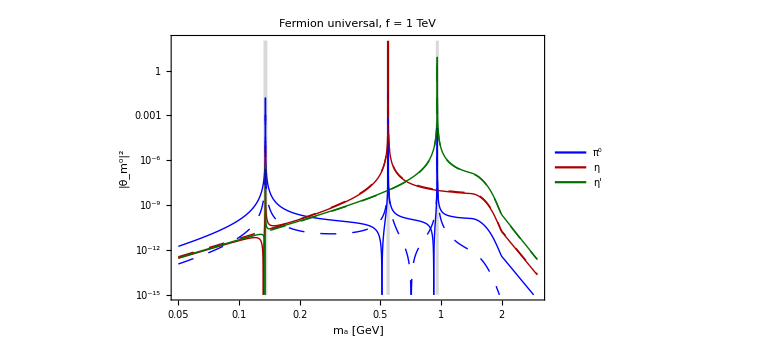

```mathematica
(*This code replaces all fixed symbolic parameters such as the meson mass with their numeric values*)
ruleSymbolsToNumbers[expr_,θηηpr_,ALPtransformation_]:=Block[{},
expr0=(expr)/.Evaluate[rulem0aTransformationSymbolicToExplicit[ALPtransformation]];
expr1=expr0/.{ϵ->fπ/fa}/.{ctheta->Cos[θηηpr],stheta->Sin[θηηpr]}/.Join[{fπ->Fπ},Table[msymbolic[particle]->MASS[particle],{particle,keysMASS}],Table[Γsymbolic[particle]->DECAYWIDTH[particle],{particle,keysDecayWidth}],Table[gSymbol[keys]->gNumber[keys],{keys,Keys[DownValues[gSymbol]][[All,1,1]]}]]/.{gT->13.1}/.{αEM->1/137.,αs->αsData[ma]};
(expr1/.{δ->0})+δval*(D[expr1,δ]/.{δ->0})+δval^2/2(D[expr1,δ,δ]/.{δ->0})
]
Do[
θm0a[model,Λ_,meson,ma_,fa_]=Ffunction[ma]^2*ruleSymbolsToNumbers[D[m0aTransformation[meson,x,"Generic"],alp[x]],θηStandard,"Generic"]/.Evaluate[tableValuesReplacement[model,Λ]];
,{meson,listMesonP0},{model,ModelListAll}]
plotmixingangles[model_]:=LogLogPlot[Evaluate[Join[{Abs[θm0a[model,10^3.,"π^0",ma,10^3]]^2,Abs[θm0a[model,10^3.,"η",ma,10^3]]^2,Abs[θm0a[model,10^3.,"η'",ma,10^3]]^2,Abs[θm0a[model,MASS["t"],"π^0",ma,10^3]]^2,Abs[θm0a[model,MASS["t"],"η",ma,10^3]]^2,Abs[θm0a[model,MASS["t"],"η'",ma,10^3]]^2},{10^30 UnitStep[(MASS["π^0"]+0.003)-ma]*UnitStep[ma-(MASS["π^0"]-0.003)],10^30 UnitStep[(MASS["η"]+0.01)-ma]*UnitStep[ma-(MASS["η"]-0.01)],10^10 UnitStep[(MASS["η'"]+0.016)-ma]*UnitStep[ma-(MASS["η'"]-0.016)]}]],{ma,0.05,3},PlotPoints->500,PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue,Dashing[0.02]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Black},{Thick,Darker@Green},{Thick,Darker@Green,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,22]&/@Join[{"π^0","η","η'"}],{0.1,0.8}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "|θ_(m^0)|^2"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.05,3},{10^-15,100}},PlotLabel->Style[Row[{model, ", f = 1 TeV"}],22,Black],Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}}]
modeltest="Fermion universal";
plotmixingangles[modeltest]
Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Mixing-angles-``.pdf",Sequence@@{modeltest}]}],plotmixingangles[modeltest]];
```

# ALP decay widths

## Kinematics of n-body decays

## 2-body decays

```mathematica
ScalarProduct2body[1,2]=(m^2-m1^2-m2^2)/2;
ScalarProduct2body[1,1]=m1^2;
ScalarProduct2body[2,2]=m2^2;
```

## 3-body decays

### In terms of energies E_1,E_3

```mathematica
(*Kinematics of 3-body decays*)
pPar[En_,mn_]=√(En^2-mn^2);
E2valEnergies[m_,E1_,E3_]=m-E1-E3;
(*Rotation matrices with around z axis (ϕ angle) and x axis (θ angle)*)
ϕRotMatrix[ϕ_]={{Cos[ϕ],Sin[ϕ],0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
θRotMatrix[θ_]={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
(*cos between particles 1,2 and 1,3 at rest frame of decaying particle 0 -> 1+2+3 parametrized in terms of Subscript[E, 1],Subscript[E, 3]*)

cosθ12[E1_,E3_,m_,m1_,m2_,m3_]=(pPar[E3,m3]^2-pPar[E1,m1]^2-pPar[E2valEnergies[m,E1,E3],m2]^2)/(2pPar[E1,m1]*pPar[E2valEnergies[m,E1,E3],m2]);
cosθ13[E1_,E3_,m_,m1_,m2_,m3_]=(pPar[E2valEnergies[m,E1,E3],m2]^2-pPar[E1,m1]^2-pPar[E3,m3]^2)/(2pPar[E1,m1]*pPar[E3,m3]);
θ12[E1_,E3_,m_,m1_,m2_,m3_]=ArcCos[cosθ12[E1,E3,m,m1,m2,m3]];
θ13[E1_,E3_,m_,m1_,m2_,m3_]=ArcCos[cosθ13[E1,E3,m,m1,m2,m3]];
(*Values of θ12,θ13 - compiled (for faster code)*)
θ12comp=Compile[{E1,E3,m,m1,m2,m3},(*ArcCos[cosθ12[E1,E3,m,m1,m2,m3]]*)θ12[E1,E3,m,m1,m2,m3]];
θ13comp=Compile[{E1,E3,m,m1,m2,m3},(*ArcCos[cosθ13[E1,E3,m,m1,m2,m3]]*)θ13[E1,E3,m,m1,m2,m3]];
(*Domain of definition of Subscript[E, 1] and Subscript[E, 3] in decay 0->1+2+3 at rest frame of 0*)
Print["Range of E_3 in terms of E_1:"]
E3domain[E1_,m_,m1_,m2_,m3_]=E3/.Simplify[Solve[cosθ12[E1,E3,m,m1,m2,m3]==1,E3]]
Print["Range of E_1:"]
E1domain[m_,m1_,m2_,m3_]={E1/.Solve[E3domain[E1,m,m1,m2,m3][[1]]-E3domain[E1,m,m1,m2,m3][[2]]==0,E1][[2]],E1/.Solve[E3domain[E1,m,m1,m2,m3][[1]]-E3domain[E1,m,m1,m2,m3][[2]]==0,E1][[3]]}//Simplify
Print["Mandelstam invariants m_13 and m_12 in terms of the energies E_1,E_3:"]
M13[E1_,E3_]=(E1+E3)^2-(pPar[E1,m1]^2+pPar[E3,m3]^2+2*pPar[E1,m1]*pPar[E3,m3]*cosθ13[E1,E3,m,m1,m2,m3])//Expand//Simplify
M12[E1_,E3_]=(E1+E2valEnergies[m,E1,E3])^2-(pPar[E1,m1]^2+pPar[E2valEnergies[m,E1,E3],m2]^2+2*pPar[E1,m1]*pPar[E2valEnergies[m,E1,E3],m2]*cosθ12[E1,E3,m,m1,m2,m3])//Expand//Simplify
M23[E1_]=(m^2+m1^2-2*m*E1);
Q2[E1_,E3_,m_,m2_]=(m^2+m2^2-2*m*E2valEnergies[m,E1,E3]);
Print["Check that m_12+m_23+m_12 reduces to m^2+m_1^2+(m^2)_2+(m^2)_3:"]
M13[E1,E3]+M12[E1,E3]+M23[E1]
```

Range of E_3 in terms of E_1:

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{(√((E1^2-m1^2) (4 E1^2 m^2-4 E1 m (m^2+m1^2-m2^2-m3^2)+m^4+2 m^2 (m1^2-m2^2-m3^2)+m1^4-2 m1^2 m2^2-2 m1^2 m3^2+m2^4-2 m2^2 m3^2+m3^4))-2 E1^2 m+3 E1 m^2+E1 m1^2-E1 m2^2+E1 m3^2-m^3-m m1^2+m m2^2-m m3^2)/(4 E1 m-2 (m^2+m1^2)),-(√((E1^2-m1^2) (4 E1^2 m^2-4 E1 m (m^2+m1^2-m2^2-m3^2)+m^4+2 m^2 (m1^2-m2^2-m3^2)+m1^4-2 m1^2 m2^2-2 m1^2 m3^2+m2^4-2 m2^2 m3^2+m3^4))+2 E1^2 m-3 E1 m^2-E1 m1^2+E1 m2^2-E1 m3^2+m^3+m m1^2-m m2^2+m m3^2)/(4 E1 m-2 (m^2+m1^2))}

Range of E_1:

{m1,(m^2+m1^2-(m2+m3)^2)/(2 m)}

Mandelstam invariants m_13 and m_12 in terms of the energies E_1,E_3:

2 E1 m+2 E3 m-m^2+m2^2

-2 E3 m+m^2+m3^2

Check that m_12+m_23+m_12 reduces to m^2+m_1^2+(m^2)_2+(m^2)_3:

m^2+m1^2+m2^2+m3^2

#### Scalar products

```mathematica
ProductKK2energy=m*E2valEnergies[m,E1,E3];
ProductKK1energy=m*E1;
ProductKK3energy=m*E3;
ProductK1K3energy=(M13[E1,E3]-m1^2-m3^2)/2;
ProductK1K2energy=(M12[E1,E3]-m1^2-m2^2)/2;
ProductK2K3energy=(m^2+m1^2-2*m*E1-m2^2-m3^2)/2;
```

### In terms of Mandelstam invariants m_12, m_23

```mathematica
(*Energies in terms of Mandelstam invariants*)
E2valMandelstam[m12_,m1_,m2_]=(m12-m1^2+m2^2)/(2*Sqrt[m12]);
E3valMandelstam[m12_,MIn_,m3_]=(MIn^2-m12-m3^2)/(2*Sqrt[m12]);
(*Lower and upper limits on Subscript[m, 23] and Subscript[m, 12]*)
m23lower[m12_,MIn_,m1_,m2_,m3_]=FullSimplify[(E2valMandelstam[m12,m1,m2]+E3valMandelstam[m12,MIn,m3])^2 - (Sqrt[E2valMandelstam[m12,m1,m2]^2-m2^2]+Sqrt[E3valMandelstam[m12,MIn,m3]^2-m3^2])^2];
m23upper[m12_,MIn_,m1_,m2_,m3_]=FullSimplify[(E2valMandelstam[m12,m1,m2]+E3valMandelstam[m12,MIn,m3])^2 - (Sqrt[E2valMandelstam[m12,m1,m2]^2-m2^2]-Sqrt[E3valMandelstam[m12,MIn,m3]^2-m3^2])^2];
m12lower[m1_,m2_]=(m1+m2)^2;
m12upper[MIn_,m3_]=(MIn-m3)^2;
```

#### Scalar products

```mathematica
ProductKK=m^2;
ProductK2K2=m2^2;
ProductK3K3=m3^2;
ProductK1K1=m1^2;
ProductKK1mandelstam=(m^2+m1^2-m23)/2;
ProductKK3mandelstam=(m^2+m3^2-m12)/2;
ProductKK2mandelstam=(m^2-ProductKK1mandelstam-ProductKK3mandelstam)//Simplify;
ProductK1K2mandelstam=(m12-m1^2-m2^2)/2;
ProductK2K3mandelstam=(m23-m2^2-m3^2)/2;
ProductK1K3mandelstam=(m^2-2ProductKK2mandelstam+m2^2-m1^2-m3^2)/2//Simplify;
ScalarProduct3body[1,2]=ProductK1K2mandelstam;
ScalarProduct3body[2,3]=ProductK2K3mandelstam;
ScalarProduct3body[1,3]=ProductK1K3mandelstam;
ScalarProduct3body[1,1]=m1^2;
ScalarProduct3body[2,2]=m2^2;
ScalarProduct3body[3,3]=m3^2;
ProductKK-ProductK1K1-ProductK2K2-ProductK3K3-2*(ProductK1K2mandelstam+ProductK2K3mandelstam+ProductK1K3mandelstam)//Simplify
```

0

## Kinematics of 4-body decays (following https://arxiv.org/pdf/1111.5949.pdf)

### Kinematic variables

```mathematica
Callenλ[x_,y_,z_]=x^2+y^2+z^2-2*(x*y+x*z+y*z);
(*Momenta of the particles 1,2 at the rest frame of the system 1-2*)
p1star[s12_,m1_,m2_]=(√Callenλ[s12,m1^2,m2^2])/(2 √s12)//Simplify;
(*Energies of particles 1 and 2 at the rest frame of the system 1-2*)
E1star4b=Assuming[s12>m2^2>0&&m1>0&&m2>0,Simplify[√(p1star[s12,m1,m2]^2+m1^2)]];
E2star4b=Assuming[s12>m1^2>0&&m1>0&&m2>0,Simplify[√(p1star[s12,m1,m2]^2+m2^2)]];
(*Momenta of the particles 3,4 at the rest frame of the system 3-4*)
p3pr[s34_,m3_,m4_]=(√Callenλ[s34,m3^2,m4^2])/(2 √s34)//Simplify;
(*Energies of the particles 3,4 at the rest frame of the system 3-4*)
E3pr4b=Assuming[m3>0&&m4>0&&s34>m4^2,Simplify[√(p3pr[s34,m3,m4]^2+m3^2)]];
E4pr4b=Assuming[m3>0&&m4>0&&s34>m3^2,Simplify[√(p3pr[s34,m3,m4]^2+m4^2)]];
(*Momentum modulus of the 12 and 34 systems at the rest frame of the decaying particle. The "masses" squared of the systems are Subscript[s, 12] and Subscript[s, 34]*)
qv[m_,s12_,s34_]=(√Callenλ[m^2,s12,s34])/(2m)//Simplify;
(*Energies of the system 1-2 and 3-4*)
Eq124b=Assuming[m>0&&s34>0&&m^2>s34&&s12>0,Simplify[√(qv[m,s12,s34]^2+s12)]];
Eq344b=Assuming[m>0&&s34>0&&m^2>s34&&s12>0&&m^2>s12,Simplify[√(qv[m,s12,s34]^2+s34)]];
(*γ factors of the systems 12 and 34*)
γ12[m_,s12_,s34_]=Assuming[m>0&&s12>0&&s34<m^2,Simplify[1/(√(1-qv[m,s12,s34]^2/Eq124b^2))]];
γ34[m_,s12_,s34_]=Assuming[m>0&&s34>0&&s12<m^2,Simplify[1/(√(1-qv[m,s12,s34]^2/Eq344b^2))]];
```

### 4-vectors at the rest frame of the decaying particle in terms of kinematics defined above (Eq. A.5 from the reference)

-Graphics-

```mathematica
β12vec=FV[q,μ]/qv[m,s12,s34];
p1star["||"]=p1star[s12,m1,m2]*FV[q,μ]/qv[m,s12,s34]*Cos[θ1];
p1star["⊥"]=FV[p1s,μ]-p1star["||"];
p2star["||"]=-p1star["||"];
p2star["⊥"]=-p1star["⊥"];
p3pr["||"]=p3pr[s34,m3,m4]/qv[m,s12,s34]*FV[k,μ]*Cos[θ3]/.{k->-q};
p3pr["⊥"]=FV[p3p,μ]-p3pr["||"];
p4pr["||"]=-p3pr["||"];
p4pr["⊥"]=-p3pr["⊥"];
P14vector[μ_]={γ12[m,s12,s34](E1star4b+qv[m,s12,s34]/Eq124b*p1star[s12,m1,m2]*Cos[θ1]),γ12[m,s12,s34](E1star4b*FV[q,μ]/Eq124b+p1star["||"])+p1star["⊥"]}//Simplify;
P24vector[μ_]={γ12[m,s12,s34](E2star4b-(p1star[s12,m1,m2]*qv[m,s12,s34])/Eq124b*Cos[θ1]),γ12[m,s12,s34](E2star4b*FV[q,μ]/Eq124b+p2star["||"])+p2star["⊥"]}//Simplify;
P34vector[μ_]={γ34[m,s12,s34](E3pr4b+(p3pr[s34,m3,m4]*qv[m,s12,s34])/Eq344b*Cos[θ3]),γ34[m,s12,s34](E3pr4b*FV[k,μ]/Eq344b+p3pr["||"])+p3pr["⊥"]}/.{k->-q}//Simplify;
P44vector[μ_]={γ34[m,s12,s34](E4pr4b-(p3pr[s34,m3,m4]*qv[m,s12,s34])/Eq344b*Cos[θ3]),γ34[m,s12,s34](E4pr4b*FV[k,μ]/Eq344b+p4pr["||"])+p4pr["⊥"]}/.{k->-q}//Simplify;
```

### Scalar products

```mathematica
rule:={ScalarProduct[q,q]-> qv[m,s12,s34]^2,ScalarProduct[p1s,p1s]->p1star[s12,m1,m2]^2,ScalarProduct[p3p,p3p]-> p3pr[s34,m3,m4]^2,ScalarProduct[p1s,q]->p1star[s12,m1,m2]*qv[m,s12,s34]*Cos[θ1],ScalarProduct[p1s,p3p]->p1star[s12,m1,m2]*p3pr[s34,m3,m4]*(-Cos[θ1]*Cos[θ3]-Sin[θ1]*Sin[θ3]*Cos[ϕ3]),ScalarProduct[p3p,q]->-p3pr[s34,m3,m4]*qv[m,s12,s34]*Cos[θ3]}
ProductP1P24body=Assuming[m>0&&s12>0&&m^2>s34&&s12>m1^2&&s12>m2^2,Simplify[(P14vector[μ][[1]]*P24vector[μ][[1]]-P14vector[μ][[2]]*P24vector[μ][[2]]//Contract)/.Evaluate[rule]]];
ProductP3P44body=(Assuming[m>0&&s12>0&&m^2>s34&&s34>m3^2&&s34>m4^2,Simplify[(P34vector[μ][[1]]*P44vector[μ][[1]]-P34vector[μ][[2]]*P44vector[μ][[2]]//Contract)/.Evaluate[rule]]]);
ProductP1P34body=Assuming[m>0&&s34>0&&s12>0&&m^2>s12&&m^2>s34&&s12>m1^2&&s12>m2^2&&s34>m3^2&&s34>m4^2(*&&s34>m3^2&&s34>m4^2&&s12>m1^2&&s12>m2^2*),Simplify[(P14vector[μ][[1]]*P34vector[μ][[1]]-P14vector[μ][[2]]*P34vector[μ][[2]]//Contract)/.Evaluate[rule]]];
ProductP2P44body=Assuming[m>0&&s34>0&&s12>0&&m^2>s12&&m^2>s34&&s12>m1^2&&s12>m2^2&&s34>m3^2&&s34>m4^2(*&&s34>m3^2&&s34>m4^2&&s12>m1^2&&s12>m2^2*),Simplify[(P24vector[μ][[1]]*P44vector[μ][[1]]-P24vector[μ][[2]]*P44vector[μ][[2]]//Contract)/.Evaluate[rule]]];
ProductP2P34body=Assuming[m>0&&s34>0&&s12>0&&m^2>s12&&m^2>s34&&s12>m1^2&&s12>m2^2&&s34>m3^2&&s34>m4^2(*&&s34>m3^2&&s34>m4^2&&s12>m1^2&&s12>m2^2*),Simplify[(P24vector[μ][[1]]*P34vector[μ][[1]]-P24vector[μ][[2]]*P34vector[μ][[2]]//Contract)/.Evaluate[rule]]];
ProductP1P44body=Assuming[m>0&&s34>0&&s12>0&&m^2>s12&&m^2>s34&&s12>m1^2&&s12>m2^2&&s34>m3^2&&s34>m4^2(*&&s34>m3^2&&s34>m4^2&&s12>m1^2&&s12>m2^2*),Simplify[(P14vector[μ][[1]]*P44vector[μ][[1]]-P14vector[μ][[2]]*P44vector[μ][[2]]//Contract)/.Evaluate[rule]]];
```

#### Test: check that (p_1+p_2+p_3+p_4)^2 = m^2

```mathematica
exprtest4body=Assuming[s12>0&&s34>0,Simplify[(m1^2+m2^2+m3^2+m4^2+2*(ProductP1P24body+ProductP1P34body+ProductP1P44body+ProductP2P34body+ProductP2P44body+ProductP3P44body))]]
```

m^2

## Total ALP-meson Lagrangian used to compute the widths

## Definitions

```mathematica
TotalLagrangianBeforeDiagonalization["Generic"]=(ChPTkineticTerm["Generic"]+ChPTbreakingTerm["Generic"]+VMDterm["Generic"]+LagrangianS+LagrangianT)//Expand;
expr2=TotalLagrangianBeforeDiagonalization["Generic"]/.rulem0aTransformationSymbolic;//AbsoluteTiming
FieldsListPattern=Join[Table[{PfieldSymbol[field,x],dPfieldSymbol[field,x,a_]},{field,listMesonP}]//Flatten,Table[{SfieldSymbol[field,x],dSfieldSymbol[field,x,a_]},{field,listMesonS}]//Flatten,Table[{VfieldSymbol[field,x,a_],dVfieldSymbol[field,x,a_,b_]},{field,listMesonV}]//Flatten,Table[{TfieldSymbol[field,x,a_,b_],dTfieldSymbol[field,x,a_,b_,c_]},{field,listMesonT}]//Flatten];
FieldsList=Join[Table[{PfieldSymbol[field,x],dPfieldSymbol[field,x,a]},{field,listMesonP}]//Flatten,Table[{SfieldSymbol[field,x],dSfieldSymbol[field,x,a]},{field,listMesonS}]//Flatten,Table[{VfieldSymbol[field,x,a],dVfieldSymbol[field,x,a,b]},{field,listMesonV}]//Flatten,Table[{TfieldSymbol[field,x,a,b],dTfieldSymbol[field,x,a,b,c]},{field,listMesonT}]//Flatten];
(*Scale coefficients counting the number of times the given field or its derivative enters the given term*)
CoefficientsListIndividual=t^Join[Table[{y[field],y[field]},{field,listMesonP}]//Flatten,Table[{y[field],y[field]},{field,listMesonS}]//Flatten,Table[{y[field],y[field]},{field,listMesonV}]//Flatten,Table[{y[field],y[field]},{field,listMesonT}]//Flatten];
(*Scale coefficients that count how many fields or their derivatives the given term contains in total*)
CoefficientsListCommon=t^Join[Table[{y[field],y[field]},{field,listMesonP}]//Flatten,Table[{y[field],y[field]},{field,listMesonS}]//Flatten,Table[{y[field],y[field]},{field,listMesonV}]//Flatten,Table[{y[field],y[field]},{field,listMesonT}]//Flatten];
CoefficientsListALP={ta^y,ta^y};
(*Replacement rule field->scaling*)
repsIndividual=Thread[FieldsListPattern->CoefficientsListIndividual*FieldsList];
repsCommon=Thread[FieldsListPattern->CoefficientsListCommon*FieldsList];
repsALP=Thread[{alp[x],dalp[x,a_]}->CoefficientsListALP*{alp[x],dalp[x,a]}];
```

{0.375005,Null}

## Lagrangian calculation

```mathematica
genlagropt=dropdownDialog[{"Generate","Import"},"Generate the total ALP-meson interaction Lagrangian from scratch, or just import it (if it has been generated previously)?"];
If[genlagropt=="Generate",
expr3=(expr2/.{alp[x]->0,dalp[x,a_]:>0})+alp[x]*(D[expr2,alp[x]]/.{alp[x]->0,dalp[x,a_]:>0})+Sum[dalp[x,i]*(D[expr2,dalp[x,i]]/.{alp[x]->0,dalp[x,a_]:>0}),{i,indiceslist}];
expr4=(expr3/.{ϵ->0})+ϵ*(D[expr3,ϵ]/.{ϵ->0});
expr5=((expr4/.{δ->0})+δ*(D[expr4,δ]/.{δ->0})/.{md^2+2*ms*md->2*ms*md}/.{md+2ms->2ms});
(*Extracting the quadratic part of the Lagrangian (only pseudoscalar particles)*)
ruleScaling=Table[PfieldSymbol[field,x]->Exp[y]PfieldSymbol[field,x],{field,listMesonP}];
ruleScaling=Join[ruleScaling,Table[With[{field=field,fieldSymb=fieldSymbol[field],fieldDSymb=dfieldSymbol[field]},fieldDSymb[x,a_]:>Exp[y]fieldDSymb[x,a]],{field,listMesonP}]];
ruleScaling=Join[ruleScaling,Table[SfieldSymbol[field,x]->Exp[y]SfieldSymbol[field,x],{field,listMesonS}]];
ruleScaling=Join[ruleScaling,Table[With[{field=field,fieldSymb=fieldSymbol[field],fieldDSymb=dfieldSymbol[field]},fieldDSymb[x,a_]:>Exp[y]fieldDSymb[x,a]],{field,listMesonS}]];
ruleScaling=Join[ruleScaling,Table[With[{field=field,fieldSymb=fieldSymbol[field],fieldDSymb=dfieldSymbol[field]},{fieldSymb[x,a_]:>Exp[y]fieldSymb[x,a],fieldDSymb[x,a_,b_]:>Exp[y]fieldDSymb[x,a,b]}],{field,listMesonV}]//Flatten];
ruleScaling=Join[ruleScaling,Table[With[{field=field,fieldSymb=fieldSymbol[field],fieldDSymb=dfieldSymbol[field]},{fieldSymb[x,a_,b_]:>Exp[y]fieldSymb[x,a,b],fieldDSymb[x,a_,b_,c_]:>Exp[y]fieldDSymb[x,a,b,c]}],{field,listMesonT}]//Flatten];
expr6=(expr5/.ruleScaling//Expand)/.{Exp[2*y]->0}/.{y->0};
expr6quadraticCorrectP=-1/2 Sum[msymbolic[field]^2 PfieldSymbol[field,x]Conjugate[PfieldSymbol[field,x]],{field,listMesonP}]+1/2 Sum[dPfieldSymbol[field,x,μ]Conjugate[dPfieldSymbol[field,x,μ]],{field,listMesonP}];
expr6quadraticCorrectS=-1/2 Sum[msymbolic[field]^2 SfieldSymbol[field,x]Conjugate[SfieldSymbol[field,x]],{field,listMesonS}]+1/2 Sum[dSfieldSymbol[field,x,μ]Conjugate[dSfieldSymbol[field,x,μ]],{field,listMesonS}];
(*Commented: checking that after inserting numeric values of the diagonalization coefficients the non-diagonal quadratic terms still vanish*)
(*(Normal@Series[expr5quadratic/.Evaluate[rulem0aTransformationSymbolicToExplicit]//Simplify,{md,0,0}]//Expand)/.{δ*ϵ->0,δ^2->0}//Simplify;*)
(*Total Lagrangian*)
TotalLagrangian=(expr6+expr6quadraticCorrectP+expr6quadraticCorrectS)//Expand;
TotalLagrangianALPonly=(TotalLagrangian-(TotalLagrangian/.{ϵ->0}))//Expand;
TotalLagrangianScaled=Expand[TotalLagrangian]/. repsIndividual;
Export[FileNameJoin[{NotebookDirectory[],"Temporary data/Lagr.m"}],TotalLagrangianScaled,"MX"],
TotalLagrangianScaled=Import[FileNameJoin[{NotebookDirectory[],"Temporary data/Lagr.m"}],"MX"];
]
LagrangianGivenFields[fieldlist_,powerlist_]:=Block[{},
terms=Total[Cases[TotalLagrangianScaled,t^(Sum[y[fieldlist[[i]]]*powerlist[[i]],{i,1,Length[fieldlist]}])*aa_:>aa]]
]
LagrangianGivenFields1[expr_,fieldlist_,powerlist_]:=Block[{},
terms=Total[Cases[(expr/. repsIndividual),t^(Sum[y[fieldlist[[i]]]*powerlist[[i]],{i,1,Length[fieldlist]}])*aa_:>aa]]
]
Print["Number of terms in the Lagrangian (may be reduced by a factor of few since the symmetry over indices permutations is not included at this step):"]
TotalLagrangianScaled//Length
Print["Example: the Lagrangian including exactly 1 ALP, 1 π^+, 1 π^-, and 1 π^0:"]
expr=LagrangianGivenFields[{"a","π^+","π^-","π^0"},{1,1,1,1}]//Simplify
```

Number of terms in the Lagrangian (may be reduced by a factor of few since the symmetry over indices permutations is not included at this step):

66952

Example: the Lagrangian including exactly 1 ALP, 1 π^+, 1 π^-, and 1 π^0:

1/(18 fπ^2)ϵ (alp(x) (3 π0ALP dπminus(x,μ) (3 cvmd ma-mηpr-2) (2 π0(x) dπplus(x,μ)-πplus(x) dπ0(x,μ))-πminus(x) (3 π0ALP dπ0(x,μ) dπplus(x,μ) (3 cvmd ma-mηpr-2)+2 mπ0^2 π0(x) πplus(x) (ctheta δ (3 √3 cG (ηπ0+√2 ηprπ0)+ηALP (√3-3 stheta (2 √2 ηπ0+ηprπ0))+ηprALP (-3 ηπ0 stheta+6 √2 ηprπ0 stheta+√6))+√3 δ stheta (3 cG (ηprπ0-√2 ηπ0)-√2 ηALP+ηprALP)+3 ctheta^2 δ (-ηALP ηπ0+2 √2 ηALP ηprπ0+2 √2 ηπ0 ηprALP+ηprALP ηprπ0)-3 (δ (-2 ηALP ηπ0+√2 ηALP ηprπ0+√2 ηπ0 ηprALP-ηprALP ηprπ0)+π0ALP))))-3 dalp(x,μ) (πplus(x) (π0(x) dπminus(x,μ)-2 πminus(x) dπ0(x,μ))+π0(x) πminus(x) dπplus(x,μ)) (4 cd-2 (2 cG δ+2 cu+π0ALP)+3 cvmd π0ALP ma-mηpr))

### Exporting to FeynRules output

```mathematica
(*ruleToFeynRules1=Table[With[{field=field,fieldSymb=fieldSymbol[field],fieldDSymb=dfieldSymbol[field]},{fieldDSymb[x,c_]:>ddd[fieldSymb,c]}],{field,Join[listMesonP,listMesonS]}]//Flatten;
ruleToFeynRules2=Table[With[{field=field,fieldSymb=fieldSymbol[field],fieldDSymb=dfieldSymbol[field]},{fieldSymb[x]:>fieldSymb}],{field,Join[listMesonP,listMesonS]}]//Flatten;
imp1=TotalLagrangian/.Evaluate[ruleOnlyFields[Join[listMesonP,listMesonS]]];
imp2=imp1/.ruleToFeynRules1;
imp3=imp2/.ruleToFeynRules2;
imp4=imp3/.{ma->mALP,α->α1,β->α2,μ->α3,ν->α4,EPSILON[μ_,ν_,α_,β_]:>ee}/.{ϵ->ϵ,ee->eps[μ,ν,α,β]}/.{0[a_,b_,c_,d_]:>eps[a,b,c,d]};
Export[FileNameJoin[{NotebookDirectory[],"Lagrangian.m"}],imp4,"MX"]*)
```

## Feynman rules

## Functional derivatives

```mathematica
(*Old*)
(*________________________________________________________________*)
<<FeynCalc`
indexlist1={μ,ν,α,β};
FuncDerFieldOldTemp[expression_,meson_,in_,fieldindexlist_,"V"]:=Block[{},
indexlist=(*DeleteDuplicates[Flatten[Rest@*List@@@Variables[expression]]]*){μ,ν,α,β};
Sum[(D[expression,VfieldSymbol[meson,x,indexlist[[i]]]]+Sum[(I*in*p[meson,indexlist[[j]]]*D[expression,dVfieldSymbol[meson,x,indexlist[[j]],indexlist[[i]]]]),{j,1,Length[indexlist],1}])/.{indexlist[[i]]->fieldindexlist[[1]]},{i,1,Length[indexlist],1}]
]
FuncDerFieldOldTemp[expression_,meson_,in_,fieldindexlist_,"P"]:=Block[{},
indexlist={μ,ν,α,β};(D[expression,PfieldSymbol[meson,x]])+Sum[I*in*p[meson,indexlist[[i]]](D[expression,dPfieldSymbol[meson,x,indexlist[[i]]]]),{i,1,Length[indexlist],1}]
]
FuncDerFieldOldTemp[expression_,meson_,in_,fieldindexlist_,"S"]:=Block[{},
indexlist={μ,ν,α,β};(D[expression,SfieldSymbol[meson,x]])+Sum[I*in*p[meson,indexlist[[i]]](D[expression,dSfieldSymbol[meson,x,indexlist[[i]]]]),{i,1,Length[indexlist],1}]
]
FuncDerFieldOldTemp[expression_,meson_,in_,fieldindexlist_,"T"]:=Block[{},
indexlist={μ,ν,α,β};Sum[(D[expression,TfieldSymbol[meson,x,indexlist[[i]],indexlist[[k]]]]+Sum[(I*in*p[meson,indexlist[[j]]]*D[expression,dTfieldSymbol[meson,x,indexlist[[j]],indexlist[[i]],indexlist[[k]]]]),{j,1,Length[indexlist],1}])/.{indexlist[[i]]->fieldindexlist[[1]],indexlist[[k]]->fieldindexlist[[2]]},{k,1,Length[indexlist],1},{i,1,Length[indexlist],1}]
]
FuncDerFieldOld[expression_,meson_,in_,fieldindexlist_]:=FuncDerFieldOldTemp[expression,meson,in,fieldindexlist,SpinParity[meson]];
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

#### Definitions

```mathematica
π0/:D[π0[x_],π0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],π0],1,0]
dπ0/:D[dπ0[x_,a_],π0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dπ0],I*p["π^0",a] ,0]
πplus/:D[πplus[x_],πplus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],πplus],1,0]
dπplus/:D[dπplus[x_,a_],πplus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dπplus],I*p["π^+",a] ,0]
πminus/:D[πminus[x_],πminus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],πminus],1,0]
dπminus/:D[dπminus[x_,a_],πminus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dπminus],I*p["π^-",a] ,0]
η/:D[η[x_],η[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],η],1,0]
dη/:D[dη[x_,a_],η[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dη],I*p["η",a] ,0]
ηpr/:D[ηpr[x_],ηpr[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],ηpr],1,0]
dηpr/:D[dηpr[x_,a_],ηpr[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dηpr],I*p["η'",a] ,0]
Kplus/:D[Kplus[x_],Kplus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],Kplus],1,0]
dKplus/:D[dKplus[x_,a_],Kplus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dKplus],I*p["K^+",a] ,0]
Kminus/:D[Kminus[x_],Kminus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],Kminus],1,0]
dKminus/:D[dKminus[x_,a_],Kminus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dKminus],I*p["K^-",a] ,0]
K0/:D[K0[x_],K0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],K0],1,0]
dK0/:D[dK0[x_,a_],K0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dK0],I*p["K^0",a] ,0]
K0bar/:D[K0bar[x_],K0bar[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],K0bar],1,0]
dK0bar/:D[dK0bar[x_,a_],K0bar[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dK0bar],I*p["(K̄)^0",a] ,0]
alp/:D[alp[x_],alp[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],alp],1,0]
dalp/:D[dalp[x_,a_],alp[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dalp],I*p["a",a] ,0]
(*Scalar mesons*)
σ/:D[σ[x_],σ[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],σ],1,0]
dσ/:D[dσ[x_,a_],σ[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dσ],I*p["σ",a] ,0]
f0/:D[f0[x_],f0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],f0],1,0]
df0/:D[df0[x_,a_],f0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],df0],I*p["f^0",a] ,0]
κplus/:D[κplus[x_],κplus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],κplus],1,0]
dκplus/:D[dκplus[x_,a_],κplus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dκplus],I*p["κ^+",a] ,0]
κminus/:D[κminus[x_],κminus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],κminus],1,0]
dκminus/:D[dκminus[x_,a_],κminus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dκminus],I*p["κ^-",a] ,0]
κ0/:D[κ0[x_],κ0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],κ0],1,0]
dκ0/:D[dκ0[x_,a_],κ0[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dκ0],I*p["κ^0",a] ,0]
κ0bar/:D[κ0bar[x_],κ0bar[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],κ0bar],1,0]
dκ0bar/:D[dκ0bar[x_,a_],κ0bar[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dκ0bar],I*p["(κ̄)^0",a] ,0]
a00/:D[a00[x_],a00[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],a00],1,0]
da00/:D[da00[x_,a_],a00[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],da00],I*p["(a^0)_0",a] ,0]
a0plus/:D[a0plus[x_],a0plus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],a0plus],1,0]
da0plus/:D[da0plus[x_,a_],a0plus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],da0plus],I*p["(a^+)_0",a] ,0]
a0minus/:D[a0minus[x_],a0minus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],a0minus],1,0]
da0minus/:D[da0minus[x_,a_],a0minus[x_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],da0minus],I*p["(a^-)_0",a] ,0]
(*Vector mesons*)
ρ0/:D[ρ0[x_,a_],ρ0[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],ρ0],kd[a,b],0]
dρ0/:D[dρ0[x_,a_,b_],ρ0[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dρ0],I*p["ρ^0",a] kd[b,c],0]
ρplus/:D[ρplus[x_,a_],ρplus[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],ρplus],kd[a,b],0]
dρplus/:D[dρplus[x_,a_,b_],ρplus[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dρplus],I*p["ρ^+",a] kd[b,c],0]
ρminus/:D[ρminus[x_,a_],ρminus[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],ρminus],kd[a,b],0]
dρminus/:D[dρminus[x_,a_,b_],ρminus[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dρminus],I*p["ρ^-",a] kd[b,c],0]
ω/:D[ω[x_,a_],ω[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],ω],kd[a,b],0]
dω/:D[dω[x_,a_,b_],ω[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dω],I*p["ω",a] kd[b,c],0]
ϕ/:D[ϕ[x_,a_],ϕ[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],ϕ],kd[a,b],0]
dϕ/:D[dϕ[x_,a_,b_],ϕ[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dϕ],I*p["ϕ",a] kd[b,c],0]
Kstarplus/:D[Kstarplus[x_,a_],Kstarplus[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],Kstarplus],kd[a,b],0]
dKstarplus/:D[dKstarplus[x_,a_,b_],Kstarplus[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dKstarplus],I*p["K^(*+)",a] kd[b,c],0]
Kstarminus/:D[Kstarminus[x_,a_],Kstarminus[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],Kstarminus],kd[a,b],0]
dKstarminus/:D[dKstarminus[x_,a_,b_],Kstarminus[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dKstarminus],I*p["K^(*-)",a] kd[b,c],0]
Kstar0/:D[Kstar0[x_,a_],Kstar0[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],Kstar0],kd[a,b],0]
dKstar0/:D[dKstar0[x_,a_,b_],Kstar0[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dKstar0],I*p["K^(*0)",a] kd[b,c],0]
Kstar0bar/:D[Kstar0bar[x_,a_],Kstar0bar[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],Kstar0bar],kd[a,b],0]
dKstar0bar/:D[dKstar0bar[x_,a_,b_],Kstar0bar[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dKstar0bar],I*p["(K̄)^(*0)",a] kd[b,c],0]
A/:D[A[x_,a_],A[x_,b_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],A],kd[a,b],0]
dA/:D[dA[x_,a_,b_],A[x_,c_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],dA],I*p["A",a] kd[b,c],0]
f2/:D[f2[x_,a_,b_],f2[x_,c_,d_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],f2],kd[a,c]*kd[b,d],0]
df2/:D[df2[x_,a_,b_,c_],f2[x_,d_,e_],OptionsPattern[]]:=If[MemberQ[OptionValue[NonConstants],df2],I*p["f2",a] kd[b,d]*kd[c,e],0]
Table[{field,D[PfieldSymbol[field,x],PfieldSymbol[field,x],NonConstants->{PfieldSymbol[field,x][[0]],dPfieldSymbol[field,x,a][[0]]}],D[dPfieldSymbol[field,x,c2],PfieldSymbol[field,x],NonConstants->{PfieldSymbol[field,x][[0]],dPfieldSymbol[field,x,a][[0]]}]},{field,listMesonP}]
Table[{field,D[SfieldSymbol[field,x],SfieldSymbol[field,x],NonConstants->{SfieldSymbol[field,x][[0]],dSfieldSymbol[field,x,a][[0]]}],D[dSfieldSymbol[field,x,c2],SfieldSymbol[field,x],NonConstants->{SfieldSymbol[field,x][[0]],dSfieldSymbol[field,x,a][[0]]}]},{field,listMesonS}]
Table[{field,D[VfieldSymbol[field,x,x2],VfieldSymbol[field,x,κ3],NonConstants->{VfieldSymbol[field,x,a][[0]],dVfieldSymbol[field,x,a,b][[0]]}],D[dVfieldSymbol[field,x,c2,c4],VfieldSymbol[field,x,κ3],NonConstants->{VfieldSymbol[field,x,a][[0]],dVfieldSymbol[field,x,a,b][[0]]}]},{field,listMesonV}]
Table[{field,D[TfieldSymbol[field,x,x2,x8],TfieldSymbol[field,x,κ3,κ8],NonConstants->{TfieldSymbol[field,x,a,b][[0]],dTfieldSymbol[field,x,a,b,c][[0]]}],D[dTfieldSymbol[field,x,c2,c4,c5],TfieldSymbol[field,x,κ3,κ8],NonConstants->{TfieldSymbol[field,x,a,b][[0]],dTfieldSymbol[field,x,a,b,c][[0]]}]},{field,listMesonT}]
```

(π^0 | 1 | ⅈ p(π^0,c2)
π^+ | 1 | ⅈ p(π^+,c2)
π^- | 1 | ⅈ p(π^-,c2)
K^0 | 1 | ⅈ p(K^0,c2)
(K̄)^0 | 1 | ⅈ p((K̄)^0,c2)
K^+ | 1 | ⅈ p(K^+,c2)
K^- | 1 | ⅈ p(K^-,c2)
η | 1 | ⅈ p(η,c2)
η' | 1 | ⅈ p(η',c2)
a | 1 | ⅈ p(a,c2))

(σ | 1 | ⅈ p(σ,c2)
f_0 | 1 | ⅈ p(f^0,c2)
(a^0)_0 | 1 | ⅈ p((a^0)_0,c2)
(a^+)_0 | 1 | ⅈ p((a^+)_0,c2)
(a^-)_0 | 1 | ⅈ p((a^-)_0,c2)
κ^0 | 1 | ⅈ p(κ^0,c2)
(κ̄)^0 | 1 | ⅈ p((κ̄)^0,c2)
κ^+ | 1 | ⅈ p(κ^+,c2)
κ^- | 1 | ⅈ p(κ^-,c2))

(ρ^0 | kd(x2,κ3) | ⅈ p(ρ^0,c2) kd(c4,κ3)
ρ^+ | kd(x2,κ3) | ⅈ p(ρ^+,c2) kd(c4,κ3)
ρ^- | kd(x2,κ3) | ⅈ p(ρ^-,c2) kd(c4,κ3)
K^(*+) | kd(x2,κ3) | ⅈ p(K^(*+),c2) kd(c4,κ3)
K^(*-) | kd(x2,κ3) | ⅈ p(K^(*-),c2) kd(c4,κ3)
K^(*0) | kd(x2,κ3) | ⅈ p(K^(*0),c2) kd(c4,κ3)
(K̄)^(*0) | kd(x2,κ3) | ⅈ p((K̄)^(*0),c2) kd(c4,κ3)
ϕ | kd(x2,κ3) | ⅈ p(ϕ,c2) kd(c4,κ3)
ω | kd(x2,κ3) | ⅈ p(ω,c2) kd(c4,κ3)
A | kd(x2,κ3) | ⅈ p(A,c2) kd(c4,κ3))

((a^0)_2 | D[a20(x,x2,x8),a20(x,κ3,κ8),NonConstants→{a20,da20}] | D[da20(x,c2,c4,c5),a20(x,κ3,κ8),NonConstants→{a20,da20}]
(a^+)_2 | D[a2plus(x,x2,x8),a2plus(x,κ3,κ8),NonConstants→{a2plus,da2plus}] | D[da2plus(x,c2,c4,c5),a2plus(x,κ3,κ8),NonConstants→{a2plus,da2plus}]
(a^-)_2 | D[a2minus(x,x2,x8),a2minus(x,κ3,κ8),NonConstants→{a2minus,da2minus}] | D[da2minus(x,c2,c4,c5),a2minus(x,κ3,κ8),NonConstants→{a2minus,da2minus}]
f_2 | kd(x2,κ3) kd(x8,κ8) | ⅈ p(f2,c2) kd(c4,κ3) kd(c5,κ8)
f'_2 | D[f2pr(x,x2,x8),f2pr(x,κ3,κ8),NonConstants→{df2pr,f2pr}] | D[df2pr(x,c2,c4,c5),f2pr(x,κ3,κ8),NonConstants→{df2pr,f2pr}]
(K^(*+))_2 | D[K2starplus(x,x2,x8),K2starplus(x,κ3,κ8),NonConstants→{dK2starplus,K2starplus}] | D[dK2starplus(x,c2,c4,c5),K2starplus(x,κ3,κ8),NonConstants→{dK2starplus,K2starplus}]
(K^(*-))_2 | D[K2starminus(x,x2,x8),K2starminus(x,κ3,κ8),NonConstants→{dK2starminus,K2starminus}] | D[dK2starminus(x,c2,c4,c5),K2starminus(x,κ3,κ8),NonConstants→{dK2starminus,K2starminus}]
(K^(*0))_2 | D[K2star0(x,x2,x8),K2star0(x,κ3,κ8),NonConstants→{dK2star0,K2star0}] | D[dK2star0(x,c2,c4,c5),K2star0(x,κ3,κ8),NonConstants→{dK2star0,K2star0}]
((K̄)^(*0))_2 | D[K2star0bar(x,x2,x8),K2star0bar(x,κ3,κ8),NonConstants→{dK2star0bar,K2star0bar}] | D[dK2star0bar(x,c2,c4,c5),K2star0bar(x,κ3,κ8),NonConstants→{dK2star0bar,K2star0bar}])

### Final expressions

```mathematica
FuncDerFieldTemp[expression_,meson_,in_,indexlist_,"V"]:=Block[{},
expr10=D[expression,VfieldSymbol[meson,x,indexlist[[1]]],NonConstants->{VfieldSymbol[meson,x,a][[0]],dVfieldSymbol[meson,x,a,b][[0]]}]/.{p[meson,a_]:>in*p[meson,a]}(*;
expr10//.e_*kd[x_,y_]:>(e/. y->x)*)
]
FuncDerFieldTemp[expression_,meson_,in_,indexlist_,"P"]:=Block[{},
expr10=D[expression,PfieldSymbol[meson,x],NonConstants->{PfieldSymbol[meson,x][[0]],dPfieldSymbol[meson,x,a][[0]]}]/.{p[meson,a_]:>in*p[meson,a]}(*;
expr10//.e_*kd[x_,y_]:>(e/. y->x)*)
]
FuncDerFieldTemp[expression_,meson_,in_,indexlist_,"S"]:=Block[{},
expr10=D[expression,SfieldSymbol[meson,x],NonConstants->{SfieldSymbol[meson,x][[0]],dSfieldSymbol[meson,x,a][[0]]}]/.{p[meson,a_]:>in*p[meson,a]}(*;
expr10//.e_*kd[x_,y_]:>(e/. y->x)*)
]
FuncDerFieldTemp[expression_,meson_,in_,indexlist_,"T"]:=Block[{},
expr10=D[expression,TfieldSymbol[meson,x,indexlist[[1]],indexlist[[2]]],NonConstants->{TfieldSymbol[meson,x,a,b][[0]],dTfieldSymbol[meson,x,a,a2,a3][[0]]}]/.{p[meson,a_]:>in*p[meson,a]}(*;
expr10//.e_*kd[x_,y_]:>(e/. y->x)*)
]
FuncDerField[expression_,meson_,in_,indexlist_]:=FuncDerFieldTemp[expression,meson,in,indexlist,SpinParity[meson]];
fdgfd=FuncDerField[TotalLagrangianScaled,"ρ^0",-1,{κ23}];//AbsoluteTiming
fdgfd1=FuncDerFieldOld[TotalLagrangianScaled,"ρ^0",-1,{κ23}];//AbsoluteTiming
exprtest1=fdgfd//.e_*kd[x_,y_]:>(e/. x->y);
exprtest1-fdgfd1//Expand
```

{0.716235,Null}

{0.667372,Null}

0

## Vertices

```mathematica
FeynmanRuleVertex0[partlist_,inlist_,labelslist_]:=Block[{},
OfieldTable=Table[If[inlist[[i]]==1,partlist[[i]],findingConjugated[partlist[[i]]]],{i,1,Length[partlist],1}];
LagrangianRelevant=LagrangianGivenFields[OfieldTable,Table[1,Length[OfieldTable]]];
plist=Table[Symbol["p"<>(labelslist[[i]]//ToString)],{i,1,Length[labelslist],1}];
indiceslist=Table[{Symbol["ξ"<>(labelslist[[i]]//ToString)<>"1"],Symbol["ξ"<>(labelslist[[i]]//ToString)<>"2"]},{i,1,Length[labelslist],1}];
expr1=0;
Do[
If[i==1,functional=LagrangianRelevant,functional=expr1];
expr1=FuncDerField[functional,OfieldTable[[i]],inlist[[i]],indiceslist[[i]]]/.{p[OfieldTable[[i]],a_]:>FV[plist[[i]],a]};
,{i,1,Length[OfieldTable],1}];
expr1=(expr1//.e_*kd[x_,y_]:>(e/. x->y));
temp=(expr1/.{EPSILON[a_,b_,c_,d_]:>LeviCivita[a,b,c,d]}/.Evaluate[ruleFieldsToZero])//Contract//ExpandScalarProduct//Simplify
]
FeynmanRuleVertex[partlist_,inlist_,labelslist_]:=Block[{},
OfieldTable=Table[If[inlist[[i]]==1,partlist[[i]],findingConjugated[partlist[[i]]]],{i,1,Length[partlist],1}];
LagrangianRelevant=LagrangianGivenFields[OfieldTable,Table[1,Length[OfieldTable]]];
plist=Table[Symbol["p"<>(labelslist[[i]]//ToString)],{i,1,Length[labelslist],1}];
indiceslist=Table[{Symbol["ξ"<>(labelslist[[i]]//ToString)<>"1"],Symbol["ξ"<>(labelslist[[i]]//ToString)<>"2"]},{i,1,Length[labelslist],1}];
expr1=0;
Do[
If[i==1,functional=LagrangianRelevant,functional=expr1];expr1=FuncDerField[functional,OfieldTable[[i]],inlist[[i]],indiceslist[[i]]]/.{p[OfieldTable[[i]],a_]:>FV[plist[[i]],a]},{i,1,Length[OfieldTable],1}];
expr1=(expr1//.e_*kd[x_,y_]:>(e/. x->y));
temp=(expr1/.{EPSILON[a_,b_,c_,d_]:>LeviCivita[a,b,c,d]}/.Evaluate[ruleFieldsToZero])
]
Print["Test vertices"]
Print["incoming ρ^0,π^0,ω:"]
FeynmanRuleVertex0[{"ρ^0","π^0","ω"},{1,1,1},{"ρ","π","ω"}]//AbsoluteTiming
Print["incoming η',ρ^+,ρ^-:"]
FeynmanRuleVertex0[{"η'","ρ^+","ρ^-"},{1,1,1},{"ηpr","ρplus","ρminus"}]//AbsoluteTiming
```

Test vertices

incoming ρ^0,π^0,ω:

{0.0406669,-(9 (ϵ̄)^(ξρ1ξω1 OverBar[pρ]OverBar[pω]))/(2 π fπ)}

incoming η',ρ^+,ρ^-:

{0.0553617,-(3 √3 (√2 ctheta+stheta) (ϵ̄)^(ξρminus1ξρplus1 OverBar[pρminus]OverBar[pρplus]))/(2 π fπ)}

## Matrix elements

### Definitions

```mathematica
(*Contraction with polarization vectors*)
PolarizationContractor[expr_,partlist_,labelslist_]:=Block[{},
MatrixElement=expr;
Do[
particle=partlist[[i]];
mom=Symbol["p"<>(labelslist[[i]]//ToString)];
indexlist={Symbol["ξ"<>(labelslist[[i]]//ToString)<>"1"],Symbol["ξ"<>(labelslist[[i]]//ToString)<>"2"]};
MatrixElement=If[MemberQ[listMesonV,particle]==True,MatrixElement*PolarizationVector[mom,indexlist[[1]]],MatrixElement]
,{i,1,Length[partlist],1}];
MatrixElement//Contract
]
```

### ALP decay - no off-shell particles inside

```mathematica
Mdecayalp["No off-shell",mesonlist_,labellist_]:=Block[{},
partlistgiven=Join[{"a"},mesonlist];
inlistgiven=Join[{1},Table[-1,Length[mesonlist]]];
labelslistgiven=Join[{"a"},labellist];
vertexBeforeContraction=FeynmanRuleVertex0[partlistgiven,inlistgiven,labelslistgiven];
PolarizationContractor[vertexBeforeContraction,partlistgiven,labelslistgiven]
]
```

### If scalar mesons are off-shell

```mathematica
Spropagator[mS_,ΓS_,p2_]=1/(mS^2-I*mS*ΓS-p2);
MDecayalp["S off-shell",S_,mesonlist_,labelslist_]:=Block[{},
(*Table meson+label*)
mesonlabellist=Join[Partition[mesonlist,1],Partition[labelslist,1],2];
(*Unique sub-sets with pair of mesons*)
mesonsFromSlist=Subsets[mesonlabellist,{2}];
(*The remaining meson (out of three) for the unique subset*)
mesonFromSalist=Table[Select[mesonlabellist,MemberQ[mesonsFromSlist[[i]],#]==False&],{i,1,3,1}];
Melement=0;
(*List of unique combinations of mesons/labels - two from the S propagator and one from Sam vertex*)
mlist=Join[mesonFromSalist[[All,1,{1}]],mesonsFromSlist[[All,{1,2},1]],2];
labellist=Join[mesonFromSalist[[All,1,{2}]],mesonsFromSlist[[All,{1,2},2]],2];
(*Sum of matrix element over these combinations*)
Do[
labelslistSam={"a","S",labellist[[i]][[1]]};
mesSam=mlist[[i]][[1]];
{meson1Smm,meson2Smm}=mlist[[i]][[#]]&/@{2,3};
labelslistSmm={"S",labellist[[i]][[2]],labellist[[i]][[3]]};
mommes1=Symbol["p"<>(labelslistSmm[[2]]//ToString)];
mommes2=Symbol["p"<>(labelslistSmm[[3]]//ToString)];
vertSam=FeynmanRuleVertex0[{"a",S,mesSam},{1,-1,-1},labelslistSam]/.{FV[Symbol["p"<>"S"],a_]:>FV[mommes1,a]+FV[mommes2,a]};
vertSmm=FeynmanRuleVertex0[{S,meson1Smm,meson2Smm},{1,-1,-1},labelslistSmm];
Sprop=Spropagator[msymbolic[S],Γsymbolic[S],ScalarProduct[mommes1+mommes2,mommes1+mommes2]]//ExpandScalarProduct;
Melement+=(vertSam*vertSmm*Sprop)*If[S=="σ",UnitStep[4*mKplus^2-(ScalarProduct[mommes1+mommes2,mommes1+mommes2]//ExpandScalarProduct)],1];
,{i,1,3,1}];
Melement
]
(*Sum over all S*)
MDecayalp["S off-shell",mesonlist_,labellist_]:=Sum[MDecayalp["S off-shell",listMesonS[[i]],mesonlist,labellist],{i,1,Length[listMesonS],1}]
Print["Widths eta'->eta2π^0"]
Print["Compare with https://arxiv.org/pdf/hep-ph/9902238.pdf, Eq. 2.4"]
Print["There, p = pa is the momentum of the decaying particle, k ->p1 (peta), q1 = p_(π^0) (p2), q2 = p_(π^0) (p3)"]
Print["(a^0)_0 contribution:"]
MDecayalp["S off-shell","(a^0)_0",{"η","π^0","π^0"},{"η","π1","π2"}]/.{ηALP->0,ηprALP->1,ϵ->1,ηprπ0->0,ηπ0->0}//ExpandScalarProduct//Contract//Simplify
Print["σ contribution:"]
MDecayalp["S off-shell","σ",{"η","π^0","π^0"},{"η","π1","π2"}]/.{ηALP->0,ηprALP->1,ϵ->1,ηprπ0->0,ηπ0->0}//ExpandScalarProduct//Contract//Simplify
Print["f_0 contribution:"]
MDecayalp["S off-shell","f_0",{"η","π^0","π^0"},{"η","π1","π2"}]/.{ηALP->0,ηprALP->1,ϵ->1,ηprπ0->0,ηπ0->0}//ExpandScalarProduct//Contract//Simplify
Print["Total:"]
MDecayalp["S off-shell",{"η","π^0","π^0"},{"η","π1","π2"}]/.{ηALP->0,ηprALP->1,ϵ->1,ηprπ0->0,ηπ0->0}
```

Widths eta'->eta2π^0

Compare with https://arxiv.org/pdf/hep-ph/9902238.pdf, Eq. 2.4

There, p = pa is the momentum of the decaying particle, k ->p1 (peta), q1 = p_(π^0) (p2), q2 = p_(π^0) (p3)

(a^0)_0 contribution:

ga0πη ga0πηpr (((OverBar[pa]·OverBar[pπ2]) (OverBar[pη]·OverBar[pπ1]))/(2 (OverBar[pη]·OverBar[pπ1])+OverBar[pη]^2+OverBar[pπ1]^2-ma00^2+ⅈ Γa00 ma00)+((OverBar[pa]·OverBar[pπ1]) (OverBar[pη]·OverBar[pπ2]))/(2 (OverBar[pη]·OverBar[pπ2])+OverBar[pη]^2+OverBar[pπ2]^2-ma00^2+ⅈ Γa00 ma00))

σ contribution:

Piecewise[{{(√2 gσηηpr gσππ (OverBar[pa]·OverBar[pη]) (OverBar[pπ1]·OverBar[pπ2]))/(2 (OverBar[pπ1]·OverBar[pπ2])+OverBar[pπ1]^2+OverBar[pπ2]^2-mσ^2+ⅈ Γσ mσ), 4 mKplus^2≥2 (OverBar[pπ1]·OverBar[pπ2])+OverBar[pπ1]^2+OverBar[pπ2]^2}, {0, True}}]

f_0 contribution:

(√2 gf0ηηpr gf0ππ (OverBar[pa]·OverBar[pη]) (OverBar[pπ1]·OverBar[pπ2]))/(2 (OverBar[pπ1]·OverBar[pπ2])+OverBar[pπ1]^2+OverBar[pπ2]^2-mf0^2+ⅈ Γf0 mf0)

Total:

-(ga0πη ga0πηpr (OverBar[pa]·OverBar[pπ2]) (OverBar[pη]·OverBar[pπ1]))/(-2 (OverBar[pη]·OverBar[pπ1])-OverBar[pη]^2-OverBar[pπ1]^2+ma00^2-ⅈ Γa00 ma00)-(ga0πη ga0πηpr (OverBar[pa]·OverBar[pπ1]) (OverBar[pη]·OverBar[pπ2]))/(-2 (OverBar[pη]·OverBar[pπ2])-OverBar[pη]^2-OverBar[pπ2]^2+ma00^2-ⅈ Γa00 ma00)-(√2 gf0ηηpr gf0ππ (OverBar[pa]·OverBar[pη]) (OverBar[pπ1]·OverBar[pπ2]))/(-2 (OverBar[pπ1]·OverBar[pπ2])-OverBar[pπ1]^2-OverBar[pπ2]^2+mf0^2-ⅈ Γf0 mf0)-(√2 gσηηpr gσππ (OverBar[pa]·OverBar[pη]) (OverBar[pπ1]·OverBar[pπ2]) 4 mKplus^2-OverBar[pπ1]^2-2 (OverBar[pπ1]·OverBar[pπ2])-OverBar[pπ2]^2)/(-2 (OverBar[pπ1]·OverBar[pπ2])-OverBar[pπ1]^2-OverBar[pπ2]^2+mσ^2-ⅈ Γσ mσ)

### If vector particles are off-shell

#### Decays of the type a -> V^*V^* -> 4 mesons

```mathematica
Vpropagator[field_,p_,μ_,ν_,sfunc_]:=(-MT[μ,ν](*+(FV[p,μ]FV[p,ν])/msymbolic[field]^2*))/(FV[p,μ]*FV[p,μ]-msymbolic[field]^2+I*msymbolic[field]*sfunc*Γsymbolic[field])
MDecayalp["V off-shell 4-body",V1_,V2_,mesonlist_,labellist_]:=Block[{},
mesonlabellist=Join[Partition[mesonlist,1],Partition[labellist,1],2];
combinationsTemp=({#,Complement[mesonlabellist,#]}&/@Subsets[#,{2},Binomial[Length@#,2]/2])&@mesonlabellist;
combinations=Join[combinationsTemp,combinationsTemp[[All,{2,1}]]];
mesonlist1=Join[combinations[[All,1,1,{1}]],combinations[[All,1,2,{1}]],2];
mesonlist2=Join[combinations[[All,2,1,{1}]],combinations[[All,2,2,{1}]],2];
labellist1=Join[combinations[[All,1,1,{2}]],combinations[[All,1,2,{2}]],2];
labellist2=Join[combinations[[All,2,1,{2}]],combinations[[All,2,2,{2}]],2];
vertexaVV=FeynmanRuleVertex[{"a",V1,V2},{1,-1,-1},{"a","v1","v2"}];
melement=0;
Do[
{mes1,mes2,mes3,mes4}=Join[mesonlist1[[i]][[#]]&/@{1,2},mesonlist2[[i]][[#]]&/@{1,2}];
{labelmes1,labelmes2,labelmes3,labelmes4}=Join[labellist1[[i]][[#]]&/@{1,2},labellist2[[i]][[#]]&/@{1,2}];
{mommes1,mommes2,mommes3,mommes4}=Symbol["p"<>(#//ToString)]&/@{labelmes1,labelmes2,labelmes3,labelmes4};
V1mom[μ_]=FV[mommes1,μ]+FV[mommes2,μ];
V2mom[μ_]=FV[mommes3,μ]+FV[mommes4,μ];
vertexaVVsubst=vertexaVV/.{FV[pv1,a_]:>V1mom[a],FV[pv2,a_]:>V2mom[a]}//Contract//ExpandScalarProduct//Simplify;
vertexV1m1m2=FeynmanRuleVertex0[{V1,mes1,mes2},{1,-1,-1},{"V1",labelmes1,labelmes2}]/.{FV[pV1,a_]:>V1mom[a]};
vertexV2m3m4=FeynmanRuleVertex0[{V2,mes3,mes4},{1,-1,-1},{"V2",labelmes3,labelmes4}]/.{FV[pV2,a_]:>V2mom[a]};
vertexm1prop=vertexV1m1m2*Vpropagator[V1,mommes1+mommes2,ξv11,ξV11,sfunc1]//Contract//ExpandScalarProduct;
vertexm2prop=vertexV2m3m4*Vpropagator[V2,mommes3+mommes4,ξv21,ξV21,sfunc2]//Contract//ExpandScalarProduct;
melementtemp=If[V1==V2,1/2,1]*(((vertexaVVsubst*vertexm1prop//Contract)*vertexm2prop)//Contract)//Contract//Simplify;
s1val=ScalarProduct[mommes1+mommes2,mommes1+mommes2]//ExpandScalarProduct;
s2val=ScalarProduct[mommes3+mommes4,mommes3+mommes4]//ExpandScalarProduct;
sfunc1val=(msymbolic[V1]/(√s1val))((s1val-4 mπ0^2)/(msymbolic[V1]^2-4 mπ0^2))^(3/2);

sfunc2val=(msymbolic[V2]/(√s2val))((s2val-4 mπ0^2)/(msymbolic[V2]^2-4 mπ0^2))^(3/2);
melement+=melementtemp/.{sfunc1->sfunc1val,sfunc2->sfunc2val}
,{i,1,Length[combinations],1}];
melement
]
Print["Test: matrix element for eta' decay into π^+π^-π^+π^- (compare with Eq. 18 from https://arxiv.org/pdf/1111.5949.pdf after inserting the relation (m^2)_ρ = 2g^2(f^2)_π with g^2 = 12π; if not inserting it, it is ~1340/1140 times larger)"]
(MDecayalp["V off-shell 4-body","ρ^0","ρ^0",{"π^+","π^-","π^+","π^-"},{1,2,3,4}]+MDecayalp["V off-shell 4-body","ρ^+","ρ^-",{"π^+","π^-","π^+","π^-"},{1,2,3,4}])/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard],ηALP->0,ηprALP->1,ϵ->1}
Print["Test: matrix element for eta' decay into π^+π^0π^-π^0(compare with Eq. 18 from https://arxiv.org/pdf/1111.5949.pdf). If assuming all ρs to share the same mass and width, must be equal to -M_(SuperscriptBox[π, +] SuperscriptBox[π, -] SuperscriptBox[π, +] SuperscriptBox[π, -]):"]
(MDecayalp["V off-shell 4-body","ρ^0","ρ^0",{"π^+","π^0","π^-","π^0"},{1,2,3,4}]+MDecayalp["V off-shell 4-body","ρ^+","ρ^-",{"π^+","π^0","π^-","π^0"},{1,2,3,4}])/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard],ηALP->0,ηprALP->1,ϵ->1}//Simplify
```

Test: matrix element for eta' decay into π^+π^-π^+π^- (compare with Eq. 18 from https://arxiv.org/pdf/1111.5949.pdf after inserting the relation (m^2)_ρ = 2g^2(f^2)_π with g^2 = 12π; if not inserting it, it is ~1340/1140 times larger)

(72 √3 (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))/(fπ ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2))+2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2))+2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-mρ0^2))-(72 √3 (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))/(fπ ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2))+2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2))+2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-mρ0^2))

Test: matrix element for eta' decay into π^+π^0π^-π^0(compare with Eq. 18 from https://arxiv.org/pdf/1111.5949.pdf). If assuming all ρs to share the same mass and width, must be equal to -M_(π^+):

(72 √3 (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (1/(((ⅈ Γρplus mρplus^2 ((2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2))+2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-mρplus^2) ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2))+2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-mρplus^2))-1/(((ⅈ Γρplus mρplus^2 ((2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2))+2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-mρplus^2) ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2))+2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-mρplus^2))))/fπ

#### 2.

```mathematica
MDecayalp["V off-shell γmm",V_,FinalList_,LabelList_]:=Block[{},
labelγ=LabelList[[Position[FinalList,"A"][[1]][[1]]]]//ToString;
labellist=Select[(#//ToString)&/@LabelList,#!=labelγ&];
mesonlist=Select[FinalList,#!="A"&];
{pmes1,pmes2}=Symbol["p"<>#]&/@{labellist[[1]],labellist[[2]]};
vertexVaγ=FeynmanRuleVertex[{"a",V,"A"},{1,-1,-1},{"a","v",labelγ}]/.{FV[pv,a_]:>FV[pmes1,a]+FV[pmes2,a]}//Contract//ExpandScalarProduct//Simplify;
vertexVmm=FeynmanRuleVertex[{V,mesonlist[[1]],mesonlist[[2]]},{1,-1,-1},{"V",labellist[[1]],labellist[[2]]}]/.{FV[pV,a_]:>FV[pmes1,a]+FV[pmes2,a]};
vertexmprop=vertexVmm*Vpropagator[V,pmes1+pmes2,ξv1,ξV1,sfunc]//Contract//ExpandScalarProduct;
sval=ScalarProduct[pmes1+pmes2,pmes1+pmes2]//ExpandScalarProduct;
sfunc1val=(*(msymbolic[V]/(√sval))((sval-4 mπ0^2)/(msymbolic[V]^2-4 mπ0^2))^(3/2)*)1;
melementtemp=(vertexVaγ*vertexmprop//Contract)/.{sfunc->sfunc1val};
melement=PolarizationContractor[melementtemp,{"A"},{labelγ}]//Simplify
]
MDecayalp["V off-shell γmm",FinalList_,LabelList_]:=Sum[MDecayalp["V off-shell γmm",V,FinalList,LabelList],{V,Select[listMesonV,#!="A"&]}]
```

#### 3. Decays a->3 m^0 with one intermediate V

```mathematica
MDecayalp["V off-shell 3-body no vector",V_,mesonlist_,labelslist_]:=Block[{},
(*Table meson+label*)
mesonlabellist=Join[Partition[mesonlist,1],Partition[labelslist,1],2];
(*Unique sub-sets with pair of mesons*)
mesonsFromVlist=Subsets[mesonlabellist,{2}];
(*The remaining meson (out of three) for the unique subset*)
mesonFromValist=Table[Select[mesonlabellist,MemberQ[mesonsFromVlist[[i]],#]==False&],{i,1,3,1}];
Melement=0;
(*List of unique combinations of mesons/labels - two from the S propagator and one from Sam vertex*)
mlist=Join[mesonFromValist[[All,1,{1}]],mesonsFromVlist[[All,{1,2},1]],2];
labellist=Join[mesonFromValist[[All,1,{2}]],mesonsFromVlist[[All,{1,2},2]],2];
Do[
(*labelslistVam={"a","v",labellist[[i]][[1]]};*)
mesVam=mlist[[i]][[1]];
{meson1Vmm,meson2Vmm}=mlist[[i]][[#]]&/@{2,3};
labelslistVmm={"V",labellist[[i]][[2]],labellist[[i]][[3]]};
mommes1Vmm=Symbol["p"<>(labelslistVmm[[2]]//ToString)];
mommes2Vmm=Symbol["p"<>(labelslistVmm[[3]]//ToString)];
vertVam=FeynmanRuleVertex[{"a",V,mesVam},{1,-1,-1},{"a","v",labellist[[i]][[1]]}]/.{FV[Symbol["p"<>"v"],a_]:>FV[mommes1Vmm,a]+FV[mommes2Vmm,a]};
vertexprop=vertVam*Vpropagator[V,mommes1Vmm+mommes2Vmm,ξv1,ξV1,1]//Contract//ExpandScalarProduct;
vertVmm=FeynmanRuleVertex[{V,meson1Vmm,meson2Vmm},{1,-1,-1},labelslistVmm]/.{FV[Symbol["p"<>"V"],a_]:>FV[mommes1Vmm,a]+FV[mommes2Vmm,a]};
Melement+=(vertexprop*vertVmm)//Contract//Simplify;
,{i,1,3,1}];
Melement//Contract//ExpandScalarProduct
]
MDecayalp["V off-shell 3-body no vector",mesonlist_,labellist_]:=Sum[MDecayalp["V off-shell 3-body no vector",V,mesonlist,labellist],{V,Select[listMesonV,#!="A"&]}]
```

#### 4. Decays a-> V m^0 m^0

```mathematica
(*Decays of the type a -> V + V^* -> V + 2 mesons*)
MDecayalp["V off-shell 3-body with vector",V1_,FinalList_,LabelList_]:=Block[{},
V=Select[FinalList,MemberQ[listMesonV,#]==True&][[1]];
labelV=LabelList[[Position[FinalList,V][[1]][[1]]]];
labellist=Select[LabelList,#!=labelV&];
mesonlist=Select[FinalList,#!=V&];
{pmes1,pmes2}=Symbol["p"<>(#//ToString)]&/@{labellist[[1]],labellist[[2]]};
vertex1=FeynmanRuleVertex[{"a",V,V1},{1,-1,-1},{"a",labelV,"v1"}]/.{FV[pv1,a_]:>FV[pmes1,a]+FV[pmes2,a]}//Contract//Simplify;
vertex2=FeynmanRuleVertex[{V1,mesonlist[[1]],mesonlist[[2]]},{1,-1,-1},{"V1",labellist[[1]],labellist[[2]]}]/.{FV[pV1,a_]:>FV[pmes1,a]+FV[pmes2,a]}//Contract;
vertex1prop=vertex1*Vpropagator[V1,pmes1+pmes2,ξv11,ξV11,1]//Contract//ExpandScalarProduct;
melement=(((vertex1prop)vertex2//Contract))//ExpandScalarProduct;
PolarizationContractor[melement,{V},{labelV}]//Simplify
]
MDecayalp["V off-shell 3-body with vector",FinalList_,LabelList_]:=Sum[MDecayalp["V off-shell 3-body with vector",V1,FinalList,LabelList],{V1,Select[listMesonV,#!="A"&]}]
MDecayalp["V off-shell 3-body with vector",{"ω","π^-","π^+"},{"ω","π1","π2"}]
```

(18 √(3/π) π0ALP ϵ (ϵ̄)^(OverBar[pπ1]OverBar[pπ2]OverBar[pω]ε̄(pω)))/(fπ (2 (OverBar[pπ1]·OverBar[pπ2])+OverBar[pπ1]^2+OverBar[pπ2]^2-mρ0^2+ⅈ Γρ0 mρ0))

### If tensor particles are off-shell

```mathematica
XX[p_,μ_,ν_,mass_]=MT[μ,ν]-(FV[p,μ]*FV[p,ν])/mass^2
mtreplacement[expr_]:=(Expand[expr]//.e_*mt[x_,y_]:>(e/. x->y))//Contract
Tpropagator[field_,p_,μ_,ν_,ρ_,σ_]:=1/2((1/2(XX[p,μ,ρ,msymbolic[field]]*XX[p,ν,σ,msymbolic[field]]+XX[p,μ,σ,msymbolic[field]]*XX[p,ν,ρ,msymbolic[field]])-1/3 XX[p,μ,ν,msymbolic[field]]*XX[p,ρ,σ,msymbolic[field]])/(FV[p,μ]*FV[p,μ]-msymbolic[field]^2+I*msymbolic[field]*Γsymbolic[field]))
MDecayalp["T off-shell",T_,FinalList_,LabelList_]:=Block[{},
(*Table meson+label*)
mesonlabellist=Join[Partition[FinalList,1],Partition[LabelList,1],2];
(*Unique sub-sets with pair of mesons*)
mesonsFromTmmList=Subsets[mesonlabellist,{2}];
(*The remaining meson (out of three) for the unique subset*)
mesonFromTamList=Table[Select[mesonlabellist,MemberQ[mesonsFromTmmList[[i]],#]==False&],{i,1,3,1}];
Melement=0;
(*List of unique combinations of mesons/labels - two from the S propagator and one from Sam vertex*)
mlist=Join[mesonFromTamList[[All,1,{1}]],mesonsFromTmmList[[All,{1,2},1]],2];
labellist=Join[mesonFromTamList[[All,1,{2}]],mesonsFromTmmList[[All,{1,2},2]],2];
(*Sum of matrix element over these combinations*)
Do[
labelslistTam={"a","T1",labellist[[i]][[1]]};
mesTam=mlist[[i]][[1]];
{meson1Tmm,meson2Tmm}=mlist[[i]][[#]]&/@{2,3};
labelslistTmm={"T2",labellist[[i]][[2]],labellist[[i]][[3]]};
mommes1=Symbol["p"<>(labelslistTmm[[2]]//ToString)];
mommes2=Symbol["p"<>(labelslistTmm[[3]]//ToString)];
vertTmm=FeynmanRuleVertex0[{T,meson1Tmm,meson2Tmm},{1,-1,-1},labelslistTmm]/.{FV[Symbol["p"<>"T2"],a_]:>FV[mommes1,a]+FV[mommes2,a],mt[a_,b_]:>MT[a,b]}//Contract//Simplify;
If[SameQ[vertTmm,0]==False,
vertTam=FeynmanRuleVertex0[{"a",T,mesTam},{1,-1,-1},labelslistTam]/.{FV[Symbol["p"<>"T1"],a_]:>FV[mommes1,a]+FV[mommes2,a],mt[a_,b_]:>MT[a,b]}//Contract//Simplify;
prop=Tpropagator[T,mommes1+mommes2,ξT11,ξT12,ξT21,ξT22];
vert1prop=(vertTam*prop//Expand)//Contract//Simplify;
mel=(vert1prop*vertTmm)//Contract//Simplify;
Melement+=(mel)*UnitStep[(ScalarProduct[mommes1+mommes2,mommes1+mommes2]//ExpandScalarProduct)-(mf2-Γf2)^2]];
,{i,1,3,1}];
(Melement)
]
(*Sum over all S*)
MDecayalp["T off-shell",FinalList_,LabelList_]:=Sum[MDecayalp["T off-shell",listMesonT[[i]],FinalList,LabelList],{i,1,Length[listMesonT],1}]
```

(ḡ)^μν-((p̄)^μ (p̄)^ν)/mass^2

## Decay widths definition

### Common expressions for the decay widths

```mathematica
method="QuasiMonteCarlo";
(*3-body processes*)
ΓnumericTemp[3,process_,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]:=If[ma>MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]]+MASS[particleslist[process][[3]]]&&mLimitationMin[process]<=ma<=mLimitationMax[process],1/((2Pi)^3 32*ma^3)Sfactor[process]*NIntegrate[M2numeric3body[process,ma,fa,cu,cd,cs,cc,cb,ct,cG,cγ,ce,cμ,cτ,m12,m23],{m12,m12lower[MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]]],m12upper[ma,MASS[particleslist[process][[3]]]]},{m23,m23lower[m12,ma,MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]],MASS[particleslist[process][[3]]]],m23upper[m12,ma,MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]],MASS[particleslist[process][[3]]]]},Method->(*intmethod[process]*)method],0]
ΓnumericSMTemp[3,particle_,process_]:=1/((2Pi)^3 32*MASS[particle]^3)Sfactor[process]*If[MASS[particle]>MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]]+MASS[particleslist[process][[3]]],NIntegrate[M2numericSM3body[particle,process,m12,m23],{m12,m12lower[MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]]],m12upper[MASS[particle],MASS[particleslist[process][[3]]]]},{m23,m23lower[m12,MASS[particle],MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]],MASS[particleslist[process][[3]]]],m23upper[m12,MASS[particle],MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]],MASS[particleslist[process][[3]]]]},Method->method],0]
(*4-body decays*)
PhaseSpaceFactor4body[ma_,m1_,m2_,m3_,m4_,s12_,s34_,θ1_,θ3_]=1/(2*ma)1/((8 Pi^2)^3 ma)*1/(2 √s12)1/(2 √s34)*Sin[θ1]*Sin[θ3]*p1star[s12,m1,m2]*p3pr[s34,m3,m4]*qv[ma,s12,s34];
ΓnumericTemp[4,process_,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]:=If[ma>MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]]+MASS[particleslist[process][[3]]]+MASS[particleslist[process][[4]]]&&mLimitationMin[process]<=ma<=mLimitationMax[process],Sfactor[process]*NIntegrate[PhaseSpaceFactor4body[ma,MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]],MASS[particleslist[process][[3]]],MASS[particleslist[process][[4]]],s12,s34,θ1,θ3]*M2numeric4body[process,ma,fa,cu,cd,cs,cc,cb,ct,cG,cγ,ce,cμ,cτ,s12,s34,θ1,θ3,ϕ3],{s12,(MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]])^2,(ma-MASS[particleslist[process][[3]]]-MASS[particleslist[process][[4]]])^2},{s34,(MASS[particleslist[process][[3]]]+MASS[particleslist[process][[4]]])^2,(ma-√s12)^2},{θ1,0,Pi},{θ3,0,Pi},{ϕ3,-Pi,Pi},Method->(*intmethod[process]*)method],0]
ΓnumericSMTemp[4,particle_,process_]:=If[MASS[particle]>MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]]+MASS[particleslist[process][[3]]]+MASS[particleslist[process][[4]]],Sfactor[process]*NIntegrate[PhaseSpaceFactor4body[MASS[particle],MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]],MASS[particleslist[process][[3]]],MASS[particleslist[process][[4]]],s12,s34,θ1,θ3]*M2numericSM4body[particle,process,s12,s34,θ1,θ3,ϕ3],{s12,(MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]])^2,(MASS[particle]-MASS[particleslist[process][[3]]]-MASS[particleslist[process][[4]]])^2},{s34,(MASS[particleslist[process][[3]]]+MASS[particleslist[process][[4]]])^2,(MASS[particle]-√s12)^2},{θ1,0,Pi},{θ3,0,Pi},{ϕ3,-Pi,Pi},Method->method],0]
(*2-body processes*)
psol2body[m_,m1_,m2_]=p/.Assuming[m>m1+m2&&m1>0&&m2>0,Simplify[Solve[√(p^2+m1^2)+√(p^2+m2^2)==m,p]]][[2]];
ΓsymbolicTemp[2,ma_,process_]:=Sfactor[process]*M2symbolic2body[process]/(8Pi)psol2body[ma,msymbolic[particleslist[process][[1]]],msymbolic[particleslist[process][[2]]]]/ma^2
ΓnumericTemp[2,process_,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]:=If[ma>MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]]&&mLimitationMin[process]<=ma<=mLimitationMax[process],Sfactor[process]*M2numeric2body[process,ma,fa,cu,cd,cs,cc,cb,ct,cG,cγ,ce,cμ,cτ]/(8Pi)psol2body[ma,MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]]]/ma^2,0]
ΓnumericSMTemp[2,particle_,process_]:=If[MASS[particle]>MASS[particleslist[process][[1]]]+MASS[particleslist[process][[2]]],Sfactor[process]*M2numericSM2body[particle,process]/(8Pi)psol2body[MASS[particle],MASS[particleslist[process][[1]]],MASS[particleslist[process][[2]]]]/MASS[particle]^2,0]
Γnumeric[process_,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]:=Re[ΓnumericTemp[Length[particleslist[process]],process,ma,fa,cu,cd,cs,cc,cb,ct,cG,cγ,ce,cμ,cτ]]
ΓnumericSM[particle_,process_]:=ΓnumericSMTemp[Length[particleslist[process]],particle,process]
```

## Matrix elements calculation

## Useful replacement rules

```mathematica
(*The transformation of the matrix element. First, it expresses one of the 4-momenta using the conservation law. Second, it replaces the scalar products in terms of the relevant kinematics*)
ruleKinematics[expr_,process_]:=ruleScalarProducts[rule4MomentumConservation[expr,process],process]
```

## a-> 4P

### 4π

#### Simplifications of the scalar products

```mathematica
ProductP1P24body4π=ProductP1P24body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}
ProductP1P34body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP1P34body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}//Simplify;
ProductP1P44body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP1P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}//Simplify;
ProductP2P34body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP2P34body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}//Simplify;
ProductP2P44body4π=(Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP2P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2)/s34)->(√s12)/(√s34)√(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2) (ma^4-2 ma^2 (s12+s34)+(s12-s34)^2))->s34 √(1-(4 mπ0^2)/s34)√(ma^4-2 ma^2 (s12+s34)+(s12-s34)^2)}/.{√(s34 (4 mπ0^2-s12) (4 mπ0^2-s34))->s34 √s12 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s34 √s12 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)})//Simplify;
ProductP3P44body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP3P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]];
Assuming[s34>4 mπ0^2&&s12>4 mπ0^2&&mπ0>0,Simplify[2*(ProductP1P24body4π+ProductP1P34body4π+ProductP1P44body4π+ProductP2P34body4π+ProductP2P44body4π+ProductP3P44body4π)+4 mπ0^2]];
```

1/2 (s12-2 mπ0^2)

#### Kinematics

```mathematica
particleslist["2π^+2π^-"]={"π^+","π^-","π^+","π^-"};
particleslist["π^+π^-2π^0"]={"π^+","π^0","π^-","π^0"};
proclist={"2π^+2π^-","π^+π^-2π^0"};
Do[
prgroupname[proc]="4π";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclist}]
Do[intmethod[proc]="AdaptiveMonteCarlo",{proc,proclist}];
Sfactor["2π^+2π^-"]=1/4;
Sfactor["π^+π^-2π^0"]=1/2;
mLimitationMin["2π^+2π^-"]=mLimitationMin["π^+π^-2π^0"]=0;
mLimitationMax["2π^+2π^-"]=mLimitationMax["π^+π^-2π^0"]=3;
labelList["2π^+2π^-"]=labelList["π^+π^-2π^0"]={1,2,3,4};
momList["2π^+2π^-"]=momList["π^+π^-2π^0"]=Table[Symbol["p"<>(labelList["2π^+2π^-"][[i]]//ToString)],{i,1,Length[labelList["2π^+2π^-"]],1}]
rule4MomentumConservation[expr_,"2π^+2π^-"]:=ExpandScalarProduct[expr/.{pa->Total[momList["2π^+2π^-"]]}]
rule4MomentumConservation[expr_,"π^+π^-2π^0"]:=rule4MomentumConservation[expr,"2π^+2π^-"]
ruleScalarProducts[expr_,"2π^+2π^-"]:=(expr/.{ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[1]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[2]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[3]],momList["2π^+2π^-"][[3]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[4]],momList["2π^+2π^-"][[4]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[2]]]->ProductP1P24body4π,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[3]]]->ProductP1P34body4π,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[4]]]->ProductP1P44body4π,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[3]]]->ProductP2P34body4π,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[4]]]->ProductP2P44body4π,ScalarProduct[momList["2π^+2π^-"][[3]],momList["2π^+2π^-"][[4]]]->ProductP3P44body4π})/.{m->ma,m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0}
ruleScalarProducts[expr_,"π^+π^-2π^0"]:=ruleScalarProducts[expr,"2π^+2π^-"]
```

{p1,p2,p3,p4}

#### Matrix elements

```mathematica
Do[
M4body[proc,"Contact"]=Mdecayalp["No off-shell",particleslist[proc],labelList[proc]];
M4body[proc,"VMD"]=MDecayalp["V off-shell 4-body","ρ^0","ρ^0",particleslist[proc],labelList[proc]]+MDecayalp["V off-shell 4-body","ρ^+","ρ^-",particleslist[proc],labelList[proc]];
M4body[proc,"Total"]=M4body[proc,"Contact"]+M4body[proc,"VMD"];
M4bodyStar[proc,"Total"]=M4body[proc,"Total"]/.{I->-I};
M2symbolic4body[proc]=ruleKinematics[(M4body[proc,"Total"]//Simplify)(M4bodyStar[proc,"Total"]//Simplify)//Contract,proc];
M2numeric4body[proc,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,s12_,s34_,θ1_,θ3_,ϕ3_]=Ffunction[ma]^2*ruleSymbolsToNumbers[ruleKinematics[M2symbolic4body[proc],proc],θηStandard,"No SM mixing"];
M2numericSM4body["η'",proc,s12_,s34_,θ1_,θ3_,ϕ3_]=ruleSymbolsToNumbers[ruleKinematics[M2symbolic4body[proc],proc],θηStandard,"ALP is η'"]/.{fa->Fπ,ma->MASS["η'"],cu->0,cd->0,cs->0,cG->0};
,{proc,proclist}]//AbsoluteTiming
Print["Contact terms (are zero due to the flavor symmetry for this decay):"]
M4body["2π^+2π^-","Contact"]
M4body["π^+π^-2π^0","Contact"]
Print["VMD terms:"]
M4body["2π^+2π^-","VMD"]
M4body["π^+π^-2π^0","VMD"]
Print["Width of η'->4π in eV (must correspond to the result obtained in https://arxiv.org/pdf/1111.5949.pdf (3.3*10^-4*0.199 MeV = 66 eV) times (1.34/1.14)^2 = 1.38 - the square of the difference in the pre-factors in the matrix elements in this notebook and in their paper:"]
 (ΓnumericSM["η'","2π^+2π^-"]+ΓnumericSM["η'","π^+π^-2π^0"])*10^9
```

{17.5908,Null}

Contact terms (are zero due to the flavor symmetry for this decay):

0

0

VMD terms:

(72 √3 ϵ (ctheta (ηALP+√2 ηprALP)+stheta (ηprALP-√2 ηALP)) (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))/(fπ ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2))+2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2))+2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-mρ0^2))-(72 √3 ϵ (ctheta (ηALP+√2 ηprALP)+stheta (ηprALP-√2 ηALP)) (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))/(fπ ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2))+2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-mρ0^2) ((ⅈ Γρ0 mρ0^2 ((2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-4 mπ0^2)/(mρ0^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2))+2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-mρ0^2))

(72 √3 ϵ (ctheta (ηALP+√2 ηprALP)+stheta (ηprALP-√2 ηALP)) (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))/(fπ ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2))+2 (OverBar[p1]·OverBar[p4])+OverBar[p1]^2+OverBar[p4]^2-mρplus^2) ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2))+2 (OverBar[p2]·OverBar[p3])+OverBar[p2]^2+OverBar[p3]^2-mρplus^2))-(72 √3 ϵ (ctheta (ηALP+√2 ηprALP)+stheta (ηprALP-√2 ηALP)) (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]))/(fπ ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2))+2 (OverBar[p1]·OverBar[p2])+OverBar[p1]^2+OverBar[p2]^2-mρplus^2) ((ⅈ Γρplus mρplus^2 ((2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-4 mπ0^2)/(mρplus^2-4 mπ0^2))^(3/2))/(√(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2))+2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-mρplus^2))

Width of η'->4π in eV (must correspond to the result obtained in https://arxiv.org/pdf/1111.5949.pdf (3.3*10^-4*0.199 MeV = 66 eV) times (1.34/1.14)^2 = 1.38 - the square of the difference in the pre-factors in the matrix elements in this notebook and in their paper:

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.24645×10^-7+2.62056×10^-26 ⅈ and 2.03599×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.31424×10^-7-4.47819×10^-26 ⅈ and 2.17276×10^-9 for the integral and error estimates.

96.8732

## a->3π

### Definitions

```mathematica
particleslist["3π^0"]={"π^0","π^0","π^0"};
particleslist["π^+π^-π^0"]={"π^+","π^-","π^0"};
prgroupname["3π^0"]=prgroupname["π^+π^-π^0"]="3π";
prclassname["3π^0"]=prclassname["π^+π^-π^0"]="Hadronic, ChPT";
Sfactor["3π^0"]=1/(3!);
Sfactor["π^+π^-π^0"]=1;
mLimitationMin["3π^0"]=mLimitationMin["π^+π^-π^0"]=0;
mLimitationMax["3π^0"]=mLimitationMax["π^+π^-π^0"]=3;
labelList["3π^0"]=labelList["π^+π^-π^0"]={π1,π2,π3};
momList["3π^0"]=momList["π^+π^-π^0"]=Table[Symbol["p"<>(labelList["3π^0"][[i]]//ToString)],{i,1,Length[labelList["3π^0"]],1}]
rule4MomentumConservation[expr_,"π^+π^-π^0"]:=ExpandScalarProduct[expr/.{pa->Total[momList["3π^0"]]}]
rule4MomentumConservation[expr_,"3π^0"]:=rule4MomentumConservation[expr,"π^+π^-π^0"]
ruleScalarProducts[expr_,"π^+π^-π^0"]:=expr/.Flatten[Table[ScalarProduct[momList["3π^0"][[i]],momList["3π^0"][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma,m1->mπ0,m2->mπ0,m3->mπ0}
ruleScalarProducts[expr_,"3π^0"]:=ruleScalarProducts[expr,"π^+π^-π^0"]
```

{pπ1,pπ2,pπ3}

### Pure π^0 mixing part - validation by comparing with https://arxiv.org/pdf/2012.12272.pdf, Eqs. 106

```mathematica
Print["Contact Lagrangian 3πa (assuming only mixing with π^0):"]
Lagrangian2πchπ0aOnlyπ0Mixing=LagrangianGivenFields[{"a","π^0","π^+","π^-"},{1,1,1,1}]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]//Expand//Simplify
Lagrangian2πchπ0aOnlyπ0Mixing=LagrangianGivenFields[{"a","π^0"},{1,3}]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]//Expand//Simplify
(*Keeping only 4-field terms*)
Print["Matrix element a->3π^0 in the leading order in isospin breaking parameter δ:"]
Mato3π0Onlyπ0Mixing=ruleKinematics[Mdecayalp["No off-shell",particleslist["3π^0"],labelList["3π^0"]],"3π^0"]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]
(*Mato3π0Onlyπ0Mixing=ruleKinematics[FeynmanRuleVertex[Lagrangian3πaOnlyπ0Mixing,"a","π^0","π^0","π^0","Null",1,-1,-1,-1,0],"3π"]*)
Print["Matrix element a->π^+π^-π^0 in the leading order in isospin breaking parameter δ:"]
Matoπpπmπ0Onlyπ0Mixing=(*ruleKinematics[FeynmanRuleVertex[Lagrangian3πaOnlyπ0Mixing,"a","π^+","π^-","π^0","Null",1,-1,-1,-1,0],"3π"]*)ruleKinematics[Mdecayalp["No off-shell",particleslist["π^+π^-π^0"],labelList["π^+π^-π^0"]],"π^+π^-π^0"]/.Evaluate[rulem0aTransformationSymbolicToExplicit["Only π^0a"]]//Simplify
Print["Differential decay widths dΓ/dm_ππ assuming m_a < m_η':"]
dΓato3π0dm12[xx_]=1/(2*Pi)^3 1/(32 ma^3)Integrate[Refine[Mato3π0Onlyπ0Mixing,ma<mηpr]^2,{m23,m23lower[m12,ma,mπ0,mπ0,mπ0],m23upper[m12,ma,mπ0,mπ0,mπ0]}]//Expand//Simplify
dΓatoπpπmπ0dm12[xx_]=1/(2*Pi)^3 1/(32 ma^3)1/(3!)Integrate[Refine[Matoπpπmπ0Onlyπ0Mixing,ma<mηpr]^2,{m23,m23lower[m12,ma,mπ0,mπ0,mπ0],m23upper[m12,ma,mπ0,mπ0,mπ0]}]//Expand//Simplify
```

Contact Lagrangian 3πa (assuming only mixing with π^0):

1/(6 fπ^2 (ma^2-mπ0^2))ϵ (cd-cG δ-cu) (ma^2 alp(x) (dπminus(x,μ) (3 cvmd ma-mηpr-2) (2 π0(x) dπplus(x,μ)-πplus(x) dπ0(x,μ))+πminus(x) (dπ0(x,μ) dπplus(x,μ) (2-3 cvmd ma-mηpr)+2 mπ0^2 π0(x) πplus(x)))-dalp(x,μ) (3 cvmd ma^2 ma-mηpr+2 ma^2-4 mπ0^2) (πplus(x) (π0(x) dπminus(x,μ)-2 πminus(x) dπ0(x,μ))+π0(x) πminus(x) dπplus(x,μ)))

(ma^2 mπ0^2 ϵ alp(x) (π0(x))^3 (cd-cG δ-cu))/(6 fπ^2 (ma^2-mπ0^2))

Matrix element a->3π^0 in the leading order in isospin breaking parameter δ:

(ma^2 mπ0^2 ϵ (cd-cG δ-cu))/(fπ^2 (ma^2-mπ0^2))

Matrix element a->π^+π^-π^0 in the leading order in isospin breaking parameter δ:

(ϵ (cd-cG δ-cu) (cvmd ma^2 (-3 m12+ma^2+3 mπ0^2) ma-mηpr+2 mπ0^2 (m12-mπ0^2)))/(2 fπ^2 (ma^2-mπ0^2))

Differential decay widths dΓ/dm_ππ assuming m_a < m_η':

(ma mπ0^4 ϵ^2 √(m12-4 mπ0^2) √(((ma^2-mπ0^2)^2)/m12+m12-2 (ma^2+mπ0^2)) (-cd+cG δ+cu)^2)/(256 π^3 fπ^4 (ma^2-mπ0^2)^2)

(mπ0^4 ϵ^2 √(m12-4 mπ0^2) (m12-mπ0^2)^2 √(((ma^2-mπ0^2)^2)/m12+m12-2 (ma^2+mπ0^2)) (-cd+cG δ+cu)^2)/(1536 π^3 fπ^4 ma^3 (ma^2-mπ0^2)^2)

### All mesons included

```mathematica
Do[
Msymbolic[process,"No off-shell"]=UnitStep[mηpr-ma] √kfact(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]]/.{cvmd->0},process]//Expand)//Simplify;
Msymbolic[process,"VMD contact"]=ruleKinematics[(Mdecayalp["No off-shell",particleslist[process],labelList[process]]-(Mdecayalp["No off-shell",particleslist[process],labelList[process]]/.{cvmd->0}))/.{cvmd->1}//Simplify,process];
Msymbolic[process,"T off-shell"]=ruleKinematics[MDecayalp["T off-shell",particleslist[process],labelList[process]],process];
Msymbolic[process,"V off-shell"]=ruleKinematics[MDecayalp["V off-shell 3-body no vector",particleslist[process],labelList[process]],process];
Msymbolic[process,"S off-shell"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
sublist=Select[Keys[DownValues@Msymbolic][[All,1,2]]//DeleteDuplicates,#!="Total"&];
Do[MsymbolicStar[process,sub]=Refine[Conjugate[Msymbolic[process,sub]]//ComplexExpand,kfact>0],{sub,sublist}];
Msymbolic[process,"Total"]=Sum[Msymbolic[process,sub],{sub,sublist}];
MsymbolicStar[process,"Total"]=Sum[MsymbolicStar[process,sub],{sub,sublist}];
M2numeric3body[process,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=(ruleSymbolsToNumbers[Msymbolic[process,"Total"]*MsymbolicStar[process,"Total"],θηStandard,"Generic"]/.{kfact->2.7})*Ffunction[ma]^2;
,{process,{"3π^0","π^+π^-π^0"}}]//AbsoluteTiming
Print["Matrix element for the process a->3π^0: difference between the expression obtained in this notebook and the one from Soreq's paper"]
Mato3π0Soreq=√kfact(mπ0^2*ϵ)/fπ^2(π0ALP-δ(1/(√3)+√2 ηπ0+ηprπ0)(√2 ηALP+ηprALP)+(√3)/2 δ(√2 ηπ0+ηprπ0));
(Refine[Msymbolic["3π^0","No off-shell"],ma<mηpr]/.{cu->0,cd->0,cs->0,cG->-1/2,ctheta->Cos[θηStandard],stheta->Sin[θηStandard]})-Mato3π0Soreq//Simplify
Print["Matrix element for the process a->3π^0: difference between the expression obtained in this notebook and the one from Soreq's paper"]
Mato2πchπ0Soreq=ϵ/(3 fπ^2)√kfact(π0ALP(3m12-ma^2-2 mπ0^2)-mπ0^2 δ(1/(√3)+√2 ηπ0+ηprπ0)(√2 ηALP+ηprALP)+δ/2(√3 mπ0^2(√2 ηπ0+ηprπ0)-3m12+ma^2+3 mπ0^2));
(Refine[Msymbolic["π^+π^-π^0","No off-shell"],ma<mηpr]/.{cu->0,cd->0,cs->0,cG->-1/2,ctheta->Cos[θηStandard],stheta->Sin[θηStandard]})-Mato2πchπ0Soreq//Simplify
```

{31.9278,Null}

Matrix element for the process a->3π^0: difference between the expression obtained in this notebook and the one from Soreq's paper

0

Matrix element for the process a->3π^0: difference between the expression obtained in this notebook and the one from Soreq's paper

0

## a->η(η')PP: ηππ, η’ππ, 3η

### Kinematics

```mathematica
prlist={"η2π^0","ηπ^+π^-","η'π^+π^-","η'2π^0","3η"};
Do[prgroupname[pr]="η2π",{pr,{"η2π^0","ηπ^+π^-"}}];
Do[prgroupname[pr]="η'2π",{pr,{"η'2π^0","η'π^+π^-"}}];
Do[prgroupname[pr]="3η",{pr,{"3η"}}];
Do[prclassname[pr]="Hadronic, ChPT",{pr,prlist}];
particleslist["η2π^0"]={"η","π^0","π^0"};
particleslist["ηπ^+π^-"]={"η","π^+","π^-"};
particleslist["η'π^+π^-"]={"η'","π^+","π^-"};
particleslist["η'2π^0"]={"η'","π^0","π^0"};
particleslist["3η"]={"η","η","η"};
Sfactor["η2π^0"]=Sfactor["η'2π^0"]=1/2;
Sfactor["ηπ^+π^-"]=Sfactor["η'π^+π^-"]=1;
Sfactor["3η"]=1/(3!);
labelList["η2π^0"]=labelList["ηπ^+π^-"]={"η","π1","π2"};
labelList["η'2π^0"]=labelList["η'π^+π^-"]={"ηpr","π1","π2"};
labelList["3η"]={"η1","η2","η3"};
Do[
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,prlist}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,3,1}];]
,{proc,prlist}]
```

{Null,Null,Null,Null,Null}

### Matrix elements

```mathematica
Print["ηALP2π Lagrangians (contact terms) - ηπ^+π^-"]
(*Leaving only terms with 1 eta*)
Lagrangianη2πchaSymbolic=(LagrangianGivenFields[{"a","η","π^+","π^-"},{1,1,1,1}])/.{md->0}//Expand//Simplify
Print["ηALP2π Lagrangians (contact terms) - η2π^0:"]
Lagrangianη2π0aSymbolic=(LagrangianGivenFields[{"a","η","π^0"},{1,1,2}])/.{md->0}//Expand//Simplify
Print["ηALP2π Lagrangians (contact terms) - 3η:"]
Lagrangian3ηaSymbolic=Normal@Series[LagrangianGivenFields[{"a","η"},{1,3}],{md,0,0}]//Expand//Simplify
Do[
Msymbolic3body[process,"Contact"]=(*UnitStep[mηpr-ma]*)(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process]//Expand)/.{cvmd->0}//Simplify;
Msymbolic3body[process,"f_2-mediated"]=ruleKinematics[MDecayalp["T off-shell","f_2",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"S-mediated"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
sublistηππ={"Contact","f_2-mediated","S-mediated"};
Do[MsymbolicStar3Body[process,contr]=Msymbolic3body[process,contr]/.Flatten[Table[{I*Γsymbolic[mes]->-I*Γsymbolic[mes],-I*Γsymbolic[mes]->I*Γsymbolic[mes]},{mes,listMesonVPST}]],{contr,sublistηππ}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic3body[process,contr],{contr,sublistηππ}];
MsymbolicStar3Body[process,"Total"]=Sum[MsymbolicStar3Body[process,contr],{contr,sublistηππ}];
M2symbolic3body[process]=Msymbolic3body[process,"Total"]*MsymbolicStar3Body[process,"Total"];
(*The value of the Subscript[θ, η] corresponds to the choice made in https://arxiv.org/pdf/hep-ph/9902238.pdf*)
M2numeric3body[process,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[process],θηStandard(*37*Pi/180.*),"No SM mixing"]*Ffunction[ma]^2;
M2numericSM3body["η'",process,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[process],(*37*Pi/180.*)θηStandard,"ALP is η'"]/.{cu->0,cd->0,cs->0,cG->0,ma->MASS["η'"],fa->Fπ},{process,{"3η","η2π^0","ηπ^+π^-","η'2π^0","η'π^+π^-"}}]//AbsoluteTiming
Print["Matrix element for a->η2π^0 (for comparison with Soreq):"]
Msymbolic3body["η2π^0","Contact"]/.{md->0,cu->0,cd->0,cs->0,δ->0,cG->cG,ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}//Simplify
Print["Matrix element for a->ηπ^+π^- (for comparison with Soreq):"]
Msymbolic3body["ηπ^+π^-","Contact"]/.{md->0,cu->0,cd->0,cs->0,δ->0,cG->cG,ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}//Simplify
Print["Matrix element for a->ηππ - Soreq's expression:"]
Matoeta2πmixingSoreq=ϵ mπ0^2/(3 fπ^2)(√2(eta0/.etasols)+(eta8/.etasols))/.{md->0,δ^2->0,cu->0,cd->0,cs->0,cG->0,ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}//Simplify
Print["Numeric value of the η'->η2π width in MeV (according to pdf, should be 0.188 MeV*0.(42+0.22) ~ 0.12 MeV):"]
(ΓnumericSM["η'","ηπ^+π^-"]+ΓnumericSM["η'","η2π^0"])*10^3
```

ηALP2π Lagrangians (contact terms) - ηπ^+π^-

1/(18 fπ^2)ϵ (alp(x) (πminus(x) (3 δ ηπ0 π0ALP dη(x,μ) dπplus(x,μ) (2-3 cvmd ma-mηpr)+2 mπ0^2 η(x) πplus(x) (3 √3 cG (ctheta-√2 stheta)+6 √2 ctheta^2 ηprALP-3 ηALP (ctheta^2+2 √2 ctheta stheta-2)-√3 ctheta δ π0ALP-3 ctheta ηprALP stheta+3 δ ηπ0 π0ALP-3 √2 ηprALP+√6 δ π0ALP stheta))+3 δ ηπ0 π0ALP dπminus(x,μ) (3 cvmd ma-mηpr-2) (2 η(x) dπplus(x,μ)-πplus(x) dη(x,μ)))-3 δ ηπ0 dalp(x,μ) (4 cd-2 (2 cu+π0ALP)+3 cvmd π0ALP ma-mηpr) (πplus(x) (η(x) dπminus(x,μ)-2 πminus(x) dη(x,μ))+η(x) πminus(x) dπplus(x,μ)))

ηALP2π Lagrangians (contact terms) - η2π^0:

1/(6 fπ^2)mπ0^2 ϵ alp(x) η(x) (π0(x))^2 (√3 cG (ctheta-√2 stheta)+2 ctheta^2 δ ηπ0 π0ALP-4 √2 ctheta^2 δ ηprπ0 π0ALP+2 √2 ctheta^2 ηprALP-ηALP (ctheta^2+2 √2 ctheta stheta-2)-√3 ctheta δ π0ALP+4 √2 ctheta δ ηπ0 π0ALP stheta+2 ctheta δ ηprπ0 π0ALP stheta-ctheta ηprALP stheta-δ ηπ0 π0ALP+2 √2 δ ηprπ0 π0ALP-√2 ηprALP+√6 δ π0ALP stheta)

ηALP2π Lagrangians (contact terms) - 3η:

1/(54 fπ^2 md)mπ0^2 ϵ alp(x) (η(x))^3 (-3 √3 cG md (ctheta^3+3 √2 ctheta^2 stheta+√2 stheta^3)-(ctheta^4 (md (11 ηALP+2 √2 ηprALP)+2 (δ+1) ms (8 ηALP+5 √2 ηprALP)))+ctheta^3 (md (5 √3 δ π0ALP-4 √2 ηALP stheta-5 ηprALP stheta)+4 (δ+1) ms stheta (4 √2 ηALP-ηprALP))+3 ctheta^2 (md (-3 δ ηπ0 π0ALP+4 ηALP+√2 ηprALP+√6 δ π0ALP stheta)+2 (δ+1) ms (4 ηALP+√2 ηprALP))+2 ctheta (md (-3 √3 δ π0ALP+stheta^3 (ηprALP-4 √2 ηALP)-9 √2 δ ηπ0 π0ALP stheta)+(δ+1) ms stheta^3 (4 √2 ηALP+5 ηprALP))+2 (md (9 δ ηπ0 π0ALP+stheta^4 (2 ηALP-√2 ηprALP)+√6 δ π0ALP stheta^3)+(δ+1) ms stheta^4 (ηALP+√2 ηprALP)))

{49.0844,Null}

Matrix element for a->η2π^0 (for comparison with Soreq):

(mπ0^2 ϵ (√6 cG+2 ηALP+√2 ηprALP))/(3 fπ^2)

Matrix element for a->ηπ^+π^- (for comparison with Soreq):

(mπ0^2 ϵ (√6 cG+2 ηALP+√2 ηprALP))/(3 fπ^2)

Matrix element for a->ηππ - Soreq's expression:

(mπ0^2 ϵ (√2 η(x)+ηpr(x)))/(3 fπ^2)

Numeric value of the η'->η2π width in MeV (according to pdf, should be 0.188 MeV*0.(42+0.22) ~ 0.12 MeV):

0.106735

## a->γππ

### Kinematics

```mathematica
pr1="γπ^+π^-";
particleslist[pr1]={"π^+","π^-","A"};
prgroupname["γπ^+π^-"]="γππ";
prclassname["γπ^+π^-"]="Hadronic, ChPT";
Sfactor[pr1]=1;
mLimitationMin[pr1]=0;
mLimitationMax[pr1]=3;
labelList[pr1]={π1,π2,γ};
momList[pr1]=Table[Symbol["p"<>(labelList[pr1][[i]]//ToString)],{i,1,Length[labelList[pr1]],1}]
rule4MomentumConservation[expr_,pr1]:=ExpandScalarProduct[expr/.{pa->Total[momList[pr1]]}]
ruleScalarProducts[expr_,pr1]:=expr/.Flatten[Table[ScalarProduct[momList[pr1][[i]],momList[pr1][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[pr1][[i]]],{i,1,3,1}]
```

{pπ1,pπ2,pγ}

### Matrix element

```mathematica
γl=labelList[pr1][[Position[particleslist[pr1],"A"][[1]][[1]]]];
Msymbolic3body[pr1,"V off-shell γmm"]=MDecayalp["V off-shell γmm",particleslist[pr1],labelList[pr1]];
MsymbolicStar3body[pr1,"V off-shell γmm"]=ComplexConjugate[Msymbolic3body[pr1,"V off-shell γmm"]];
M2symbolic3body[pr1]=ruleKinematics[DoPolarizationSums[Msymbolic3body[pr1,"V off-shell γmm"]*MsymbolicStar3body[pr1,"V off-shell γmm"],Evaluate[Symbol["p"<>(γl//ToString)]]]//Contract,pr1]//ComplexExpand//Simplify;
M2numeric3body[pr1,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[pr1],θηStandard,"No SM mixing"]*Ffunction[ma]^2;//AbsoluteTiming
M2numericSM3body["η'",pr1,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[pr1],θηStandard,"ALP is η'"]/.{ma->MASS["η'"],fa->Fπ,cq->0,cG->0};
Print["η'->γπ^+π^- decay width in MeV (according to pdg, should be ~0.055 MeV):"]
ΓnumericSM["η'","γπ^+π^-"]*10^3
```

{0.0033675,Null}

η'->γπ^+π^- decay width in MeV (according to pdg, should be ~0.055 MeV):

0.0703923

## a->KKπ

### Kinematics

```mathematica
particleslist["K^0(K̄)^0π^0"]={"K^0","(K̄)^0","π^0"};
particleslist["K^+K^-π^0"]={"K^+","K^-","π^0"};
particleslist["K^+(K̄)^0π^-"]={"K^+","(K̄)^0","π^-"};
particleslist["K^-K^0π^+"]={"K^-","K^0","π^+"};
proclistKKπ={"K^0(K̄)^0π^0","K^+K^-π^0","K^+(K̄)^0π^-","K^-K^0π^+"};
Do[
prgroupname[proc]="KKπ";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclistKKπ}];
Do[
labelList[proc]={"K1","K2","π"};
Sfactor[proc]=1;
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,proclistKKπ}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,3,1}];]
,{proc,proclistKKπ}]
```

{Null,Null,Null,Null}

### Matrix elements

#### K^*(1430) from BaBar data

```mathematica
tabDataBaBar={{0.67,0.154, 3.786},{0.73,0.198, 3.944},{0.79,0.161,1.634},{0.85,0.125, 3.094},{0.91,0.307,0.735},{0.97,0.528,−0.083},{1.03,0.215,0.541},{1.09,0.390,0.254},{1.15,0.490,0.618},{1.21,0.422,0.723},{1.27,0.581,0.605},{1.33,0.643,1.330},{1.39,0.920,1.528},{1.45,1.000,1.570},{1.51,0.750,1.844},{1.57,0.585, 2.128},{1.63,0.366, 2.389},{1.69,0.312,1.962},{1.75,0.427,1.939},{1.81,0.511, 2.426},{1.87,0.588, 2.242},{1.93,0.729, 2.427},{1.99,0.777, 2.306},{2.05,0.775, 2.347},{2.11,0.830, 2.374},{2.17,0.825, 2.401},{2.23,0.860, 2.296},{2.29,0.891, 2.320},{2.35,0.994, 2.297},{2.41,0.892,2.143}};
ϕBaBar[m23_]=Interpolation[tabDataBaBar[[All,{1,3}]],InterpolationOrder->1][√m23];
MBaBar[m23_]=Interpolation[tabDataBaBar[[All,{1,2}]],InterpolationOrder->1][√m23];
Msymbolic3body["K^0(K̄)^0π^0","BaBar"]=ruleKinematics[gκKπ/(√2)ϵ(-gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)/(mKstar01430*ΓKstar01430)(ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]]),"K^0(K̄)^0π^0"];
Msymbolic3body["K^+K^-π^0","BaBar"]=ruleKinematics[gκKπ/(√2)ϵ(gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)/(mKstar01430*ΓKstar01430)(ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]]),"K^0(K̄)^0π^0"];
Msymbolic3body["K^+(K̄)^0π^-","BaBar"]=Msymbolic3body["K^-K^0π^+","BaBar"]=ruleKinematics[-((gκKπ*ϵ)/(mKstar01430*ΓKstar01430)((gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+(-gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]])),"K^+(K̄)^0π^-"];
```

#### Other and total

```mathematica
(*Print["ηALP2π Lagrangians (contact terms): ηπ^+π^-,η2π^0,3η"]
(*Leaving only terms with 1 eta*)
Lagrangianη2πchaSymbolic=(LagrangianGivenFields[{"a","η","π^+","π^-"},{1,1,1,1}])/.{md->0}//Expand//Simplify
Lagrangianη2π0aSymbolic=(LagrangianGivenFields[{"a","η","π^0"},{1,1,2}])/.{md->0}//Expand//Simplify
Lagrangian3ηaSymbolic=Normal@Series[LagrangianGivenFields[{"a","η"},{1,3}],{md,0,0}]//Expand//Simplify*)
Do[
Msymbolic3body[process,"Contact"]=(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process])/.{cvmd->0}//Simplify;
Msymbolic3body[process,"f_2-mediated"]=ruleKinematics[MDecayalp["T off-shell",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"S-mediated"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"V-mediated"]=ruleKinematics[MDecayalp["V off-shell 3-body no vector",particleslist[process],labelList[process]],process];
sublist={"Contact","f_2-mediated","S-mediated","V-mediated","BaBar"};
sublistexport={"Contact","f_2-mediated","S-mediated","V-mediated","BaBar"};
Do[MsymbolicStar3body[process,sub]=ComplexConjugate[Msymbolic3body[process,sub]],{sub,sublist}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic3body[process,sub],{sub,sublist}];
MsymbolicStar3body[process,"Total"]=Sum[MsymbolicStar3body[process,sub],{sub,sublist}];
M2numeric3body[process,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=ruleSymbolsToNumbers[Msymbolic3body[process,"Total"]*MsymbolicStar3body[process,"Total"],θηStandard,"No SM mixing"]*Ffunction[ma]^2; 
,{process,proclistKKπ}]//AbsoluteTiming
```

{36.7081,Null}

## a->π^+π^-ω

### Kinematics

```mathematica
pr1="ωπ^+π^-";
particleslist[pr1]={"ω","π^+","π^-"};
labelList[pr1]={"ω","π1","π2"};
prgroupname["ωπ^+π^-"]="ωππ";
prclassname["ωπ^+π^-"]="Hadronic, ChPT";
Sfactor[pr1]=1;
mLimitationMin[pr1]=0;
mLimitationMax[pr1]=3;
momList[pr1]=Symbol["p"<>(#//ToString)]&/@labelList[pr1];
rule4MomentumConservation[expr_,pr1]:=ExpandScalarProduct[expr/.{pa->Total[momList[pr1]]}];
ruleScalarProducts[expr_,pr1]:=expr/.Flatten[Table[ScalarProduct[momList[pr1][[i]],momList[pr1][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[pr1][[i]]],{i,1,3,1}];
```

### Matrix elements

```mathematica
ωl=labelList[pr1][[Position[particleslist[pr1],"ω"][[1]][[1]]]];
Msymbolic3body[pr1,"V off-shell"]=MDecayalp["V off-shell 3-body with vector",particleslist[pr1],labelList[pr1]];
MsymbolicStar3body[pr1,"V off-shell"]=ComplexConjugate[Msymbolic3body[pr1,"V off-shell"]];
M2symbolic3body[pr1]=ruleKinematics[DoPolarizationSums[Msymbolic3body[pr1,"V off-shell"]*MsymbolicStar3body[pr1,"V off-shell"],Symbol["p"<>(ωl//ToString)]]//Contract,pr1]//ComplexExpand//Simplify;
M2numeric3body[pr1,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[pr1],θηStandard,"No SM mixing"]*Ffunction[ma]^2;
```

## a->2V

### Kinematics

```mathematica
particleslist["2ω"]={"ω","ω"};
particleslist["2ϕ"]={"ϕ","ϕ"};
particleslist["K^(*+)K^(*-)"]={"K^(*+)","K^(*-)"};
particleslist["K^(*0)(K̄)^(*0)"]={"K^(*0)","(K̄)^(*0)"};
proclist2V={"2ω","2ϕ","K^(*+)K^(*-)","K^(*0)(K̄)^(*0)"};
Do[
prgroupname[proc]="2V";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclist2V}];
labelList["2ω"]={"ω1","ω2"};
labelList["2ϕ"]={"ϕ1","ϕ2"};
labelList["K^(*+)K^(*-)"]={"K1","K2"};
labelList["K^(*0)(K̄)^(*0)"]={"K1","K2"};
Sfactor["2ω"]=Sfactor["2ϕ"]=1/2;
Sfactor["K^(*+)K^(*-)"]=Sfactor["K^(*0)(K̄)^(*0)"]=1;
Do[
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
,{proc,proclist2V}]
Table[With[{proc=proc},
momList[proc]=Table[Symbol["p"<>labelList[proc][[i]]],{i,1,2,1}];
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct2body[i,j],{i,1,2,1},{j,i,2,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,2,1}];],{proc,proclist2V}]
```

{Null,Null,Null,Null}

### Matrix elements

```mathematica
Do[M2body[proc]=(ruleKinematics[Mdecayalp["No off-shell",particleslist[proc],labelList[proc]],proc])/.{cvmd->0}//Simplify;
Mstar2body[proc]=M2body[proc]//ComplexConjugate;
M2symbolic2body[proc]=ruleKinematics[DoPolarizationSums[DoPolarizationSums[M2body[proc]*Mstar2body[proc],momList[proc][[1]]],momList[proc][[2]]]//ExpandScalarProduct//Simplify,proc]//Simplify;
M2numeric2body[proc,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]=ruleSymbolsToNumbers[M2symbolic2body[proc],θηStandard,"No SM mixing"]*Ffunction[ma]^2;
,{proc,proclist2V}]
```

## a->γγ

### Definitions

```mathematica
particleslist["2γ"]={"A","A"};
Sfactor["2γ"]=1/2;
prgroupname["2γ"]="2γ";
prclassname["2γ"]="Non-hadronic";
mLimitationMin["2γ"]=0;
mLimitationMax["2γ"]=10000;
rule4MomentumConservation[expr_,"2γ"]:=ExpandScalarProduct[expr/.{pa->pγ1+pγ2}]
ruleScalarProducts[expr_,"2γ"]:=expr/.{ScalarProduct[pγ1,pγ2]->ma^2/2,ScalarProduct[pγ1,pa]->ma^2/2,ScalarProduct[pγ2,pa]->ma^2/2,ScalarProduct[pγ1,pγ1]->0,ScalarProduct[pγ2,pγ2]->0}
```

### Matrix element

```mathematica
Print["Relevant Lagrangian - VMD part:"]
LagrangianγγVMD=LagrangianGivenFields[{"a","A"},{1,2}]//Simplify
Print["aγγ coupling defined as L = α_EM/(4  π)a/fFF̃ = α_EM/(2  π)a/f dA^dA coming from VMD:"]
cγγEfftemp=LagrangianγγVMD/(αEM/(2Pi)*dA[x,α,β]*dA[x,μ,ν]*EPSILON[μ,ν,α,β]*alp[x] ϵ/fπ)*Ffunction[ma]
Print["The same coupling if fixing θ_η_0 = ArcSin[-1/3]:"]
cγγEfftemp/.{ctheta->Cos[θηStandard],stheta->Sin[θηStandard]}//Simplify
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"VMD"]=ruleSymbolsToNumbers[cγγEfftemp,θηStandard,"No SM mixing"];
MelementSymbolic["2γ"]=αEM/(2π)cγ/fa*2FV[pγ1,μ]*PolarizationVector[pγ1,ν]*FV[pγ2,α]*PolarizationVector[pγ2,β]*LeviCivita[μ,ν,α,β]//Contract;
MelementSymbolicStar["2γ"]=MelementSymbolic["2γ"]//ComplexConjugate;
M2symbolic2body["2γ"] =ruleKinematics[ DoPolarizationSums[DoPolarizationSums[MelementSymbolic["2γ"]MelementSymbolicStar["2γ"],pγ1,0],pγ2,0],"2γ"];
Print["Symbolic expression for the decay width:"]
Assuming[ma>0,Simplify[ΓsymbolicTemp[2,ma,"2γ"]]]
M2numeric2body["2γ",ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_] =If[!(MASS["π^0"]-0.001<ma<MASS["π^0"]+0.001 ||  MASS["η"]-0.001<ma<MASS["η"]+0.001|| MASS["η'"]-0.001<ma<MASS["η'"]+0.001),Evaluate[ruleSymbolsToNumbers[M2symbolic2body["2γ"],θηStandard,"No SM mixing"]],0];
M2numericSM2body["π^0","2γ"] =ruleSymbolsToNumbers[M2symbolic2body["2γ"]/.{cγ->cγγEfftemp},θηStandard,"ALP is π^0"]/.{ma->MASS["π^0"],fa->Fπ};
M2numericSM2body["η","2γ"] =ruleSymbolsToNumbers[M2symbolic2body["2γ"]/.{cγ->cγγEfftemp},θηStandard,"ALP is η"]/.{ma->MASS["η"],fa->Fπ};
M2numericSM2body["η'","2γ"] =ruleSymbolsToNumbers[M2symbolic2body["2γ"]/.{cγ->cγγEfftemp},θηStandard,"ALP is η'"]/.{ma->MASS["η'"],fa->Fπ};
Row[{"Decay width of the neutral pion in eV (must be ",DECAYWIDTH["π^0"]*10^9," eV):"}]
ΓnumericSM["π^0","2γ"]*10^9
Row[{"Decay width of η in eV (must be ",1.31*10^3*0.39," eV):"}]
ΓnumericSM["η","2γ"]*10^9
Row[{"Decay width of η' in eV (must be ",0.188*10^6*0.023," eV):"}]
ΓnumericSM["η'","2γ"]*10^9
```

Relevant Lagrangian - VMD part:

-(αEM ϵ alp(x) dA(x,α,β) dA(x,μ,ν) (√3 ctheta (ηALP+2 √2 ηprALP)+3 π0ALP-2 √6 ηALP stheta+√3 ηprALP stheta) EPSILON(μ,ν,α,β))/(6 π fπ)

aγγ coupling defined as L = α_EM/(4  π)a/fFF̃ = α_EM/(2  π)a/f dA^dA coming from VMD:

1/3 (-√3 ctheta (ηALP+2 √2 ηprALP)-3 π0ALP+2 √6 ηALP stheta-√3 ηprALP stheta) If[ma<3,InterpolatingFunction[…](ma),3.75226/ma^4]

The same coupling if fixing θ_η_0 = ArcSin[-1/3]:

-1/9 (4 √6 ηALP+7 √3 ηprALP+9 π0ALP) If[ma<3,InterpolatingFunction[…](ma),3.75226/ma^4]

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson pγ1 is not on-shell. Please put it on-shell via ScalarProduct[pγ1,pγ1]=0

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson pγ2 is not on-shell. Please put it on-shell via ScalarProduct[pγ2,pγ2]=0

Symbolic expression for the decay width:

(αEM^2 cγ^2 ma^3)/(64 π^3 fa^2)

Decay width of the neutral pion in eV (must be 7.80546 eV):

7.63774

Decay width of η in eV (must be 510.9 eV):

602.16

Decay width of η' in eV (must be 4324. eV):

4953.27

### Gluing of c_γ (VMD -> QCD loops)

```mathematica
cγGluing[Ma_,Λ_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_]:=Block[{},
cγγEffChRotation[ma_]=If[ma<MASS["η'"],Evaluate[-((2/3(4κmatrix[[1]][[1]]+κmatrix[[2]][[2]]+κmatrix[[3]][[3]])/.{mu->MASS["u"],md->MASS["d"],ms->MASS["s"]})-0.08)cG],0];
cγtemp1[ma_]=Abs[cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"VMD"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, heavy)"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"]+cγγEffChRotation[ma]]/.{fa->1};
cγtemp2[ma_]=Abs[cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, all)"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,Λ,"Loop c_G"]]/.{fa->1};
tabb1=Table[{ma,Evaluate[cγtemp1[ma]]},{ma,1.3,3,0.0001}];
tabb2=Table[{ma,Evaluate[cγtemp2[ma]]},{ma,1.3,3,0.0001}];
tabb=Join[tabb1[[All,{1}]],Abs[tabb1[[All,{2}]]-tabb2[[All,{2}]]],2];
mgluing=Select[tabb,#[[2]]==Min[tabb[[All,2]]]&][[1]][[1]];
If[Ma<=mgluing,Evaluate[Abs[(cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"VMD"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, heavy)"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"]+cγγEffChRotation[ma])/.{fa->1}]],Evaluate[Abs[(cγγEff[Ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_(q, all)"]+cγγEff[Ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,"Loop c_l"]+cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,Λ,"Loop c_G"])/.{fa->1}]]]
]
(*cγgl[ma_]=cγGluing[1,1,1];
LogLogPlot[cγgl[ma],{ma,0.1,3.9}]*)
(*cγγEff[ma_,cq_,cG_,cl_,"VMD"];
cγγEff[ma_,cq_,cG_,cl_,"Loop c_q"];
cγγEff[ma_,cq_,cG_,cl_,"Loop c_G"];
cγγEff[ma_,cq_,cG_,cl_,"Loop c_l"];*)
```

#### Test

InterpolatingFunction::dmval: Input value {2.9884} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.9885} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.100007} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.107771} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.116138} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

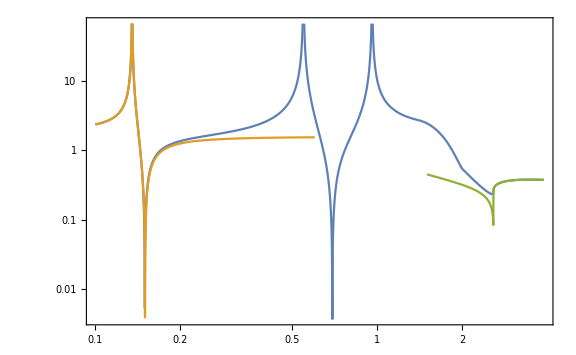

```mathematica
Do[crgval[ALPcouplingslist[[i]]]=cRGval["Gluon",10^3,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued[ma_]=cγGluing[ma,10^3,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
(*Eq. 2.72 from https://arxiv.org/pdf/2110.10698.pdf*)
cγγNeubertLow[ma_]=cγγEffChRotation[ma]-ma^2/(MASS["π^0"]^2-ma^2)*(δval+crgval["cu"]-crgval["cd"])+(2*3*Sum[Symbol["c"<>q]*CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"c","b"}}]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}]);
cγγNeubertHigh[ma_]=Abs[(2*3*Sum[Symbol["c"<>q]*CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"u","d","s","c","b"}}]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}])+(cγγEff[ma,cu,cd,cs,cc,cb,ct,cG,ce,cμ,cτ,10^3,"Loop c_G"]/.Table[Symbol["c"<>q]->crgval["c"<>q],{q,{"u","d","s","c","b"}}]/.{cG->1})];
LogLogPlot[{cγglued[ma],If[ma<0.6,Evaluate[Abs[cγγNeubertLow[ma]]],0],If[ma<1.5,0,Evaluate[Abs[cγγNeubertHigh[ma]]]]},{ma,0.1,3.9},Frame->True,ImageSize->Large]
```

## a->ff

### Kinematics

```mathematica
Do[
particleslist["2"<>particle]={particleFinal[particle],particleFinal[particle]};
prgroupname["2"<>particle]=If[MemberQ[listQuarks,particle]==True,"QCD jets","Leptonic"];
prclassname["2"<>particle]=If[MemberQ[listQuarks,particle]==True,"Hadronic, perturbative","Non-hadronic"];
Sfactor["2"<>particle]=1;
mLimitationMin["2"<>particle]=If[MemberQ[{"u","c","d","s","b"},particle]==True,Max[1.3,2*MASS[particleFinal[particle]]],0];
mLimitationMax["2"<>particle]=10000;
rule4MomentumConservation[expr_,"2"<>particle]:=ExpandScalarProduct[expr/.{pa->pf1+pf2}];
ruleScalarProducts[expr_,"2"<>particle]:=expr/.{ScalarProduct[pf1,pf2]->(ma^2-2 msymbolic[particleFinal[particle]]^2)/2,ScalarProduct[pf1,pa]->ma^2/2,ScalarProduct[pf2,pa]->ma^2/2,ScalarProduct[pf1,pf1]->msymbolic[particleFinal[particle]]^2,ScalarProduct[pf2,pf2]->msymbolic[particleFinal[particle]]^2};
Ncnumber["2"<>particle]=If[MemberQ[{"u","c","t","d","s","b"},particle]==True,3,1];
cfval["2"<>particle]=If[MemberQ[{"u","c","t","d","s","b"},particle]==True,cq,cl]
,{particle,{"u","d","s","c","b","t","e","μ","τ"}}]
```

### Matrix elements

```mathematica
Do[
M2body["2"<>particle]=-Symbol["c"<>particle](2msymbolic[particle])/fa SpinorUBar[pf1,msymbolic[particleFinal[particle]]].GA[5].SpinorV[pf2,msymbolic[particleFinal[particle]]]//Contract;
Mstar2body["2"<>particle]=M2body["2"<>particle]//ComplexConjugate;
M2symbolic2body["2"<>particle]=ruleKinematics[Ncnumber["2"<>particle]*FermionSpinSum[M2body["2"<>particle]*Mstar2body["2"<>particle]]/.{DiracTrace->TR}//ExpandScalarProduct//Simplify,"2"<>particle]//Simplify;
M2numeric2body["2"<>particle,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]= ruleSymbolsToNumbers[M2symbolic2body["2"<>particle],θηStandard,"No SM mixing"],
{particle,{"u","d","s","c","b","t","e","μ","τ"}}]
(*Matches Eq. 2.77 from https://arxiv.org/pdf/2110.10698.pdf is rescaling Subscript[c, bb] -> 2 Subscript[c, bb]*)
Assuming[ma>2*mb&&mb>0,Simplify[ΓsymbolicTemp[2,ma,"2b"]]]
```

(3 cb^2 mb^2 √(ma^2-4 mBplus^2))/(8 π fa^2)

## a->GG

### Kinematics

```mathematica
particleslist["2G"]={"G","G"};
Sfactor["2G"]=1/2;
prgroupname["2G"]="QCD jets";
prclassname["2G"]="Hadronic, perturbative";
mLimitationMin["2G"]=1.3;
mLimitationMax["2G"]=10000;
rule4MomentumConservation[expr_,"2G"]:=ExpandScalarProduct[expr/.{pa->pG1+pG2}];
ruleScalarProducts[expr_,"2G"]:=expr/.{ScalarProduct[pG1,pG2]->ma^2/2,ScalarProduct[pG1,pa]->ma^2/2,ScalarProduct[pG2,pa]->ma^2/2,ScalarProduct[pG1,pG1]->0,ScalarProduct[pG2,pG2]->0};
```

### Matrix elements

```mathematica
(*4 due to F^F = 2dA ^ 2dA*)
(*2 due to the fact that each gluon operator may annihilate each given process*)
(*1/2 due to the definition of F̃ = 1/2^F*)
M2body["2G"]=αs/(4Pi)cG*1/fa 4*2*1/2*FV[pG1,μ]PolarizationVector[pG1,ν]FV[pG2,α]PolarizationVector[pG2,β]LeviCivita[μ,ν,α,β]//Contract;
Mstar2body["2G"]=M2body["2G"]//ComplexConjugate;
(*Factor 8: sum over colors*)
QCDcorr["2G"]=(1+83/4 αs/Pi);
M2symbolic2body["2G"]=8ruleKinematics[DoPolarizationSums[DoPolarizationSums[M2body["2G"]*Mstar2body["2G"],pG1],pG2]*QCDcorr["2G"]//ExpandScalarProduct//Simplify,"2G"]//Simplify;
M2numeric2body["2G",ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]=ruleSymbolsToNumbers[M2symbolic2body["2G"],θηStandard,"No SM mixing"];
Print["Decay width into gluons:"]
(*Matches Eq. 2.75 from https://arxiv.org/pdf/2110.10698.pdf*)
Assuming[ma>0,Simplify[ΓsymbolicTemp[2,ma,"2G"]/.{mG->0}]]
```

Decay width into gluons:

(αs^2 (83 αs+4 π) cG^2 ma^3)/(32 π^4 fa^2)

## Widths/matrix elements exporting

## Definitions

```mathematica
Print["List of all processes:"]
DecayProcessesList=Keys[DownValues@particleslist][[All,1,1]]
Print["List of processes groups:"]
DecayProcessesGroups=Keys[DownValues@prgroupname][[All,1]]//DeleteDuplicates
Print["List of processes classes:"]
DecayProcessesClasses=Keys[DownValues@prclassname][[All,1]]//DeleteDuplicates
fulldescription={DecayProcessesList,Table[prgroupname[proc],{proc,DecayProcessesList}],Table[prclassname[proc],{proc,DecayProcessesList}]};
Join[{{"Process"},{"Process group"},{"Process class"}},fulldescription,2]
Print["Perturbative QCD processes:"]
DecayProcessesPertQCDlist=Cases[Transpose[fulldescription],{__,"Hadronic, perturbative"}][[All,1]]//Transpose
Print["Leptonic and γγ decay processes:"]
DecayProcessesNonHadronic=Cases[Transpose[fulldescription],{__,"Non-hadronic"}][[All,1]]//Transpose
Print["ChPT decay processes:"]
DecayProcessesChPTlist=Cases[Transpose[fulldescription],{__,"Hadronic, ChPT"}][[All,1]]//Transpose
(*Effective coupling for decays into gluons*)
Do[cGGvalProcess[process,ma_,cG_,cu_,cd_,cs_,cc_,cb_,ct_]=Abs[cG+If[process=="2G",cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}],0]],{process,DecayProcessesList}];
Γlist[ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]:=Join[{ma},Table[Γnumeric[process,ma,fa,cu,cd,cs,cc,cb,ct,cGGvalProcess[process,ma,cG,cu,cd,cs,cc,cb,ct],cγ,ce,cμ,cτ],{process,DecayProcessesList}]]
(*Matching between ChPT and perturbative QCD widths*)
maMatching[dataΓChPT_,dataΓpert_]:=Block[{},
ΓchptInt[ma_]=Interpolation[dataΓChPT,InterpolationOrder->1][ma];
ΓpertqcdInt[ma_]=Interpolation[dataΓpert,InterpolationOrder->1][ma];
tabt=Table[{ma,Abs[ΓchptInt[ma]-ΓpertqcdInt[ma]]},{ma,1.75,3,0.001}];
maMatchHadronic=Take[SortBy[tabt,#[[2]]&],{1,2}][[All,1]]//Min;
{maMatchHadronic,Join[Select[dataΓChPT,#[[1]]<=maMatchHadronic&],Select[dataΓpert,#[[1]]>maMatchHadronic&]]}
]
(*Resonant domains to be shown in plots*)
Δrange1=0.007;
{πDomain,ηDomain,ηprDomain}=Join[Table[{x,10^99.},{x,MASS[#]-Δrange1,MASS[#]+Δrange1,10^-3.}]]&/@{"π^0","η","η'"};
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
{Join[{"m_a/GeV"},DecayProcessesList],Γlist[1.5,10^3,1,1,1,1,1,1,1,1,1,1,1]}//TableForm
```

List of all processes:

{2b,2c,2d,2e,2G,2s,2π^+2π^-,2t,2u,2γ,2μ,2τ,2ϕ,2ω,3π^0,3η,K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^(*+)K^(*-),K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ωπ^+π^-,η'2π^0,η'π^+π^-}

List of processes groups:

{QCD jets,Leptonic,4π,2γ,2V,3π,3η,KKπ,γππ,η2π,ωππ,η'2π}

List of processes classes:

{Hadronic, perturbative,Non-hadronic,Hadronic, ChPT}

(Process | 2b | 2c | 2d | 2e | 2G | 2s | 2π^+2π^- | 2t | 2u | 2γ | 2μ | 2τ | 2ϕ | 2ω | 3π^0 | 3η | K^(*0)(K̄)^(*0) | K^0(K̄)^0π^0 | K^(*+)K^(*-) | K^-K^0π^+ | K^+K^-π^0 | K^+(K̄)^0π^- | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ωπ^+π^- | η'2π^0 | η'π^+π^-
Process group | QCD jets | QCD jets | QCD jets | Leptonic | QCD jets | QCD jets | 4π | QCD jets | QCD jets | 2γ | Leptonic | Leptonic | 2V | 2V | 3π | 3η | 2V | KKπ | 2V | KKπ | KKπ | KKπ | γππ | η2π | η2π | 4π | 3π | ωππ | η'2π | η'2π
Process class | Hadronic, perturbative | Hadronic, perturbative | Hadronic, perturbative | Non-hadronic | Hadronic, perturbative | Hadronic, perturbative | Hadronic, ChPT | Hadronic, perturbative | Hadronic, perturbative | Non-hadronic | Non-hadronic | Non-hadronic | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT)

Perturbative QCD processes:

{2b,2c,2d,2G,2s,2t,2u}

Leptonic and γγ decay processes:

{2e,2γ,2μ,2τ}

ChPT decay processes:

{2π^+2π^-,2ϕ,2ω,3π^0,3η,K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^(*+)K^(*-),K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ωπ^+π^-,η'2π^0,η'π^+π^-}

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.28069×10^-8+1.25011×10^-26 ⅈ and 2.99855×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.29701×10^-8+1.93291×10^-26 ⅈ and 3.05562×10^-10 for the integral and error estimates.

m_a/GeV | 2b | 2c | 2d | 2e | 2G | 2s | 2π^+2π^- | 2t | 2u | 2γ | 2μ | 2τ | 2ϕ | 2ω | 3π^0 | 3η | K^(*0)(K̄)^(*0) | K^0(K̄)^0π^0 | K^(*+)K^(*-) | K^-K^0π^+ | K^+K^-π^0 | K^+(K̄)^0π^- | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ωπ^+π^- | η'2π^0 | η'π^+π^-
1.5 | 0 | 0 | 3.84109×10^-12 | 1.49208×10^-14 | 8.13135×10^-8 | 1.17581×10^-9 | 3.20173×10^-9 | 0 | 8.21728×10^-13 | 9.06156×10^-14 | 6.51526×10^-10 | 0 | 0 | 0 | 7.70913×10^-10 | 0 | 0 | 2.8286×10^-9 | 0 | 7.53854×10^-9 | 5.16826×10^-9 | 7.53854×10^-9 | 1.00893×10^-9 | 8.92934×10^-8 | 1.76976×10^-7 | 6.48504×10^-9 | 4.68294×10^-9 | 3.517×10^-11 | 5.8765×10^-10 | 1.11301×10^-9

## Block producing the output for export the widths

```mathematica
BlockWidthsTabulation[Model_,fa_,Λ_]:=Module[{},
(*Fixing the values of the low-energy ALP couplings given the model and Λ*)
Do[crgval[ALPcouplingslist[[i]]]=cRGval[Model,Λ,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued[ma_]=cγGluing[ma,Λ,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
(*The range of masses for which the widths tabulation will be performed*)
Δrange=0.002;
mstep1=0.001;
mstep2=0.005;
marangetemp=Join[Table[ma,{ma,0.01,1.2,mstep1}],Table[ma,{ma,1.205,3.,mstep2}]];
marange1=Select[marangetemp,!(MASS["π^0"]-Δrange<#<MASS["π^0"]+Δrange)&&!(MASS["η"]-Δrange<#<MASS["η"]+Δrange)&&!(MASS["η'"]-Δrange<#<MASS["η'"]+Δrange)&];
marange2=Table[ma,{ma,3.01,10.,mstep2}];
marange=Join[marange1,marange2];
ΓlistTemp=Join[Join[Table[{"m_a, GeV"},3],fulldescription,2],ParallelTable[Quiet[Γlist[ma,fa,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],cγglued[ma],crgval["ce"],crgval["cμ"],crgval["cτ"]]],{ma,marange1}],ParallelTable[Quiet[Γlist[ma,fa,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],cγglued[ma],crgval["ce"],crgval["cμ"],crgval["cτ"]]],{ma,marange2}]];
Do[Γlist1[proc]={Total[#]}&/@Drop[Cases[Transpose[ΓlistTemp],{__,proc,__}]//Transpose,3],{proc,DecayProcessesClasses}];
datatemp=maMatching[Join[Partition[marange,1],Γlist1["Hadronic, ChPT"],2],Join[Partition[marange,1],Γlist1["Hadronic, perturbative"],2]];
{maMatchGivenModel,Γlist1["Hadronic, total"]}={datatemp[[1]],datatemp[[2]][[All,{2}]]};
ΓlistTotal=Join[ΓlistTemp,Join[Table[{"Non-hadronic, total"},3],Γlist1["Non-hadronic"]],Join[Table[{"Hadronic, total"},3],Γlist1["Hadronic, total"]],Join[Table[{"Total"},3],Γlist1["Non-hadronic"]+Γlist1["Hadronic, total"]],2];
ΓlistTotal1=Join[Take[ΓlistTotal,3],{{"m_match (ChPT<->Perturbative) (GeV). Above this mass, one should use the QCD perturbative width as the total hadronic width. Below - ChPT: ",maMatchGivenModel}},{ALPcouplingslist,rgflow},Drop[ΓlistTotal,3]];
ExportData={Model,{ALPcouplingslist,rgflow},maMatchGivenModel,ΓlistTotal};
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths",ToString@StringForm["Widths-model-``-scale-``-GeV.m",Sequence@@{Model,Λ//CForm//ToString}]}],ExportData,"MX"];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths","Widths-model-Fermion universal-scale-1000.-GeV.csv"}],ΓlistTotal1/.{"η2π^0"->"Eta2Pi0","2γ"->"2gamma","2π^+2π^-"->"2Piplus2Piminus","m_a, GeV"->"ma GeV","2μ"->"2mu","2τ"->"2tau","2ϕ"->"2phi","2ω"->"2omega","3π^0"->"3pi0","3η"->"3eta","K^(*0)(K̄)^(*0)"->"2Kstar0","K^0(K̄)^0π^0"->"K0LK0SPi0","K^(*+)K^(*-)"->"2Kstarcharged","K^-K^0π^+"->"KminusK0Piplus","K^+K^-π^0"->"2KchargedPi0","γπ^+π^-"->"gamma2Picharged","ηπ^+π^-"->"Eta2Picharged","π^+π^-2π^0"->"2Picharged2Pi0","π^+π^-π^0"->"2PichargedPi0","ωπ^+π^-"->"Omega2Picharged","η'2π^0"->"Etapr2Pi0","η'π^+π^-"->"Etapr2Picharged","K^+(K̄)^0π^-"->"KplusK0Piminus"},"csv"];
]
ythg[ma_]:={Join[DecayProcessesList],Drop[(16 Pi^2)^2 10^9 Γlist[ma,10^3,0,0,0,0,0,0,1,cγglued[ma],0,0,0],1]}
```

```mathematica
rgflow
```

{-0.0166127,-0.0166127,-0.0166127,-0.0166127,-0.00161272,-0.00153892,1.,0.,0.,0.,0.,0.}

-Graphics-

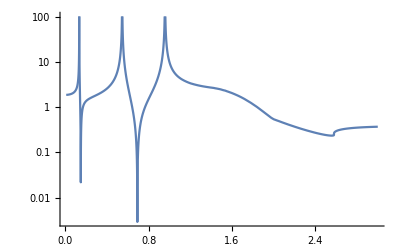

```mathematica
LogPlot[cγglued[ma],{ma,0.01,3.}]
```

### Exporting

```mathematica
ModelForExporting=dropdownDialog[ModelListAll,"Select the model for decay widths exporting:"]
ΛChoice=DialogInput[{cut=""},Column[{"Enter the scale Λ in GeV:",InputField[Dynamic[cut],Expression],Button["Proceed",DialogReturn[cut],ImageSize->Automatic]}]]//N
BlockWidthsTabulation[ModelForExporting,1,ΛChoice]
```

## Matrix elements exporting (for SensCalc)

### Matrix element for KKπ processes without the interpolation part (it would change a little but slows down SensCalc calculations)

```mathematica
Do[
sublistexport={"Contact","f_2-mediated","S-mediated","V-mediated"};
Msymbolic3bodyExp[process,"Total"]=Sum[Msymbolic3body[process,sub],{sub,sublistexport}];
MsymbolicStar3bodyExp[process,"Total"]=Sum[MsymbolicStar3body[process,sub],{sub,sublistexport}];
M2numeric3bodyExp[process,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=ruleSymbolsToNumbers[Msymbolic3bodyExp[process,"Total"]*MsymbolicStar3bodyExp[process,"Total"],θηStandard,"All",δval]*Ffunction[ma]^2,{process,proclistKKπ}]
```

### Exporting block

```mathematica
BlockMsquaredTabulation[Model_,Λ_,proclist_]:=Module[{},
(*Fixing the values of the low-energy ALP couplings given the model and Λ*)
Do[crgval[ALPcouplingslist[[i]]]=cRGval[Model,Λ,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued[ma_]=cγGluing[ma,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
(*Matrix elements squared in terms of the ALP mass, energy of the particle 1 and the energy of the particle 3*)
Do[
If[MemberQ[proclistKKπ,process]==False,M2numeric3bodyExport[process,ma_,m12_,m23_]=M2numeric3body[process,ma,1,cu,cd,cs,cc,cb,ct,cG,cγ,ce,cμ,cτ,m12,m23]/.tableValuesReplacement[Model,Λ]/.{m12->M12[E1,E3],m23->M23[E1]}/.{m->ma,m1->MASS[particleslist[process][[1]]],m2->MASS[particleslist[process][[2]]],m3->MASS[particleslist[process][[3]]]}/.{Ffunction[ma]->1}];
If[MemberQ[proclistKKπ,process]==True,M2numeric3bodyExport[process,ma_,m12_,m23_]=M2numeric3bodyExp[process,ma,1,cu,cd,cs,cc,cb,ct,cG,cγ,ce,cμ,cτ,m12,m23]/.tableValuesReplacement[Model,Λ]/.{m12->M12[E1,E3],m23->M23[E1]}/.{m->ma,m1->MASS[particleslist[process][[1]]],m2->MASS[particleslist[process][[2]]],m3->MASS[particleslist[process][[3]]]}/.{Ffunction[ma]->1}];
,{process,proclist}];
listtoexport={proclist,Table[particleslist[proc],{proc,proclist}],Table[M2numeric3bodyExport[process,ma,m12,m23],{process,proclist}]};
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths",ToString@StringForm["Matrix-elements-squared-model-``-scale-``-GeV.m",Sequence@@{Model,Λ//CForm//ToString}]}],listtoexport,"MX"]
]
```

### Exporting

```mathematica
Print["Model for exporting:"]
ModelForExporting=dropdownDialog[ModelListAll,"Select the model for decay widths exporting:"]
Print["Scale Λ:"]
ΛChoice=DialogInput[{cut=""},Column[{"Enter the scale Λ in GeV:",InputField[Dynamic[cut],Expression],Button["Proceed",DialogReturn[cut],ImageSize->Automatic]}]]//N
Print["For which processes the matrix elements will be exported:"]
DecayProcessesForExporting=selectionDialog[DecayProcessesList,"Select the list of decays for which the matrix elements will be exported:"]
BlockMsquaredTabulation[ModelForExporting,ΛChoice,DecayProcessesForExporting]
```

Model for exporting:

Fermion universal

Scale Λ:

1000.

For which processes the matrix elements will be exported:

{K^0(K̄)^0π^0,3π^0,K^+(K̄)^0π^-,K^+K^-π^0,K^-K^0π^+,ηπ^+π^-,π^+π^-π^0,ωπ^+π^-,η'2π^0,η'π^+π^-,η2π^0,γπ^+π^-}

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\phenomenology\decay widths\Matrix-elements-squared-model-Fermion universal-scale-1000.-GeV.m

# Plots: decay widths

## Decay width

## Definitions

```mathematica
tableforplots[rescaling_,data_]:=Table[{#[[1]],rescaling*#[[i]]}&/@data,{i,2,Length[data[[1]]],1}]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
widthProcess[data_,proc_]:=Drop[Join[data[[All,{1}]],Cases[Transpose[data],{__,proc,__}|{proc,__}]//Transpose,2],3]
widthTotal[datawidths_]:=Join[datawidths[[All,{1}]],{Total[#[]]}&/@datawidths[[All,Range[2,Length[datawidths[[1]]]]]]]
MASS["π^0"]=0.135;
MASS["η"]=0.547;
MASS["η'"]=0.958;
```

## A particular model and scale

### Model importing

```mathematica
ModelsListPaths=FileNames["Widths-model-*.m",FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths"}]];
ModelsListFilenames=Table[Last@FileNameSplit@ModelsListPaths[[i]],{i,1,Length[ModelsListPaths],1}];
FilenameParameters[i_]:=StringCases[ModelsListFilenames[[i]],"Widths-model-"~~model__~~"-scale-"~~scale__~~"-GeV.m":>{model,scale}][[1]]
Print["List of available models:"]
ModelsList=Table[FilenameParameters[i],{i,1,Length[ModelsListFilenames],1}]
Print["Selected model:"]
SelectedModel=dropdownDialog[ModelsList,"Select the ALP model and scale:"]
SelectedModelDataTemp=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths",ToString@StringForm["Widths-model-``-scale-``-GeV.m",Sequence@@{SelectedModel[[1]],SelectedModel[[2]]}]}],"MX"];
{model,couplingsValsModel,maMatch}={SelectedModelDataTemp[[1]],SelectedModelDataTemp[[2]],SelectedModelDataTemp[[3]]};
Print["Coupling patterns:"]
couplingsValsModel//TableForm
Print["Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:"]
maMatch
SelectedModelData=SelectedModelDataTemp[[4]]/.{0.->10^-99.,0->10^-99.};
Print["All decays:"]
SelectedModelDecays=Drop[SelectedModelData[[1]],1]
Print["Decays groups:"]
SelectedModelDecayGroups=Drop[SelectedModelData[[2]],1]//DeleteDuplicates
Print["Decays classes:"]
SelectedModelDecayClasses=Drop[SelectedModelData[[3]],1]//DeleteDuplicates
meanings=Take[SelectedModelData,{1,3}];
(*Processes belonging to the given group*)
Do[ProcessesGroup[group]=(Cases[Transpose[meanings],{__,group,__}|{group,__}]//Transpose)[[1]],{group,SelectedModelDecayGroups}]
(*Processes belonging to the given class*)
Do[ProcessesClass[class]=(Cases[Transpose[meanings],{__,class}]//Transpose)[[1]],{class,SelectedModelDecayClasses}]
(*Processes groups belonging to the given class*)
Do[GroupsClass[class]=(Cases[Transpose[meanings],{__,class}]//Transpose)[[2]]//DeleteDuplicates,{class,SelectedModelDecayClasses}]
Do[SelectedModelWidths[meanings[[1]][[i]]]=widthProcess[SelectedModelData,meanings[[1]][[i]]],{i,2,Length[meanings[[1]]],1}]
Do[GroupWidthTot[group]=Join[Drop[SelectedModelData,3][[All,{1}]],Sum[SelectedModelWidths[proc][[All,{2}]],{proc,ProcessesGroup[group]}],2]
,{group,SelectedModelDecayGroups}]
TableRangesMixing=Join[Table[{xx,10^99},{xx,MASS["π^0"]-0.005,MASS["π^0"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η"]-0.005,MASS["η"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η'"]-0.005,MASS["η'"]+0.005,0.001}]];
```

List of available models:

{{Fermion universal,1000.},{Fermion universal,173.},{Gluon,1000.},{Gluon Soreq,1000.}}

Selected model:

{Fermion universal,1000.}

Coupling patterns:

cu | cd | cs | cc | cb | ct | cG | ce | cμ | cτ | cW | cB
0.873903 | 0.986097 | 0.986097 | 0.873903 | 1.04675 | 0.906263 | 0. | 1.0561 | 1.0561 | 1.0561 | 0. | 0.

Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:

2.249

All decays:

{2b,2c,2d,2e,2G,2s,2π^+2π^-,2t,2u,2γ,2μ,2τ,2ϕ,2ω,3π^0,3η,K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^(*+)K^(*-),K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ωπ^+π^-,η'2π^0,η'π^+π^-,Non-hadronic, total,Hadronic, total,Total}

Decays groups:

{QCD jets,Leptonic,4π,2γ,2V,3π,3η,KKπ,γππ,η2π,ωππ,η'2π,Non-hadronic, total,Hadronic, total,Total}

Decays classes:

{Hadronic, perturbative,Non-hadronic,Hadronic, ChPT,Non-hadronic, total,Hadronic, total,Total}

```mathematica
SelectedModelDecays
SelectedModelData[[600]]
```

{2b,2c,2d,2e,2G,2s,2π^+2π^-,2t,2u,2γ,2μ,2τ,2ϕ,2ω,3π^0,3η,K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^(*+)K^(*-),K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ωπ^+π^-,η'2π^0,η'π^+π^-,Non-hadronic, total,Hadronic, total,Total}

{0.612,1.×10^-99,1.×10^-99,1.×10^-99,6.78982×10^-9,1.×10^-99,1.×10^-99,2.49855×10^-17,1.×10^-99,1.×10^-99,2.52797×10^-8,0.000281252,1.×10^-99,1.×10^-99,1.×10^-99,-1.75648×10^-8,1.×10^-99,1.×10^-99,1.×10^-99,1.×10^-99,1.×10^-99,1.×10^-99,1.×10^-99,4.17502×10^-8,1.×10^-99,1.×10^-99,8.36717×10^-17,7.43292×10^-8,1.×10^-99,1.×10^-99,1.×10^-99,0.000281284,9.85146×10^-8,0.000281382}

### Plots

#### Hadronic widths

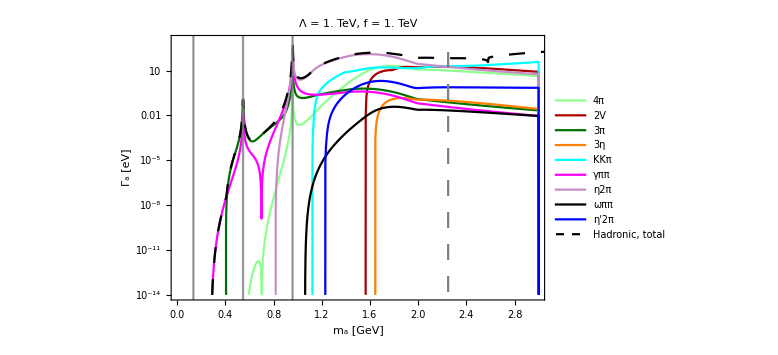

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\Hadronic-widths-Fermion universal.pdf

```mathematica
hadronicdecaysplot=Join[GroupsClass["Hadronic, ChPT"],GroupsClass["Hadronic, total"]];
scale=10^3;
img=Show[ListLogPlot[Evaluate[Table[{#[[1]],(#[[2]])/scale^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthTot[group],#[[1]]>1.75&],GroupWidthTot[group]],{group,hadronicdecaysplot}]],PlotStyle->{{Thick,Lighter@Lighter@Green},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Orange},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Blue},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@hadronicdecaysplot,Right],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.01,2.99},{10^-14,10^3}},PlotLabel->Style[Row[{"Λ = ",Interpreter["Number"][SelectedModel[[2]]]*10^-3," TeV, f = ",10^-3. scale," TeV"}],18,Black]],ListLogPlot[Evaluate[Table[{maMatch,10^x},{x,-99,99,0.5}]],Joined->True,PlotStyle->{{Thick,Gray,Dashing[0.02]}}],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.2]]},2->{Bottom,Directive[Gray,Opacity[0.2]]},3->{Bottom,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Hadronic-widths-``.pdf",Sequence@@{SelectedModel[[1]]}]}],img]
```

#### Total widths

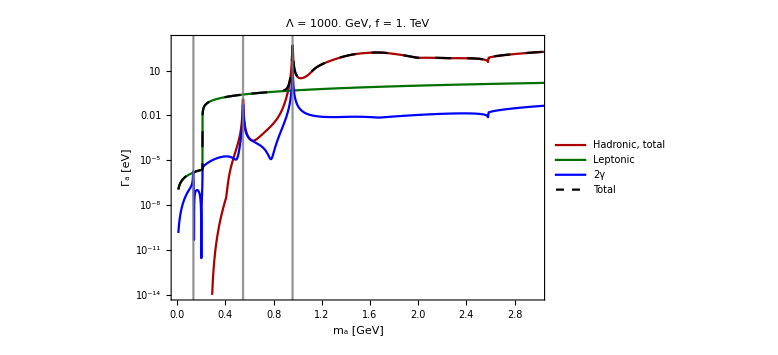

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\Total-widths-Fermion universal.pdf

```mathematica
decaysplot=Join[GroupsClass["Hadronic, total"],GroupsClass["Non-hadronic"],GroupsClass["Total"]];
scale=1;
img2=Show[ListLogPlot[Evaluate[Table[{#[[1]],#[[2]]*(10^-3*scale)^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthTot[group],#[[1]]>1.75&],GroupWidthTot[group]],{group,decaysplot}]],PlotStyle->{{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@decaysplot,Right],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.01,2.99},{10^-14,10^3}},PlotLabel->Style[Row[{"Λ = ",SelectedModel[[2]]," GeV, f = ",scale//N," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.2]]},2->{Bottom,Directive[Gray,Opacity[0.2]]},3->{Bottom,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Total-widths-``.pdf",Sequence@@{SelectedModel[[1]]}]}],img2]
```

#### Branching ratios

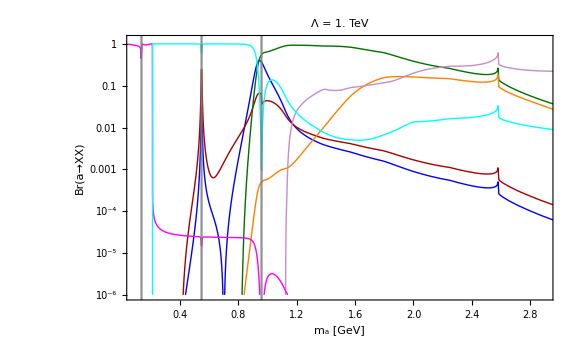

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\Br-ratios-Fermion universal-scale-1000.-GeV.pdf

```mathematica
brgroup1={"γππ","3π","η2π","4π","KKπ"};
Do[BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@Join[GroupWidthTot[proc],GroupWidthTot["Total"][[All,{2}]],2],{proc,brgroup1}]
brgroup2={"2e","2μ"};
brlist=Join[brgroup1,brgroup2];
Do[BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@Join[SelectedModelWidths[proc],GroupWidthTot["Total"][[All,{2}]],2],{proc,brgroup2}]
BrRatiosPBC["2μ"]={#[[1]],(#[[2]])/(#[[3]])}&/@Join[SelectedModelWidths["2μ"],GroupWidthTot["Leptonic"][[All,{2}]],2];
img3=Show[ListLogPlot[Evaluate[Table[BrRatios[proc],{proc,brlist}]],PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Orange},{Thick,Lighter@Lighter@Purple},{Thick,Magenta},{Thick,Cyan},{Thick,Cyan,Dashing[0.02]},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Br(a→XX)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.09,2.9},{10^-6,1.2}},PlotLabel->Style[Row[{"Λ = ",Interpreter["Number"][SelectedModel[[2]]]*10^-3," TeV"}],18,Black]],LogPlot[{x,x,x,x,x,x,x,x,x,x,x,x,x,x},{x,2,10},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green}},PlotLegends->Placed[Style[#,15]&/@{"γππ","3π","η2π"},{0.65,0.13}]],LogPlot[{x,x,x,x,x,x,x,x,x,x,x,x,x,x},{x,2,10},PlotStyle->{{Thick,Orange},{Thick,Lighter@Lighter@Purple},{Thick,Magenta}},PlotLegends->Placed[Style[#,15]&/@{"4π","KKπ","2e"},{0.65,0.13}]],LogPlot[{x,x,x,x,x,x,x,x,x,x,x,x,x,x},{x,2,10},PlotStyle->{{Thick,Cyan}},PlotLegends->Placed[Style[#,15]&/@{"2μ"},{0.65,0.13}]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.2]]},2->{Bottom,Directive[Gray,Opacity[0.2]]},3->{Bottom,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Br-ratios-``-scale-``-GeV.pdf",Sequence@@{SelectedModel[[1]],SelectedModel[[2]]}]}],img3]
```

#### Full lifetime vs lifetime assuming only leptonic decays

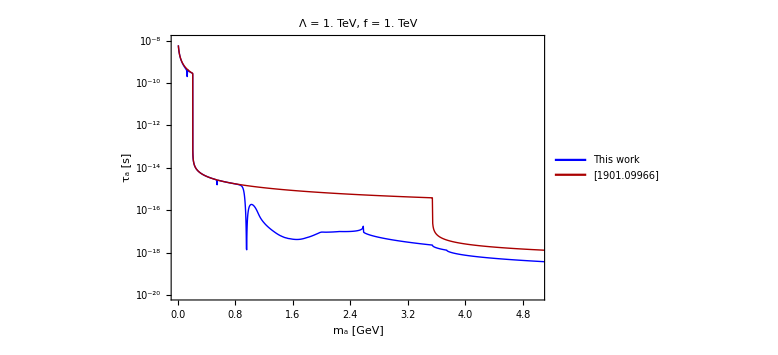

```mathematica
If[SelectedModel[[1]]=="Fermion universal",
decaysplot=Join[GroupsClass["Non-hadronic"],GroupsClass["Total"]];
scale=10^3;
img4=Show[ListLogPlot[{{#[[1]],(scale)^2(6.58*10^-25)/(#[[2]])}&/@GroupWidthTot["Total"],{#[[1]],(scale)^2(6.58*10^-25)/(#[[2]])}&/@GroupWidthTot["Leptonic"]},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@{"This work","[1901.09966]"},{0.8,0.8}],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "τ_a [s]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.01,5},{10^-20,10^-8}},PlotLabel->Style[Row[{"Λ = ",Interpreter["Number"][SelectedModel[[2]]] 10^-3," TeV, f = ",10^-3. scale," TeV"}],18,Black]]];
Export[FileNameJoin[{NotebookDirectory[],"plots","Lifetimes-update.pdf"}],img4];
img4
]
```

### Exporting branching ratios (for SensCalc)

```mathematica
(*Br ratios in terms of the ALP mass*)
gr1={"QCD jets"};
Do[
mmaxproc=If[group!="QCD jets",maMatch,10];
mminproc=If[group=="QCD jets",maMatch,0];
BrRatioExport[group,ma_]=If[mminproc<=ma<mmaxproc,Evaluate[(Interpolation[GroupWidthTot[group],InterpolationOrder->1][ma])/(Interpolation[SelectedModelWidths["Total"],InterpolationOrder->1][ma])],0];
,{group,gr1}];
gr2={"2e","2μ","2τ","2γ","π^+π^-π^0","γπ^+π^-","π^+π^-2π^0","2π^+2π^-","η2π^0","ηπ^+π^-","K^(*+)K^(*-)","K^(*0)(K̄)^(*0)","K^0(K̄)^0π^0","K^-K^0π^+","K^+K^-π^0","K^+(K̄)^0π^-","ωπ^+π^-","3π^0","η'2π^0","η'π^+π^-","2ω"};
Do[
mmaxproc=If[MemberQ[{"2e","2μ","2τ","2γ"},proc]==False,maMatch,99999];
mminproc=0;

BrRatioExport[proc,ma_]=If[mminproc<=ma<mmaxproc,Evaluate[(Interpolation[SelectedModelWidths[proc],InterpolationOrder->1][ma])/(Interpolation[SelectedModelWidths["Total"],InterpolationOrder->1][ma])],0];
,{proc,gr2}];
(*gr3={"D^charged-pair","D^0-pair"};
BrRatioExport["D^charged-pair",ma_]=BrRatioExport["D^0-pair",ma_]=0.5(Interpolation[SelectedModelWidths["2c"],InterpolationOrder->1][ma])/(Interpolation[SelectedModelWidths["Total"],InterpolationOrder->1][ma]);*)
partlist2Temp=Table[particleslist[proc],{proc,gr2}]/.{{"e","e"}->{"e^+","e^-"},{"μ","μ"}->{"μ^+","μ^-"},{"τ","τ"}->{"τ^+","τ^-"},"A"->"γ","K^0"->"K_L","(K̄)^0"->"K_S"};
partlist2=Table[Join[partlist2Temp[[i]],Table["Null",4-Length[partlist2Temp[[i]]]]],{i,1,Length[partlist2Temp],1}];
partlistFull=Join[{{"g","ḡ","Null","Null"}},partlist2];
Listtoexport[ma_]={Join[gr1/.{"QCD jets"->"Jets-GG"},gr2(*,gr3*)],partlistFull,Table[BrRatioExport[process,ma],{process,Join[gr1,gr2(*,gr3*)]}]};
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths",ToString@StringForm["Br-ratios-SensCalc-model-``-scale-``-GeV.m",Sequence@@{SelectedModel[[1]],SelectedModel[[2]]}]}],Listtoexport[ma],"MX"]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\phenomenology\decay widths\Br-ratios-SensCalc-model-Fermion universal-scale-1000.-GeV.m

```mathematica
listtoexport
```

```mathematica
maMatch
```

```mathematica
listtoexport[2.9]
```

## Two models/scales

```mathematica
SelectedModelsDataTemp[[1]][[1]]
SelectedModelsDataTemp[[1]][[2]]
SelectedModelsDataTemp[[1]][[3]]
```

```mathematica
SelectedModelDataTemp[[2]]
```

### Model importing

```mathematica
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{"Select the experiments for which the number of events will be computed. The meaning is ",phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
ModelsListPaths=FileNames["Widths-model-*.m",FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths"}]];
ModelsListFilenames=Table[Last@FileNameSplit@ModelsListPaths[[i]],{i,1,Length[ModelsListPaths],1}];
FilenameParameters[i_]:=
StringCases[ModelsListFilenames[[i]],"Widths-model-"~~model__~~"-scale-"~~scale__~~"-GeV.m":>{model,scale}][[1]]
Print["List of available models:"]
ModelsList=Table[FilenameParameters[i],{i,1,Length[ModelsListFilenames],1}]
Print["Selected model:"]
SelectedModels=selectionDialog[ModelsList,"Select two ALP models/scales:"]
SelectedModelsDataTemp=meaningsModels=couplingsValsModels=models=maMatches=SelectedModelsData=SelectedModelsDecays=SelectedModelsDecayGroups=SelectedModelsDecayClasses={0,0};
Do[SelectedModelsDataTemp[[i]]=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths",ToString@StringForm["Widths-model-``-scale-``-GeV.m",Sequence@@{SelectedModels[[i]][[1]],SelectedModels[[i]][[2]]}]}],"MX"];
{models[[i]],couplingsValsModels[[i]],maMatches[[i]]}={SelectedModelsDataTemp[[i]][[1]],SelectedModelsDataTemp[[i]][[2]],SelectedModelsDataTemp[[i]][[3]]};
SelectedModelsData[[i]]=SelectedModelsDataTemp[[i]][[4]]/.{0.->10^-99.,0->10^-99.};
SelectedModelsDecays[[i]]=Drop[SelectedModelsData[[i]][[1]],1];
SelectedModelsDecayGroups[[i]]=Drop[SelectedModelsData[[i]][[2]],1]//DeleteDuplicates;
SelectedModelsDecayClasses[[i]]=Drop[SelectedModelsData[[i]][[3]],1]//DeleteDuplicates;
meaningsModels[[i]]=Take[SelectedModelsData[[i]],{1,3}];
(*Processes belonging to the given group*)
Do[ProcessesGroups[i,group]=(Cases[Transpose[meaningsModels[[i]]],{__,group,__}|{group,__}]//Transpose)[[1]],{group,SelectedModelsDecayGroups[[i]]}];
(*Processes belonging to the given class*)
Do[ProcessesClasses[i,class]=(Cases[Transpose[meaningsModels[[i]]],{__,class}]//Transpose)[[1]],{class,SelectedModelsDecayClasses[[i]]}];
(*Processes groups belonging to the given class*)
Do[GroupsClasses[i,class]=(Cases[Transpose[meaningsModels[[i]]],{__,class}]//Transpose)[[2]]//DeleteDuplicates,{class,SelectedModelsDecayClasses[[i]]}];
Do[SelectedModelsWidths[i,meaningsModels[[i]][[1]][[j]]]=widthProcess[SelectedModelsData[[i]],meaningsModels[[i]][[1]][[j]]],{j,2,Length[meaningsModels[[i]][[1]]],1}];
Do[GroupWidthsTot[i,group]=Join[Drop[SelectedModelsData[[i]],3][[All,{1}]],Sum[SelectedModelsWidths[i,proc][[All,{2}]],{proc,ProcessesGroups[i,group]}],2];
,{group,SelectedModelsDecayGroups[[i]]}]
,{i,1,2,1}];
Print["Coupling patterns:"]
couplingsValsModels//TableForm
Print["Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:"]
maMatches
Print["All decays:"]
SelectedModelsDecays
Print["Decays groups:"]
SelectedModelsDecayGroups
Print["Decays classes:"]
meaningsModels//TableForm
TableRangesMixing=Join[Table[{xx,10^99},{xx,MASS["π^0"]-0.005,MASS["π^0"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η"]-0.005,MASS["η"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η'"]-0.005,MASS["η'"]+0.005,0.001}]];
```

List of available models:

{{Fermion universal,1000.},{Fermion universal,173.},{Gluon,1000.},{Gluon Soreq,1000.}}

Selected model:

{{Fermion universal,1000.},{Fermion universal,173.}}

Coupling patterns:

cu
cd
cs
cc
cb
ct
cG
ce
cμ
cτ
cW
cB | 0.873903
0.986097
0.986097
0.873903
1.04675
0.906263
0.
1.0561
1.0561
1.0561
0.
0.
cu
cd
cs
cc
cb
ct
cG
ce
cμ
cτ
cW
cB | 1.07
1.07
1.07
1.07
1.
1.
0.
1.
1.
1.
0.
0.

Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:

{2.249,2.268}

All decays:

{{2b,2c,2d,2e,2G,2s,2π^+2π^-,2t,2u,2γ,2μ,2τ,2ϕ,2ω,3π^0,3η,K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^(*+)K^(*-),K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ωπ^+π^-,η'2π^0,η'π^+π^-,Non-hadronic, total,Hadronic, total,Total},{2b,2c,2d,2e,2G,2s,2π^+2π^-,2t,2u,2γ,2μ,2τ,2ϕ,2ω,3π^0,3η,K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^(*+)K^(*-),K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ωπ^+π^-,η'2π^0,η'π^+π^-,Non-hadronic, total,Hadronic, total,Total}}

Decays groups:

{{QCD jets,Leptonic,4π,2γ,2V,3π,3η,KKπ,γππ,η2π,ωππ,η'2π,Non-hadronic, total,Hadronic, total,Total},{QCD jets,Leptonic,4π,2γ,2V,3π,3η,KKπ,γππ,η2π,ωππ,η'2π,Non-hadronic, total,Hadronic, total,Total}}

Decays classes:

m_a, GeV
2b
2c
2d
2e
2G
2s
2π^+2π^-
2t
2u
2γ
2μ
2τ
2ϕ
2ω
3π^0
3η
K^(*0)(K̄)^(*0)
K^0(K̄)^0π^0
K^(*+)K^(*-)
K^-K^0π^+
K^+K^-π^0
K^+(K̄)^0π^-
γπ^+π^-
η2π^0
ηπ^+π^-
π^+π^-2π^0
π^+π^-π^0
ωπ^+π^-
η'2π^0
η'π^+π^-
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
QCD jets
QCD jets
QCD jets
Leptonic
QCD jets
QCD jets
4π
QCD jets
QCD jets
2γ
Leptonic
Leptonic
2V
2V
3π
3η
2V
KKπ
2V
KKπ
KKπ
KKπ
γππ
η2π
η2π
4π
3π
ωππ
η'2π
η'2π
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Non-hadronic
Hadronic, perturbative
Hadronic, perturbative
Hadronic, ChPT
Hadronic, perturbative
Hadronic, perturbative
Non-hadronic
Non-hadronic
Non-hadronic
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Non-hadronic, total
Hadronic, total
Total
m_a, GeV
2b
2c
2d
2e
2G
2s
2π^+2π^-
2t
2u
2γ
2μ
2τ
2ϕ
2ω
3π^0
3η
K^(*0)(K̄)^(*0)
K^0(K̄)^0π^0
K^(*+)K^(*-)
K^-K^0π^+
K^+K^-π^0
K^+(K̄)^0π^-
γπ^+π^-
η2π^0
ηπ^+π^-
π^+π^-2π^0
π^+π^-π^0
ωπ^+π^-
η'2π^0
η'π^+π^-
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
QCD jets
QCD jets
QCD jets
Leptonic
QCD jets
QCD jets
4π
QCD jets
QCD jets
2γ
Leptonic
Leptonic
2V
2V
3π
3η
2V
KKπ
2V
KKπ
KKπ
KKπ
γππ
η2π
η2π
4π
3π
ωππ
η'2π
η'2π
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Non-hadronic
Hadronic, perturbative
Hadronic, perturbative
Hadronic, ChPT
Hadronic, perturbative
Hadronic, perturbative
Non-hadronic
Non-hadronic
Non-hadronic
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Non-hadronic, total
Hadronic, total
Total

### Plots

#### Total widths

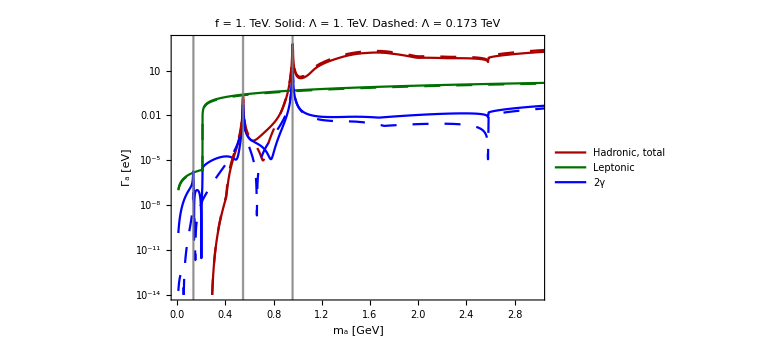

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\Total-widths-Fermion universal.pdf

```mathematica
Do[decaysplots[i]=Join[GroupsClasses[i,"Hadronic, total"],GroupsClasses[i,"Non-hadronic"],GroupsClasses[i,"Total"]],{i,1,2,1}];
fval=10^3;
img2=Show[ListLogPlot[Evaluate[Join[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[1,group],#[[1]]>1.75&],GroupWidthsTot[1,group]],{group,Select[decaysplots[1],#!="Total"&]}],Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[2,group],#[[1]]>1.75&],GroupWidthsTot[2,group]],{group,Select[decaysplots[2],#!="Total"&]}]]],PlotStyle->{{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@Drop[decaysplots[1],-1],Right],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.01,2.99},{10^-14,10^3}},PlotLabel->Style[Row[{"f = ", fval*10^-3., " TeV. Solid: Λ = ",Interpreter["Number"][ModelsList[[1]][[2]]] 10^-3.," TeV. Dashed: Λ = ",Interpreter["Number"][ModelsList[[2]][[2]]] 10^-3.," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.2]]},2->{Bottom,Directive[Gray,Opacity[0.2]]},3->{Bottom,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Total-widths-``.pdf",Sequence@@{SelectedModels[[1]][[1]]}]}],img2]
```

# ALP production

## Decays of B mesons

## Production probabilities

```mathematica
(*Fractions of B^(+ or - or 0 or OverBar[0]) per PoT*)
{χparticle["B","FNAL"],χparticle["B","SPS"],χparticle["B","LHC"]}={(3.8*10^-9)/(40.*12^-0.29)*2*0.8,1.7*10^-7*2*0.8*1.6,8.4*10^-3*2*0.624};
{χparticle["π^0","FNAL"],χparticle["π^0","SPS"],χparticle["π^0","LHC"]}={2.9,4,42.8};
{χparticle["η","FNAL"],χparticle["η","SPS"],χparticle["η","LHC"]}={0.32,0.39,4.7};
{χparticle["η'","FNAL"],χparticle["η'","SPS"],χparticle["η'","LHC"]}={0.033,0.079,0.5};
listFacility=Keys[DownValues@χparticle][[All,1,2]]//DeleteDuplicates
```

## Branching ratios

### B->S+X_s

```mathematica
(*Br(B->a+Subscript[X, s])/|Subscript[C, bs]|^2 (see the paper for details)*)
BrBdecaysTableTemp=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with fermion coupling/branching ratios/BrBtoALP.m"}],"MX"];
BrBdecaysTableTemp[[1]]
BrBdecaysTable=SortBy[Join[Drop[BrBdecaysTableTemp,1],{Join[{5.279-0.495},Table[10^-90.,Length[BrBdecaysTableTemp[[1]]-1]]]}],#[[1]]&];
FractionBtoKplus[ma_]=Interpolation[{#[[1]],If[#[[9]]==0,0,(#[[2]])/(#[[9]])]}&/@Drop[BrBdecaysTableTemp,1],InterpolationOrder->1][ma];
FractionBtoKstar[ma_]=Interpolation[{#[[1]],If[#[[9]]==0,0,(#[[6]])/(#[[9]])]}&/@Drop[BrBdecaysTableTemp,1],InterpolationOrder->1][ma];
Do[BrBtoALP["K^+",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-MASS["K^+"],Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,2}]],InterpolationOrder->1][ma]],0];
BrBtoALP["K_0^*",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-0.845,Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,3}]],InterpolationOrder->1][ma]],0];
BrBtoALP["K_1",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-1.27,Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,4}]],InterpolationOrder->1][ma]],0];
BrBtoALP["K_2^*",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-1.27,Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,5}]],InterpolationOrder->1][ma]],0];
BrBtoALP["K^*(892)",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-0.892,Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,6}]],InterpolationOrder->1][ma]],0];
BrBtoALP["K^*(1410)",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-1.41,Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,7}]],InterpolationOrder->1][ma]],0];
BrBtoALP["K^*(1680)",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-1.68,Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,8}]],InterpolationOrder->1][ma]],0];
BrBtoALP["X_s",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-MASS["K^+"],Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[BrBdecaysTable[[All,{1,9}]],InterpolationOrder->1][ma]],0];
BrBtoALP["K^++K^*(892)",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-MASS["K^+"],Evaluate[cij["b->s",model,Λ,f]^2*Interpolation[Join[BrBdecaysTable[[All,{1}]],BrBdecaysTable[[All,{2}]]+BrBdecaysTable[[All,{6}]],2],InterpolationOrder->1][ma]],0];
,{model,ModelListAll}]
```

{ma, GeV,BR(B→K^++a)/|C_bs|^2,BR(B→K_0^*+a)/|C_bs|^2,BR(B→K_1+a)/|C_bs|^2,BR(B→K_2^*+a)/|C_bs|^2,BR(B→K^*(892)+a)/|C_bs|^2,BR(B→K^*(1410)+a)/|C_bs|^2,BR(B→K^*(1680)+a)/|C_bs|^2,Total BR}

### B->S+π

```mathematica
fBπ=0.96;
Do[
MBtoπa[model,Λ_,ma_,f_]=cij["b->d",model,Λ,f]*(MASS["B^+"]^2-MASS["π^+"]^2)/(MASS["b"]-MASS["d"])*fBπ;
BrBtoALP["π^+",model,Λ_,ma_,f_]=If[ma<MASS["B^+"]-MASS["π^+"],Evaluate[1/DECAYWIDTH["B^+"] MBtoπa[model,Λ,ma,f]^2/(8Pi)(√(((MASS["B^+"]^2-MASS["π^+"]^2+ma^2)/(2MASS["B^+"]))^2-ma^2))/(MASS["B^+"]^2)],0];
,{model,ModelListAll}]
```

### Total

```mathematica
Do[
BrBtoALP["Total",model,Λ_,ma_,f_]=BrBtoALP["X_s",model,Λ,ma,f]+BrBtoALP["π^+",model,Λ,ma,f];
Do[PALPprod["B",model,facility,ma_,f_,Λ_]=χparticle["B",facility]*BrBtoALP["Total",model,Λ,ma,f],{facility,listFacility}];
,{model,ModelListAll}];
```

### Plot

{K_1,K^+,K^*(1410),K^*(1680),K^*(892),K^++K^*(892),K_0^*,K_2^*,π^+,Total}

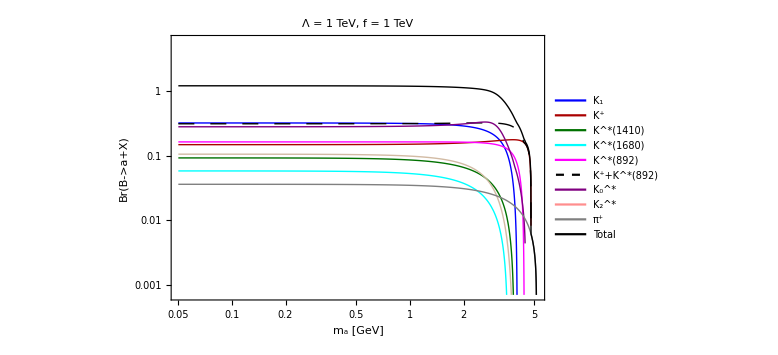

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\BrBtoALP.pdf

```mathematica
keysBprod=Select[Keys[DownValues@BrBtoALP][[All,1,1]]//DeleteDuplicates//Sort,#!="X_s"&]
plotBprod[model_,Λ_,f_]:=Show[LogLogPlot[Evaluate[Table[BrBtoALP[key,model,Λ,ma,f],{key,keysBprod}]],{ma,0.05,5.2},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Cyan},{Thick,Magenta},{Thick,Black,Dashing[0.02]},{Thick,Purple},{Thick,Lighter@Lighter@Brown},{Thick,Gray},{Thick,Black},{Thick,Lighter@Lighter@Blue}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Br(B->a+X)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.05,5.2},{BrBtoALP["Total",model,Λ,5.13,f],5BrBtoALP["Total",model,Λ,0.,f]}},PlotLabel->Style[Row[{"Λ = ",10^-3 Λ," TeV, f = ", 10^-3 f," TeV"}],22,Black]],LogLogPlot[{10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3},{x,1.5,10},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green}},PlotLegends->Placed[Style[#,15]&/@Take[keysBprod,{1,3}],{0.15,0.15}]],LogLogPlot[{10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3},{x,1.5,10},PlotStyle->{{Thick,Cyan},{Thick,Magenta},{Thick,Black,Dashing[0.02]},{Thick,Purple},{Thick,Lighter@Lighter@Red},{Thick,Gray},{Thick,Black}},PlotLegends->Placed[Style[#,15]&/@Take[keysBprod,{4,6}],{0.38,0.15}]],LogLogPlot[{10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3},{x,1.5,10},PlotStyle->{{Thick,Purple},{Thick,Lighter@Lighter@Red},{Thick,Gray},{Thick,Black}},PlotLegends->Placed[Style[#,15]&/@Take[keysBprod,{7,9}],{0.6,0.15}]],LogLogPlot[{10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3,10^9 x,10^9 x^2,10^9 x^3},{x,1.5,10},PlotStyle->{{Thick,Black}},PlotLegends->Placed[Style[#,15]&/@Take[keysBprod,{10,10}],{0.74,0.15}]]]
plotBprod["Fermion universal",10^3,10^3]
Export[FileNameJoin[{NotebookDirectory[],"plots","BrBtoALP.pdf"}],plotBprod["Fermion universal",10^3,10^3]]
```

## Mixing with neutral mesons

```mathematica
Do[PALPprod[particle,model,facility,ma_,fa_,Λ_]=χparticle[particle,facility]*θm0a[model,Λ,particle,ma,fa]^2,{particle,listMesonP0},{model,ModelListAll},{facility,listFacility}];
```

## Mixing with neutral mesons

Import::nffil: File C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\phenomenology\ALPs with fermion coupling\branching ratios\sigma-Drell-Yan-ALP-fermion.txt not found during Import.

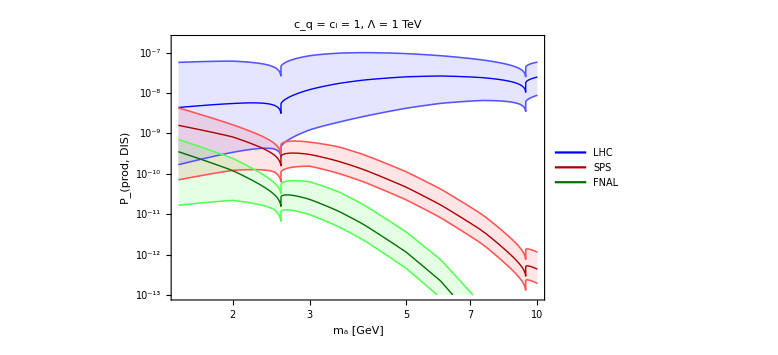

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\DIS-production-uncertainty.pdf

```mathematica
σDrellYanDataALPFromFermionTemp=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with fermion coupling/branching ratios/sigma-Drell-Yan-ALP-fermion.txt"}],"Table"];
(*σDrellYanDataALPfermion={#[[1]],#[[2]],#[[3]],#[[4]],Abs[cGGeff[#[[1]],{"u","d","s","c","b","t"}]]^2#[[5]],Abs[cGGeff[#[[1]],{"u","d","s","c","b","t"}]]^2 αsData[#[[1]]]^2#[[6]],Abs[cGGeff[#[[1]],{"u","d","s","c","b","t"}]] αsData[#[[1]]]^2#[[7]]}&/@σDrellYanDataALPfermionTemp;*)
σDrellYanDataALPFromGluonTemp["FNAL"]=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with gluon coupling/branching ratios/sigma-prod-ALP-gluon-Drell-Yan-FNAL.txt"}],"Table"];
σDrellYanDataALPFromGluonTemp["SPS"]=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with gluon coupling/branching ratios/sigma-prod-ALP-gluon-Drell-Yan-SPS.txt"}],"Table"];
σDrellYanDataALPFromGluonTemp["LHC"]=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with gluon coupling/branching ratios/sigma-prod-ALP-gluon-Drell-Yan-LHC.txt"}],"Table"];
{σppFacility["FNAL"],σppFacility["SPS"],σppFacility["LHC"]}={40*10^9*12^-0.29,40*10^9*96^-0.29,78*10^9};
Do[
cGval[ma_,model,Λ_]=(cG+cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}])/.tableValuesReplacement[model,Λ];
Do[
PALPprod["Drell-Yan",model,facility,ma_,f_,Λ_]=If[ma>=1.5,Evaluate[1/σppFacility[facility] 1/f^2 Abs[cGval[ma,model,Λ]]^2 10^(Interpolation[Log10[σDrellYanDataALPFromGluonTemp[facility][[All,{1,2}]]],InterpolationOrder->1][Log10[ma]])],0];
PALPprodLower["Drell-Yan",model,facility,ma_,f_,Λ_]=If[ma>=1.5,Evaluate[1/σppFacility[facility] 1/f^2 Abs[cGval[ma,model,Λ]]^2 10^(Interpolation[Log10[σDrellYanDataALPFromGluonTemp[facility][[All,{1,3}]]],InterpolationOrder->1][Log10[ma]])],0];
PALPprodUpper["Drell-Yan",model,facility,ma_,f_,Λ_]=If[ma>=1.5,Evaluate[1/σppFacility[facility] 1/f^2 Abs[cGval[ma,model,Λ]]^2 10^(Interpolation[Log10[σDrellYanDataALPFromGluonTemp[facility][[All,{1,4}]]],InterpolationOrder->1][Log10[ma]])],0];
,{facility,listFacility}]
,{model,ModelListAll}];
DISuncertainty=Show[LogLogPlot[{PALPprod["Drell-Yan","Fermion universal","LHC",ma,10^3,10^3],PALPprodLower["Drell-Yan","Fermion universal","LHC",ma,10^3,10^3],PALPprodUpper["Drell-Yan","Fermion universal","LHC",ma,10^3,10^3],PALPprod["Drell-Yan","Fermion universal","SPS",ma,10^3,10^3],PALPprodLower["Drell-Yan","Fermion universal","SPS",ma,10^3,10^3],PALPprodUpper["Drell-Yan","Fermion universal","SPS",ma,10^3,10^3],PALPprod["Drell-Yan","Fermion universal","FNAL",ma,10^3,10^3],PALPprodLower["Drell-Yan","Fermion universal","FNAL",ma,10^3,10^3],PALPprodUpper["Drell-Yan","Fermion universal","FNAL",ma,10^3,10^3]},{ma,1.5,10},PlotStyle->{{Thick,Blue},{Thickness[0.002],Lighter@Blue},{Thickness[0.002],Lighter@Blue},{Thick,Darker@Red},{Thickness[0.002],Lighter@Red},{Thickness[0.002],Lighter@Red},{Thick,Darker@Darker@Green},{Thickness[0.002],Lighter@Green},{Thickness[0.002],Lighter@Green},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"m_a [GeV]" , "P_(prod, DIS)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.5,10},{10^-13,2*10^-7}},Filling->{2->{{3},Directive[Blue,Opacity[0.1]]},5->{{6},Directive[Red,Opacity[0.1]]},8->{{9},Directive[Green,Opacity[0.1]]}},PlotLabel->Style[Row[{"c_q = c_l = 1, Λ = 1 TeV"}],22,Black]],LogLogPlot[{x,x^2,x^3},{x,1.5,10},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green}},PlotLegends->Placed[Style[#,20]&/@Join[{"LHC","SPS","FNAL"}],{0.13,0.2}]]]
Export[FileNameJoin[{NotebookDirectory[],"plots/DIS-production-uncertainty.pdf"}],DISuncertainty]
```

## Comparison

## Total amounts

{B,π^0,η,η',Drell-Yan}

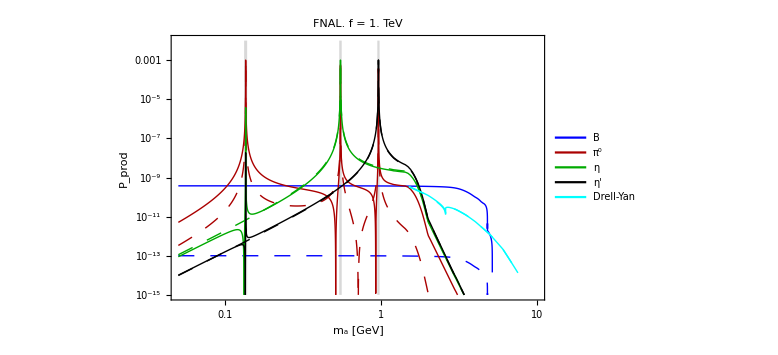
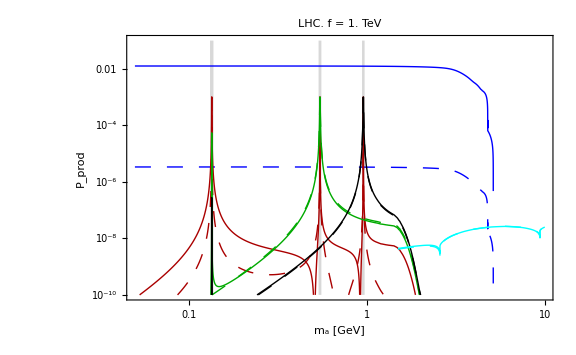
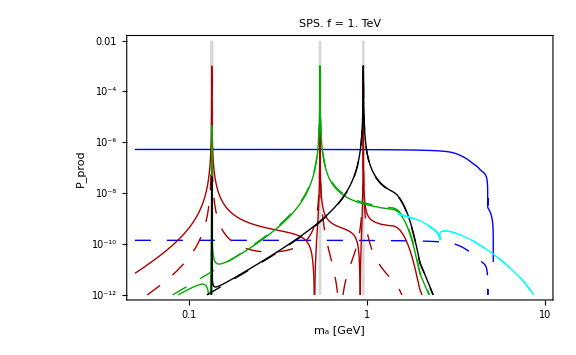

```mathematica
ProductionChannels=Keys[DownValues@PALPprod][[All,1,1]]//DeleteDuplicates
PlotProduction[facility_,model_,LegendPresence_,xPosLeg_,yPosLeg_,ymin_,ymax_,ptnum_]:=Show[LogLogPlot[Evaluate[Join[Flatten[Table[Min[PALPprod[prod,model,facility,ma,10^3,scale],If[MemberQ[{"π^0","η","η'"},prod]==True,10^-3,1]],{prod,ProductionChannels},{scale,{10^3,MASS["t"]}}]],{10^30 UnitStep[(MASS["π^0"]+0.003)-ma]*UnitStep[ma-(MASS["π^0"]-0.003)],10^30 UnitStep[(MASS["η"]+0.01)-ma]*UnitStep[ma-(MASS["η"]-0.01)],10^10 UnitStep[(MASS["η'"]+0.016)-ma]*UnitStep[ma-(MASS["η'"]-0.016)]}]],{ma,0.05,10},PlotPoints->ptnum,PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[0.02]},{Thick, Darker@Red},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Green},{Thick,Darker@Green,Dashing[0.02]},{Thick,Black},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"m_a [GeV]" , "P_prod"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.05,10},{ymin,ymax}},PlotLabel->Style[Row[{facility, ". f = ", 1.," TeV"}],22,Black],Filling->{11->{Bottom,Directive[Gray,Opacity[0.3]]},12->{Bottom,Directive[Gray,Opacity[0.3]]},13->{Bottom,Directive[Gray,Opacity[0.3]]}}],LogLogPlot[{10+x,10+x,10+x,10+x,10+x},{x,0.05,10},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Green},{Thick,Black},{Thick,Cyan}},PlotLegends->If[LegendPresence=="True",Placed[Style[#,16]&/@ProductionChannels,{xPosLeg,yPosLeg}],{}]]]
plotprod["FNAL"]=PlotProduction["FNAL","Fermion universal","True",0.85,0.72,10^-15,10^-2,500];
plotprod["SPS"]=PlotProduction["SPS","Fermion universal","False",0.16,0.8,10^-12,10^-2,500];
plotprod["LHC"]=PlotProduction["LHC","Fermion universal","False",0.85,0.25,10^-10,10^-1,500];
Style[Evaluate[Table[plotprod[fac],{fac,listFacility}]],ImageSizeMultipliers->{1,1,1}]
Do[Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["ALP-production-``.pdf",Sequence@@{facility}]}],plotprod[facility]],{facility,listFacility}]
```

## Angular distribution

### Importing distributions and constructing the probabilities

```mathematica
filenameDistr["Drell-Yan"]="Pregenerated/DoubleDistrALPsGluonDrellYan-``.txt";
filenameDistr["B"]="DoubleDistr-ALPgluon-From-B-``.dat";
filenameDistr["π^0"]="DoubleDistr-ALPgluon-mixing-from-Pi0-``.dat";
filenameDistr["η"]="DoubleDistr-ALPgluon-mixing-from-Eta-``.dat";
filenameDistr["η'"]="DoubleDistr-ALPgluon-mixing-from-Etapr-``.dat";
(*Importing angle-energy distributions*)
Do[
DoubleDistrALP[channel,facility,ma_,θa_,Ea_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling",ToString@StringForm[filenameDistr[channel],Sequence@@{If[facility=="FNAL","FermilabBD",facility]}]}],"Table"],InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea]]);
{{mmin[channel,facility],mmax[channel,facility]},{θmin[channel,facility],θmax[channel,facility]},{Emin[channel,facility],Emax[channel,facility]}}=10^DoubleDistrALP[channel,facility,mass,θa,Ea][[2]][[0]][[1]]
,{channel,ProductionChannels},{facility,listFacility}];//AbsoluteTiming
```

{20.0524,Null}

### Angular distribution

```mathematica
MassesAngDistr={0.2,2};
{EmaxFacility["FNAL"],EmaxFacility["SPS"],EmaxFacility["LHC"]}={120.,400.,6500.}
θboundary=0.01;
Do[
Fraction[channel,facility,"<10 mrad",ma_]=10^(Interpolation[ParallelTable[{ma,If[mmin[channel,facility]<=ma<=mmax[channel,facility],Quiet[Log10[NIntegrate[DoubleDistrALP[channel,facility,ma,Exp[th],Exp[Ea]]Exp[th]Exp[Ea],{th,Log[10^-5.],Log[θboundary]},{Ea,Log[ma],Log[Emax[channel,facility]]},Method->"AdaptiveMonteCarlo"]]],-90.]},{ma,mmin[channel,facility],mmax[channel,facility],(mmax[channel,facility]-mmin[channel,facility])/30}],InterpolationOrder->1][ma]);
Fraction[channel,facility,">10 mrad",ma_]=10^(Interpolation[ParallelTable[{ma,If[mmin[channel,facility]<=ma<=mmax[channel,facility],Quiet[Log10[NIntegrate[DoubleDistrALP[channel,facility,ma,Exp[th],Exp[Ea]]Exp[th]Exp[Ea],{th,Log[θboundary],Log[θmax[channel,facility]]},{Ea,Log[ma],Log[Emax[channel,facility]]},Method->"AdaptiveMonteCarlo"]]],-90.]},{ma,mmin[channel,facility],mmax[channel,facility],(mmax[channel,facility]-mmin[channel,facility])/30}],InterpolationOrder->1][ma]);
Do[
FractionProbability[model,Λ_,channel,facility,"<10 mrad",ma_,f_]=PALPprod[channel,model,facility,ma,f,Λ]*Fraction[channel,facility,"<10 mrad",ma];
FractionProbability[model,Λ_,channel,facility,">10 mrad",ma_,f_]=PALPprod[channel,model,facility,ma,f,Λ]*Fraction[channel,facility,">10 mrad",ma];
,{model,ModelListAll}];
,{channel,ProductionChannels},{facility,listFacility}]//AbsoluteTiming
```

{28.5566,Null}

### Plot

InterpolatingFunction::dmval: Input value {0.0500005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0504578} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0509193} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

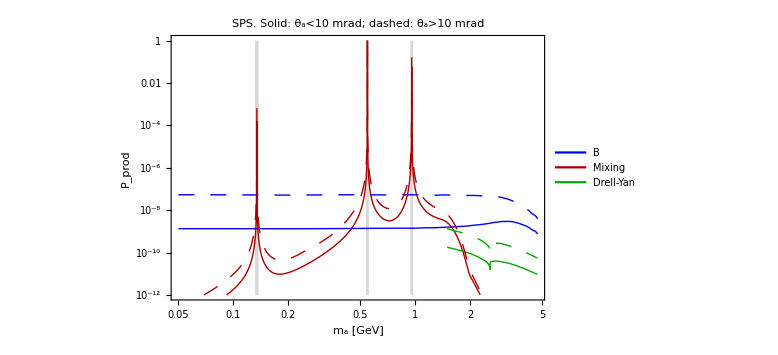

InterpolatingFunction::dmval: Input value {0.0500005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0504578} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0509193} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\P-prod-domains.pdf

```mathematica
ptfac[model_,Λ_,facility_,f_,ptnum_]:=Show[LogLogPlot[Evaluate[{FractionProbability[model,Λ,"B",facility,"<10 mrad",ma,f],FractionProbability[model,Λ,"π^0",facility,"<10 mrad",ma,f]+FractionProbability[model,Λ,"η",facility,"<10 mrad",ma,f]+FractionProbability[model,Λ,"η'",facility,"<10 mrad",ma,f],FractionProbability[model,Λ,"Drell-Yan",facility,"<10 mrad",ma,f],FractionProbability[model,Λ,"B",facility,">10 mrad",ma,f],FractionProbability[model,Λ,"π^0",facility,">10 mrad",ma,f]+FractionProbability[model,Λ,"η",facility,">10 mrad",ma,f]+FractionProbability[model,Λ,"η'",facility,">10 mrad",ma,f],FractionProbability[model,Λ,"Drell-Yan",facility,">10 mrad",ma,f],10^30 UnitStep[(MASS["π^0"]+0.003)-ma]*UnitStep[ma-(MASS["π^0"]-0.003)],10^30 UnitStep[(MASS["η"]+0.01)-ma]*UnitStep[ma-(MASS["η"]-0.01)],10^10 UnitStep[(MASS["η'"]+0.016)-ma]*UnitStep[ma-(MASS["η'"]-0.016)]}],{ma,0.05,4.7},PlotPoints->ptnum,PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Green},{Thick,Blue,Dashing[0.02]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Green,Dashing[0.02]},{Thick,Black},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"m_a [GeV]" , "P_prod"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.05,4.7},{10^-12,1}},PlotLabel->Style[Row[{facility,". Solid: θ_a<10 mrad; dashed: θ_a>10 mrad"}],22,Black],Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}}],LogLogPlot[{10+x,10+x,10+x,10+x,10+x},{x,0.05,10},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Green},{Thick,Black},{Thick,Cyan}},PlotLegends->Placed[Style[#,20]&/@{"B","Mixing","Drell-Yan"},{0.8,0.8}]]]
ptfac["Fermion universal",300,"SPS",10^3,500]
Export[FileNameJoin[{NotebookDirectory[],"plots/P-prod-domains.pdf"}],ptfac["Fermion universal",300,"SPS",10^3,500]]
```

## Exporting tabulated couplings and br ratios

## Exporting block

```mathematica
BlockProductionFractionsTabulation[Model_,Λ_]:=Block[{},
Do[crgval[ALPcouplingslist[[i]]]=cRGval[Model,Λ,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
mlist1=Select[Table[ma,{ma,0.001,10.,0.001}],#!=MASS["η"]&&#!=MASS["η'"]&&#!=MASS["π^0"]&];
TabulatedMixingAngles=Join[{{"ma GeV","theta2_api0","theta2_aeta","theta2_aetapr","P_pi0mix->a,FNAL (DUNE)","P_etamix->a,SPS (SHiP)","P_etaprmix->a,LHC"}},Table[{ma,θm0a[Model,Λ,"π^0",ma,1]^2,θm0a[Model,Λ,"η",ma,1]^2,θm0a[Model,Λ,"η'",ma,1]^2,PALPprod["π^0",Model,"FNAL",ma,1,Λ],PALPprod["η",Model,"SPS",ma,1,Λ],PALPprod["η'",Model,"LHC",ma,1,Λ]},{ma,mlist1}]];
TabulatedBrBdecay=Join[{{"ma GeV","Br_Kplus","Br_K0star","Br_K1","Br_K2star","Br_Kstar892","Br_Kstar1410","Br_Kstar1680","Br_Piplus","Br_Total","P_B->a,FNAL (DUNE)","P_B->a,SPS (SHiP)","P_B->a,LHC"}},Table[{ma,BrBtoALP["K^+",Model,Λ,ma,1],BrBtoALP["K_0^*",Model,Λ,ma,1],BrBtoALP["K_1",Model,Λ,ma,1],BrBtoALP["K_2^*",Model,Λ,ma,1],BrBtoALP["K^*(892)",Model,Λ,ma,1],BrBtoALP["K^*(1410)",Model,Λ,ma,1],BrBtoALP["K^*(1680)",Model,Λ,ma,1],BrBtoALP["π^+",Model,Λ,ma,1],BrBtoALP["Total",Model,Λ,ma,1],PALPprod["B",Model,"FNAL",ma,1,Λ],PALPprod["B",Model,"SPS",ma,1,Λ],PALPprod["B",Model,"LHC",ma,1,Λ]},{ma,mlist1}]];
cGvalExport[ma_,f_]=1/f(cG+cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}])/.tableValuesReplacement[Model,Λ];
TabulatedcGGcoupling=Join[{{"ma GeV","|cGeff|","P_Drell-Yan,FNAL (DUNE)","P_Drell-Yan,SPS (SHiP)","P_Drell-Yan,LHC"}},Table[{ma,Abs[cGvalExport[ma,1]],PALPprod["Drell-Yan",Model,"FNAL",ma,1,Λ],PALPprod["Drell-Yan",Model,"SPS",ma,1,Λ],PALPprod["Drell-Yan",Model,"LHC",ma,1,Λ]},{ma,mlist1}]];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/branching ratios",ToString@StringForm["ProdProbabilitiesFromB-model-``-Lambda-``-TeV.csv",Sequence@@{Model,(10^-3 Λ)//CForm//ToString}]}],TabulatedBrBdecay,"csv"];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/branching ratios",ToString@StringForm["ProdProbabilitiesFromMixing-model-``-Lambda-``-TeV.csv",Sequence@@{Model,(10^-3 Λ)//CForm//ToString}]}],TabulatedMixingAngles,"csv"];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/branching ratios",ToString@StringForm["ProdProbabilitiesDrellYan-model-``-Lambda-``-TeV.csv",Sequence@@{Model,(10^-3 Λ)//CForm//ToString}]}],TabulatedcGGcoupling,"csv"];
]
```

## Exporting tabulated quantities

```mathematica
Print["Model for exporting:"]
ModelForExporting=dropdownDialog[ModelListAll,"Select the model for br ratios exporting:"]
Print["Scale Λ:"]
ΛChoice=DialogInput[{cut=""},Column[{"Enter the scale Λ in GeV:",InputField[Dynamic[cut],Expression],Button["Proceed",DialogReturn[cut],ImageSize->Automatic]}]]//N
BlockProductionFractionsTabulation[ModelForExporting,ΛChoice]
```

Model for exporting:

Gluon

Scale Λ:

1000.

InterpolatingFunction::dmval: Input value {0.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## Exporting|θ_(am^0)|^2/Br(B->a)/|c_(G,eff)|^2 (for SensCalc)

### Exporting block

```mathematica
BlockProductionFractionsSensCalc[Model_,Λ_]:=Module[{},
(*Fixing the values of the low-energy ALP couplings given the model and Λ*)
Do[crgval[ALPcouplingslist[[i]]]=cRGval[Model,Λ,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
cGvalExport[ma_,f_]=1/f(cG+cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}])/.tableValuesReplacement[Model,Λ];
listtoexport={θm0a[Model,Λ,"π^0",ma,f]^2,θm0a[Model,Λ,"η",ma,f]^2,θm0a[Model,Λ,"η'",ma,f]^2,BrBtoALP["Total",Model,Λ,ma,f],cGvalExport[ma,f],BrBtoALP["K^+",Model,Λ,ma,f],BrBtoALP["K^*(892)",Model,Λ,ma,f]};
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/branching ratios",ToString@StringForm["Coefs-production-``-scale-``-GeV.m",Sequence@@{Model,Λ//CForm//ToString}]}],listtoexport,"MX"]
]
```

### Exporting

```mathematica
Print["Model for exporting:"]
ModelForExporting=dropdownDialog[ModelListAll,"Select the model for decay widths exporting:"]
Print["Scale Λ:"]
ΛChoice=DialogInput[{cut=""},Column[{"Enter the scale Λ in GeV:",InputField[Dynamic[cut],Expression],Button["Proceed",DialogReturn[cut],ImageSize->Automatic]}]]//N
BlockProductionFractionsSensCalc[ModelForExporting,ΛChoice]
```

Model for exporting:

Gluon

Scale Λ:

1000.

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\phenomenology\branching ratios\Coefs-production-Gluon-scale-1000.-GeV.m

Model for exporting:

Fermion universal

Scale Λ:

1000.

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\phenomenology\branching ratios\Coefs-production-Fermion universal-scale-1000.-GeV.m

# Deleting generated cells/proceeding to an other experiment

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
deletecellsopt=dropdownDialog[{"Yes","No"},Row[{"Would you like to remove all the generated output cells after the given computation?"}]];
If[deletecellsopt=="Yes",FrontEndTokenExecute["DeleteGeneratedCells"]]
```